```mathematica
ClearAll["Global`*"]
```

### Load up packages

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
Needs["ComputerArithmetic`"]
```

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/";
SetDirectory[dir];
<<Liemohn_and_Khazanov__mapped_Maxwellian_density.wl
<<jvFuncs.wl
```

```mathematica
Get["funcs_for_stepMonitor_stringConv_plotSetOfInds_etc.m"]
(*Includes (as of 2018/03/29)
makeErrorData[x_,y_,yErr_]
kPlotStepMonitorData[kStepVals_]
gPlotStepMonitorData[gStepVals_]
tStringToSec[tString_]
minTidInd[tSearchString_,tStringArr_]
tPlotInds[inds_,mom_,momErr_,pRange_,xTitle_,yTitle_]
tPlotRange[ind1_,ind2_,mom_,momErr_,pRange_,xTitle_,yTitle_]
tablePlotMov[indStart_,indEnd1_,indEnd2_,mom_,momErr_,pRange_]
tablePlotsCombineAndAnimate[mov1_,mov2_]*)
```

## Initialize J-V, J_E-V data

```mathematica
orbit=1612;
```

```mathematica
makePlots=1;
```

### pot offset (in V)?

```mathematica
potTFactor=0;
```

```mathematica
If[potTFactor == 0,potFactorString="",potFactorString=ToString@StringForm["__`1`V_offset",potTFactor]];
```

### And the data ...

#### Data set 1 (oppdatert 2018/03/26)

```mathematica
time={"12:00:24.114","12:00:24.430","12:00:24.745","12:00:25.060","12:00:25.376","12:00:25.691","12:00:26.006","12:00:26.322","12:00:26.637","12:00:26.952","12:00:27.268","12:00:27.583","12:00:27.898","12:00:28.213","12:00:28.529","12:00:28.844","12:00:29.159","12:00:29.475","12:00:29.790","12:00:30.105","12:00:30.421","12:00:30.736","12:00:31.051","12:00:31.367","12:00:31.682","12:00:31.997","12:00:32.313","12:00:32.628","12:00:32.943","12:00:33.259","12:00:33.574","12:00:33.889","12:00:34.205","12:00:34.520","12:00:34.835","12:00:35.150","12:00:35.466","12:00:35.781","12:00:36.096","12:00:36.412","12:00:36.727","12:00:37.042","12:00:37.358","12:00:37.673","12:00:37.988","12:00:38.304","12:00:38.619","12:00:38.934","12:00:39.250","12:00:39.565","12:00:39.880","12:00:40.196","12:00:40.511","12:00:40.826","12:00:41.142","12:00:41.457","12:00:41.772","12:00:42.088","12:00:42.403","12:00:42.718","12:00:43.033","12:00:43.349","12:00:43.664","12:00:43.979","12:00:44.295","12:00:44.610","12:00:44.925","12:00:45.241","12:00:45.556","12:00:45.871","12:00:46.187","12:00:46.502","12:00:46.817","12:00:47.133","12:00:47.448","12:00:47.763","12:00:48.079","12:00:48.394","12:00:48.709","12:00:49.025","12:00:49.340","12:00:49.655","12:00:49.971","12:00:50.286","12:00:50.601","12:00:50.917","12:00:51.232","12:00:51.547","12:00:51.863","12:00:52.178","12:00:52.493","12:00:52.809","12:00:53.124","12:00:53.439","12:00:53.755","12:00:54.070","12:00:54.385","12:00:54.701","12:00:55.016","12:00:55.331","12:00:55.647","12:00:55.962","12:00:56.277","12:00:56.593","12:00:56.908","12:00:57.223","12:00:57.539","12:00:57.854","12:00:58.169","12:00:58.485","12:00:58.800","12:00:59.115","12:00:59.431","12:00:59.746","12:01:00.061","12:01:00.377","12:01:00.692","12:01:01.007","12:01:01.323","12:01:01.638","12:01:01.953","12:01:02.269","12:01:02.584","12:01:02.899","12:01:03.215","12:01:03.530","12:01:03.845","12:01:04.161","12:01:04.476","12:01:04.791","12:01:05.107","12:01:05.422","12:01:05.737","12:01:06.053","12:01:06.368","12:01:06.683","12:01:06.999","12:01:07.314","12:01:07.629","12:01:07.945","12:01:08.260","12:01:08.575","12:01:08.891","12:01:09.206","12:01:09.521","12:01:09.837","12:01:10.152","12:01:10.467","12:01:10.783","12:01:11.098","12:01:11.413","12:01:11.729","12:01:12.044","12:01:12.359","12:01:12.675","12:01:12.990","12:01:13.305","12:01:13.621","12:01:13.936","12:01:14.251","12:01:14.567","12:01:14.882","12:01:15.197","12:01:15.513","12:01:15.828","12:01:16.144","12:01:16.459","12:01:16.774","12:01:17.090","12:01:17.405","12:01:17.720","12:01:18.036","12:01:18.351","12:01:18.666","12:01:18.982","12:01:19.297","12:01:19.612","12:01:19.928","12:01:20.243","12:01:20.558","12:01:20.874","12:01:21.189","12:01:21.504","12:01:21.820","12:01:22.135","12:01:22.450","12:01:22.766","12:01:23.081","12:01:23.397","12:01:23.712","12:01:24.027","12:01:24.343","12:01:24.658","12:01:24.973","12:01:25.289","12:01:25.604","12:01:25.919","12:01:26.235","12:01:26.550","12:01:26.865","12:01:27.181","12:01:27.496","12:01:27.811","12:01:28.127","12:01:28.442","12:01:28.757","12:01:29.073","12:01:29.388","12:01:29.703","12:01:30.019","12:01:30.334","12:01:30.650","12:01:30.965","12:01:31.280","12:01:31.596","12:01:31.911","12:01:32.226","12:01:32.542","12:01:32.857","12:01:33.172","12:01:33.488","12:01:33.803","12:01:34.118","12:01:34.434","12:01:34.749","12:01:35.064","12:01:35.380","12:01:35.695","12:01:36.010","12:01:36.326","12:01:36.641","12:01:36.957","12:01:37.272","12:01:37.587","12:01:37.903","12:01:38.218","12:01:38.533","12:01:38.849","12:01:39.164","12:01:39.479","12:01:39.795","12:01:40.110","12:01:40.425","12:01:40.741","12:01:41.056","12:01:41.372","12:01:41.687","12:01:42.002","12:01:42.318","12:01:42.633","12:01:42.948","12:01:43.264","12:01:43.579","12:01:43.894","12:01:44.210","12:01:44.525","12:01:44.840","12:01:45.156","12:01:45.471","12:01:45.787","12:01:46.102","12:01:46.417","12:01:46.733"};
pots={815.36,940.80,940.80,1128.96,1128.96,1379.84,1379.84,1379.84,1379.84,1379.84,1379.84,1572.48,1449.28,1232.00,1357.44,1330.56,1429.12,1429.12,1429.12,1330.56,1205.12,1205.12,1012.48,1012.48,1012.48,1012.48,851.20,913.92,840.00,851.20,851.20,790.72,777.28,777.28,840.00,777.28,840.00,840.00,840.00,913.92,913.92,913.92,1012.48,1012.48,1010.24,940.80,940.80,940.80,940.80,940.80,689.92,689.92,960.96,1010.24,934.08,1059.52,1059.52,1008.00,1008.00,1008.00,1008.00,1008.00,1133.44,1133.44,1133.44,1133.44,1133.44,1133.44,1008.00,1008.00,1008.00,934.08,790.72,678.72,678.72,543.20,407.68,344.96,344.96,344.96,344.96,344.96,344.96,235.20,172.48,172.48,344.96,235.20,564.48,407.68,172.48,407.68,203.84,172.48,172.48,172.48,203.84,203.84,203.84,203.84,203.84,172.48,203.84,203.84,172.48,172.48,172.48,172.48,172.48,172.48,203.84,172.48,117.60,172.48,203.84,203.84,203.84,203.84,203.84,203.84,203.84,203.84,172.48,172.48,203.84,235.20,282.24,282.24,282.24,117.60,101.92,203.84,235.20,282.24,407.68,407.68,407.68,407.68,344.96,235.20,235.20,203.84,203.84,249.06,293.02,368.06,378.84,453.88,453.88,447.72,447.72,427.70,358.82,358.82,355.74,355.74,282.24,282.24,235.20,235.20,235.20,203.84,172.48,58.80,43.12,43.12,50.96,86.24,172.48,172.48,172.48,235.20,344.96,358.82,430.78,498.12,498.12,562.80,605.92,605.92,605.92,749.28,724.64,749.28,749.28,835.52,884.80,790.72,913.92,913.92,913.92,913.92,913.92,913.92,913.92,913.92,913.92,913.92,665.28,566.72,616.00,678.72,566.72,566.72,529.76,417.76,393.12,393.12,346.08,70.56,282.24,203.84,235.20,235.20,235.20,282.24,282.24,172.48,172.48,117.60,172.48,302.26,487.34,578.34,706.86,835.38,849.24,832.30,717.64,717.64,656.88,592.48,592.48,656.88,493.50,407.68,344.96,344.96,344.96,344.96,344.96,344.96,203.84,282.24,344.96,235.20,203.84,203.84,203.84,117.60,117.60,86.24,70.56,86.24,141.12,235.20,282.24,282.24,282.24,282.24,344.96,282.24,282.24};
curs={1.077,1.128,1.171,1.277,1.269,1.291,1.268,1.308,1.366,1.400,1.350,1.022,1.173,0.844,0.857,0.860,0.863,1.035,1.093,1.046,1.052,0.970,0.941,0.955,0.950,0.866,0.886,0.902,0.902,0.839,0.822,0.943,0.760,0.723,0.757,0.747,0.808,0.765,0.790,0.780,0.826,0.812,0.838,0.874,1.159,1.413,1.619,1.628,1.562,1.501,0.922,0.836,0.921,0.878,0.767,0.752,0.736,0.734,0.754,0.833,0.835,0.788,0.804,0.779,0.788,0.760,0.725,0.721,0.764,0.775,0.741,0.717,0.696,0.629,0.586,0.556,0.537,0.455,0.451,0.490,0.495,0.484,0.381,0.284,0.221,0.181,0.119,0.082,0.073,0.098,0.091,0.102,0.107,0.115,0.159,0.183,0.181,0.212,0.237,0.297,0.228,0.228,0.258,0.253,0.230,0.212,0.239,0.223,0.243,0.234,0.295,0.213,0.165,0.206,0.264,0.288,0.286,0.255,0.258,0.327,0.363,0.326,0.232,0.257,0.324,0.531,0.546,0.532,0.404,0.163,0.140,0.211,0.288,0.363,0.588,0.905,0.775,0.907,1.000,0.584,0.389,0.320,0.337,0.445,0.936,1.347,1.417,1.537,1.644,1.782,1.777,1.764,1.739,1.514,1.530,1.641,1.321,1.082,0.885,0.712,0.834,0.569,0.417,0.343,0.298,0.282,0.327,0.415,0.449,0.488,0.483,0.697,1.333,1.501,1.606,1.629,1.796,1.712,1.319,1.484,1.654,1.624,1.676,1.613,1.628,1.686,1.521,1.485,1.662,1.539,1.403,1.384,1.295,1.222,1.315,1.322,1.275,1.223,1.186,1.032,1.176,1.220,1.132,1.046,0.891,0.662,0.516,0.463,0.684,0.321,0.218,0.197,0.201,0.206,0.237,0.296,0.392,0.429,0.328,0.308,0.373,0.740,1.245,1.443,1.569,2.292,2.086,2.137,2.021,2.096,1.201,1.199,1.140,1.208,1.153,1.153,1.000,1.051,0.991,0.953,1.117,0.995,0.478,0.534,0.991,0.695,0.507,0.509,0.418,0.349,0.386,0.286,0.292,0.308,0.522,0.813,0.828,0.847,0.854,0.823,0.963,0.904,0.911};
curErrs={0.051,0.051,0.053,0.052,0.046,0.050,0.054,0.047,0.054,0.053,0.053,0.050,0.051,0.045,0.047,0.042,0.047,0.049,0.063,0.057,0.049,0.052,0.040,0.051,0.045,0.041,0.049,0.048,0.055,0.047,0.046,0.055,0.058,0.054,0.048,0.039,0.042,0.045,0.047,0.050,0.056,0.046,0.046,0.051,0.064,0.071,0.068,0.066,0.081,0.081,0.073,0.061,0.056,0.052,0.053,0.065,0.049,0.055,0.060,0.064,0.058,0.061,0.058,0.059,0.073,0.057,0.060,0.062,0.074,0.052,0.058,0.059,0.056,0.067,0.052,0.047,0.050,0.051,0.079,0.042,0.074,0.060,0.064,0.046,0.038,0.030,0.048,0.023,0.034,0.015,0.116,0.022,0.023,0.024,0.047,0.038,0.056,0.025,0.049,0.075,0.041,0.057,0.046,0.061,0.057,0.058,0.083,0.107,0.080,0.038,0.057,0.037,0.036,0.064,0.102,0.085,0.090,0.060,0.064,0.065,0.052,0.121,0.185,0.075,0.057,0.102,0.062,0.119,0.042,0.130,0.089,0.119,0.111,0.062,0.094,0.124,0.118,0.174,0.145,0.113,0.084,0.082,0.070,0.109,0.115,0.113,0.141,0.114,0.126,0.114,0.138,0.117,0.123,0.102,0.142,0.116,0.117,0.104,0.146,0.085,0.057,0.037,0.046,0.035,0.022,0.037,0.031,0.037,0.034,0.047,0.055,0.057,0.059,0.077,0.062,0.055,0.073,0.070,0.071,0.060,0.068,0.065,0.065,0.067,0.069,0.071,0.066,0.064,0.077,0.066,0.064,0.065,0.173,0.179,0.184,0.143,0.121,0.121,0.160,0.124,0.135,0.142,0.126,0.178,0.171,0.147,0.081,0.204,0.063,0.038,0.038,0.038,0.028,0.028,0.029,0.029,0.039,0.044,0.054,0.044,0.045,0.053,0.060,0.069,0.087,0.107,0.105,0.091,0.102,0.098,0.082,0.069,0.067,0.073,0.063,0.060,0.049,0.035,0.031,0.032,0.058,0.039,0.040,0.036,0.033,0.037,0.050,0.046,0.050,0.088,0.058,0.038,0.044,0.047,0.072,0.046,0.043,0.049,0.054,0.040,0.035,0.042,0.057};
jes={1.102,1.285,1.422,1.652,1.683,1.773,1.741,1.817,1.912,1.915,1.840,1.178,1.393,0.750,0.784,0.719,0.722,0.847,0.851,0.757,0.712,0.632,0.562,0.563,0.543,0.462,0.459,0.489,0.480,0.427,0.418,0.551,0.385,0.361,0.407,0.395,0.450,0.431,0.452,0.450,0.480,0.473,0.480,0.511,0.878,1.345,1.641,1.658,1.579,1.539,0.757,0.634,0.738,0.676,0.541,0.541,0.527,0.509,0.501,0.568,0.574,0.528,0.585,0.564,0.566,0.571,0.549,0.530,0.535,0.528,0.502,0.484,0.442,0.367,0.329,0.305,0.301,0.229,0.234,0.249,0.245,0.253,0.196,0.157,0.133,0.116,0.088,0.066,0.077,0.076,0.078,0.077,0.078,0.088,0.103,0.121,0.112,0.125,0.139,0.154,0.143,0.148,0.146,0.148,0.151,0.134,0.135,0.132,0.151,0.132,0.157,0.136,0.104,0.121,0.152,0.178,0.163,0.153,0.163,0.202,0.212,0.195,0.140,0.155,0.190,0.279,0.266,0.269,0.237,0.119,0.100,0.143,0.169,0.207,0.317,0.478,0.422,0.494,0.500,0.283,0.228,0.203,0.190,0.231,0.461,0.669,0.681,0.761,0.795,0.879,0.876,0.862,0.826,0.697,0.688,0.726,0.570,0.482,0.402,0.362,0.408,0.319,0.251,0.234,0.223,0.207,0.224,0.263,0.285,0.283,0.291,0.371,0.642,0.777,0.869,0.961,1.142,1.064,0.826,0.970,1.040,1.087,1.247,1.187,1.206,1.222,1.071,0.977,1.022,0.968,0.900,0.886,0.798,0.751,0.832,0.835,0.798,0.724,0.646,0.546,0.628,0.681,0.617,0.562,0.468,0.372,0.311,0.288,0.408,0.237,0.187,0.183,0.185,0.186,0.205,0.224,0.287,0.298,0.256,0.236,0.302,0.484,0.852,1.053,1.242,1.980,1.867,1.928,1.742,1.777,0.870,0.739,0.717,0.869,0.834,0.792,0.647,0.663,0.654,0.659,0.779,0.721,0.459,0.450,0.670,0.509,0.384,0.397,0.363,0.311,0.327,0.270,0.288,0.300,0.450,0.582,0.592,0.635,0.579,0.558,0.627,0.605,0.562};
jeErrs={0.202,0.314,0.290,0.285,0.264,0.264,0.282,0.307,0.304,0.289,0.311,0.279,0.255,0.168,0.179,0.201,0.219,0.214,0.298,0.186,0.134,0.170,0.104,0.125,0.125,0.106,0.254,0.105,0.115,0.216,0.092,0.138,0.176,0.165,0.144,0.082,0.111,0.105,0.108,0.113,0.132,0.117,0.133,0.118,0.188,0.308,0.285,0.321,0.331,0.383,0.583,0.734,0.176,0.210,0.149,0.178,0.137,0.163,0.190,0.190,0.155,0.198,0.168,0.182,1.283,0.184,0.273,0.273,0.224,0.162,0.142,0.143,0.133,0.130,0.170,0.104,0.118,0.105,3.332,0.085,0.126,0.379,1.029,0.103,0.068,0.072,1.256,0.041,0.123,0.046,0.358,0.071,0.046,0.059,0.074,0.083,0.172,0.083,0.113,0.569,0.103,0.189,0.091,0.088,0.284,0.510,0.175,0.160,0.109,0.079,0.092,0.408,11.147,0.133,0.217,0.158,0.163,0.107,0.106,0.189,0.155,0.195,0.334,0.147,0.109,0.248,0.113,0.178,0.110,0.181,0.117,0.472,0.140,0.167,0.155,0.249,0.238,0.884,0.335,0.265,0.173,0.399,0.112,0.898,0.199,0.420,0.467,0.236,0.225,0.226,0.255,0.239,0.247,0.181,0.233,0.185,0.175,0.158,0.227,0.131,0.111,0.086,0.087,0.077,0.108,0.137,0.103,0.075,0.097,0.087,0.109,0.111,0.145,0.184,0.155,0.171,0.239,0.247,0.185,0.177,0.206,0.194,0.217,0.213,0.207,0.262,0.256,0.183,0.196,0.188,0.187,0.177,0.407,2.172,1.774,3.056,0.289,0.478,0.288,1.457,0.352,0.433,0.276,0.284,0.536,0.207,0.191,0.884,0.139,0.096,0.093,0.092,0.077,0.371,0.087,0.084,0.108,0.088,0.184,0.646,0.214,0.519,0.175,0.214,0.279,0.412,0.401,0.336,0.365,0.328,0.236,0.159,0.235,0.225,0.213,0.230,0.133,0.123,0.159,0.184,0.163,0.159,0.108,0.116,0.122,0.197,0.150,1.330,0.153,0.199,0.210,0.139,0.143,0.194,0.134,0.149,0.204,0.143,0.299,0.135,0.158,0.293,0.132};
dataset=1;
```

(with 40 extra seconds on either side, used prior to ~13 : 00 EDT on 2018/03/21)

```mathematica
(*time={"12:00:04.250","12:00:04.565","12:00:04.881","12:00:05.196","12:00:05.511","12:00:05.827","12:00:06.142","12:00:06.457","12:00:06.773","12:00:07.088","12:00:07.403","12:00:07.718","12:00:08.034","12:00:08.349","12:00:08.664","12:00:08.980","12:00:09.295","12:00:09.610","12:00:09.926","12:00:10.241","12:00:10.556","12:00:10.871","12:00:11.187","12:00:11.502","12:00:11.817","12:00:12.133","12:00:12.448","12:00:12.763","12:00:13.079","12:00:13.394","12:00:13.709","12:00:14.024","12:00:14.340","12:00:14.655","12:00:14.970","12:00:15.286","12:00:15.601","12:00:15.916","12:00:16.232","12:00:16.547","12:00:16.862","12:00:17.178","12:00:17.493","12:00:17.808","12:00:18.124","12:00:18.439","12:00:18.754","12:00:19.069","12:00:19.385","12:00:19.700","12:00:20.015","12:00:20.331","12:00:20.646","12:00:20.961","12:00:21.277","12:00:21.592","12:00:21.907","12:00:22.223","12:00:22.538","12:00:22.853","12:00:23.169","12:00:23.484","12:00:23.799","12:00:24.114","12:00:24.430","12:00:24.745","12:00:25.060","12:00:25.376","12:00:25.691","12:00:26.006","12:00:26.322","12:00:26.637","12:00:26.952","12:00:27.268","12:00:27.583","12:00:27.898","12:00:28.213","12:00:28.529","12:00:28.844","12:00:29.159","12:00:29.475","12:00:29.790","12:00:30.105","12:00:30.421","12:00:30.736","12:00:31.051","12:00:31.367","12:00:31.682","12:00:31.997","12:00:32.313","12:00:32.628","12:00:32.943","12:00:33.259","12:00:33.574","12:00:33.889","12:00:34.205","12:00:34.520","12:00:34.835","12:00:35.150","12:00:35.466","12:00:35.781","12:00:36.096","12:00:36.412","12:00:36.727","12:00:37.042","12:00:37.358","12:00:37.673","12:00:37.988","12:00:38.304","12:00:38.619","12:00:38.934","12:00:39.250","12:00:39.565","12:00:39.880","12:00:40.196","12:00:40.511","12:00:40.826","12:00:41.142","12:00:41.457","12:00:41.772","12:00:42.088","12:00:42.403","12:00:42.718","12:00:43.033","12:00:43.349","12:00:43.664","12:00:43.979","12:00:44.295","12:00:44.610","12:00:44.925","12:00:45.241","12:00:45.556","12:00:45.871","12:00:46.187","12:00:46.502","12:00:46.817","12:00:47.133","12:00:47.448","12:00:47.763","12:00:48.079","12:00:48.394","12:00:48.709","12:00:49.025","12:00:49.340","12:00:49.655","12:00:49.971","12:00:50.286","12:00:50.601","12:00:50.917","12:00:51.232","12:00:51.547","12:00:51.863","12:00:52.178","12:00:52.493","12:00:52.809","12:00:53.124","12:00:53.439","12:00:53.755","12:00:54.070","12:00:54.385","12:00:54.701","12:00:55.016","12:00:55.331","12:00:55.647","12:00:55.962","12:00:56.277","12:00:56.593","12:00:56.908","12:00:57.223","12:00:57.539","12:00:57.854","12:00:58.169","12:00:58.485","12:00:58.800","12:00:59.115","12:00:59.431","12:00:59.746","12:01:00.061","12:01:00.377","12:01:00.692","12:01:01.007","12:01:01.323","12:01:01.638","12:01:01.953","12:01:02.269","12:01:02.584","12:01:02.899","12:01:03.215","12:01:03.530","12:01:03.845","12:01:04.161","12:01:04.476","12:01:04.791","12:01:05.107","12:01:05.422","12:01:05.737","12:01:06.053","12:01:06.368","12:01:06.683","12:01:06.999","12:01:07.314","12:01:07.629","12:01:07.945","12:01:08.260","12:01:08.575","12:01:08.891","12:01:09.206","12:01:09.521","12:01:09.837","12:01:10.152","12:01:10.467","12:01:10.783","12:01:11.098","12:01:11.413","12:01:11.729","12:01:12.044","12:01:12.359","12:01:12.675","12:01:12.990","12:01:13.305","12:01:13.621","12:01:13.936","12:01:14.251","12:01:14.567","12:01:14.882","12:01:15.197","12:01:15.513","12:01:15.828","12:01:16.144","12:01:16.459","12:01:16.774","12:01:17.090","12:01:17.405","12:01:17.720","12:01:18.036","12:01:18.351","12:01:18.666","12:01:18.982","12:01:19.297","12:01:19.612","12:01:19.928","12:01:20.243","12:01:20.558","12:01:20.874","12:01:21.189","12:01:21.504","12:01:21.820","12:01:22.135","12:01:22.450","12:01:22.766","12:01:23.081","12:01:23.397","12:01:23.712","12:01:24.027","12:01:24.343","12:01:24.658","12:01:24.973","12:01:25.289","12:01:25.604","12:01:25.919","12:01:26.235","12:01:26.550","12:01:26.865","12:01:27.181","12:01:27.496","12:01:27.811","12:01:28.127","12:01:28.442","12:01:28.757","12:01:29.073","12:01:29.388","12:01:29.703","12:01:30.019","12:01:30.334","12:01:30.650","12:01:30.965","12:01:31.280","12:01:31.596","12:01:31.911","12:01:32.226","12:01:32.542","12:01:32.857","12:01:33.172","12:01:33.488","12:01:33.803","12:01:34.118","12:01:34.434","12:01:34.749","12:01:35.064","12:01:35.380","12:01:35.695","12:01:36.010","12:01:36.326","12:01:36.641","12:01:36.957","12:01:37.272","12:01:37.587","12:01:37.903","12:01:38.218","12:01:38.533","12:01:38.849","12:01:39.164","12:01:39.479","12:01:39.795","12:01:40.110","12:01:40.425","12:01:40.741","12:01:41.056","12:01:41.372","12:01:41.687","12:01:42.002","12:01:42.318","12:01:42.633","12:01:42.948","12:01:43.264","12:01:43.579","12:01:43.894","12:01:44.210","12:01:44.525","12:01:44.840","12:01:45.156","12:01:45.471","12:01:45.787","12:01:46.102","12:01:46.417","12:01:46.733","12:01:47.048","12:01:47.363","12:01:47.679","12:01:47.994","12:01:48.309","12:01:48.625","12:01:48.940","12:01:49.255","12:01:49.571","12:01:49.886","12:01:50.202","12:01:50.517","12:01:50.832","12:01:51.148","12:01:51.463","12:01:51.778","12:01:52.094","12:01:52.409","12:01:52.725","12:01:53.040","12:01:53.355","12:01:53.671","12:01:53.986","12:01:54.301","12:01:54.617","12:01:54.932","12:01:55.247","12:01:55.563","12:01:55.878","12:01:56.194","12:01:56.509","12:01:56.824","12:01:57.140","12:01:57.455","12:01:57.770","12:01:58.086","12:01:58.401","12:01:58.716","12:01:59.032","12:01:59.347","12:01:59.663","12:01:59.978","12:02:00.293","12:02:00.609","12:02:00.924","12:02:01.239","12:02:01.555","12:02:01.870","12:02:02.186","12:02:02.501","12:02:02.816","12:02:03.132","12:02:03.447","12:02:03.762","12:02:04.078","12:02:04.393","12:02:04.708","12:02:05.024","12:02:05.339","12:02:05.655","12:02:05.970","12:02:06.285","12:02:06.601","12:02:06.916"};
pots={940.80,815.36,70.56,70.56,70.56,70.56,86.24,70.56,470.40,70.56,70.56,282.24,70.56,344.96,344.96,940.80,564.48,815.36,564.48,689.92,689.92,689.92,815.36,815.36,815.36,815.36,689.92,815.36,940.80,689.92,1128.96,940.80,940.80,815.36,815.36,1128.96,1128.96,689.92,689.92,940.80,815.36,1379.84,815.36,689.92,940.80,940.80,689.92,940.80,689.92,940.80,689.92,564.48,689.92,689.92,689.92,689.92,689.92,564.48,470.40,564.48,564.48,689.92,815.36,815.36,940.80,940.80,1128.96,1128.96,1379.84,1379.84,1379.84,1379.84,1379.84,1379.84,1400.00,1449.28,1232.00,1357.44,1330.56,1429.12,1429.12,1429.12,1330.56,1205.12,1205.12,1012.48,1012.48,1012.48,1012.48,851.20,913.92,840.00,851.20,777.28,790.72,777.28,777.28,840.00,777.28,840.00,840.00,840.00,913.92,1554.56,1554.56,1012.48,1012.48,960.96,940.80,940.80,940.80,940.80,940.80,689.92,689.92,960.96,1010.24,934.08,1059.52,1059.52,1008.00,1008.00,1008.00,1008.00,1008.00,1133.44,1133.44,1133.44,1133.44,1133.44,1133.44,1008.00,1008.00,1008.00,884.80,790.72,678.72,678.72,543.20,407.68,344.96,344.96,344.96,344.96,344.96,344.96,235.20,172.48,172.48,344.96,235.20,564.48,407.68,172.48,407.68,203.84,172.48,70.56,172.48,203.84,203.84,203.84,203.84,203.84,172.48,203.84,203.84,172.48,172.48,172.48,172.48,172.48,172.48,203.84,172.48,117.60,172.48,203.84,203.84,203.84,203.84,203.84,203.84,203.84,203.84,172.48,172.48,203.84,235.20,282.24,282.24,282.24,117.60,101.92,203.84,235.20,282.24,407.68,407.68,407.68,407.68,344.96,235.20,235.20,203.84,203.84,235.20,282.24,344.96,344.96,407.68,407.68,407.68,407.68,407.68,344.96,344.96,344.96,344.96,282.24,282.24,235.20,235.20,235.20,203.84,172.48,70.56,141.12,141.12,70.56,86.24,172.48,172.48,172.48,235.20,344.96,344.96,407.68,470.40,470.40,562.80,605.92,605.92,605.92,700.00,675.36,749.28,749.28,749.28,884.80,790.72,840.00,913.92,913.92,913.92,913.92,913.92,913.92,913.92,913.92,840.00,665.28,566.72,616.00,678.72,566.72,566.72,529.76,417.76,393.12,393.12,555.52,70.56,282.24,203.84,235.20,235.20,235.20,282.24,282.24,172.48,172.48,117.60,172.48,282.24,470.40,564.48,689.92,815.36,815.36,815.36,689.92,689.92,656.88,592.48,592.48,564.48,470.40,407.68,344.96,344.96,344.96,344.96,344.96,344.96,203.84,282.24,344.96,235.20,203.84,203.84,203.84,117.60,117.60,86.24,70.56,86.24,141.12,235.20,282.24,282.24,282.24,282.24,344.96,282.24,282.24,282.24,282.24,282.24,235.20,235.20,203.84,172.48,172.48,117.60,86.24,70.56,689.92,689.92,407.68,689.92,689.92,689.92,689.92,564.48,815.36,470.40,689.92,689.92,407.68,564.48,564.48,815.36,689.92,689.92,470.40,86.24,86.24,86.24,70.56,564.48,689.92,689.92,815.36,564.48,815.36,564.48,815.36,689.92,815.36,815.36,815.36,689.92,407.68,564.48,815.36,940.80,564.48,564.48,70.56,70.56,172.48,235.20,235.20,282.24,689.92,815.36,689.92,689.92,564.48};
curs={0.139,0.144,0.243,0.200,0.209,0.209,0.207,0.203,0.222,0.203,0.203,0.201,0.170,0.210,0.200,0.274,0.287,0.323,0.319,0.329,0.346,0.349,0.350,0.325,0.352,0.295,0.355,0.326,0.325,0.320,0.381,0.398,0.426,0.403,0.397,0.341,0.341,0.342,0.334,0.322,0.312,0.302,0.297,0.288,0.297,0.272,0.287,0.299,0.310,0.319,0.399,0.456,0.478,0.496,0.540,0.632,0.712,0.833,0.950,0.971,1.063,1.231,1.326,1.429,1.502,1.601,1.758,1.705,1.786,1.780,1.799,2.188,1.930,1.812,1.245,1.407,0.898,0.923,0.904,0.912,1.078,1.153,1.121,1.107,1.036,0.987,1.001,1.004,0.918,0.929,0.954,0.960,0.878,0.866,1.014,0.798,0.762,0.820,0.782,0.867,0.818,0.847,0.830,0.883,0.858,0.889,0.920,1.296,1.791,2.154,2.145,2.073,1.993,1.045,0.933,1.014,0.966,0.824,0.836,0.799,0.787,0.814,0.894,0.891,0.839,0.873,0.846,0.861,0.832,0.791,0.781,0.818,0.827,0.799,0.782,0.753,0.670,0.628,0.612,0.593,0.522,0.543,0.608,0.617,0.614,0.522,0.464,0.411,0.382,0.213,0.137,0.149,0.161,0.159,0.179,0.198,0.233,0.397,0.434,0.432,0.481,0.533,0.645,0.580,0.585,0.637,0.618,0.593,0.562,0.601,0.593,0.615,0.639,0.755,0.598,0.414,0.581,0.685,0.687,0.690,0.636,0.651,0.791,0.955,0.942,0.714,0.770,0.904,1.104,0.946,0.857,0.724,0.341,0.294,0.486,0.550,0.614,0.781,1.130,0.977,1.185,1.327,1.053,0.933,0.774,0.855,0.908,1.280,1.686,1.705,1.783,1.888,2.063,2.087,2.123,2.130,1.911,1.975,2.102,1.937,1.776,1.668,1.521,1.859,1.568,1.349,1.202,0.845,0.738,1.092,1.397,1.311,1.283,1.292,1.419,1.783,1.837,1.953,1.956,2.111,1.946,1.455,1.646,1.822,1.855,1.879,1.777,1.784,1.832,1.659,1.579,1.753,1.623,1.488,1.465,1.352,1.286,1.379,1.388,1.351,1.306,1.252,1.114,1.256,1.302,1.211,1.129,1.048,0.928,0.863,0.757,1.097,0.749,0.354,0.312,0.294,0.311,0.373,0.448,0.641,0.773,0.595,0.535,0.628,1.085,1.839,2.005,2.103,2.914,2.587,2.656,2.423,2.457,1.442,1.278,1.216,1.462,1.387,1.343,1.251,1.464,1.309,1.258,1.362,1.261,0.945,0.920,1.386,1.263,1.134,0.959,0.930,0.933,0.809,0.517,0.455,0.652,1.104,1.441,1.139,1.119,1.077,1.067,1.322,1.326,1.449,1.326,1.324,1.182,1.163,1.172,1.091,1.079,0.941,0.779,0.558,0.385,0.285,0.280,0.284,0.238,0.210,0.186,0.181,0.178,0.185,0.172,0.165,0.166,0.150,0.145,0.154,0.131,0.168,0.165,0.192,0.241,0.326,0.237,0.170,0.151,0.137,0.117,0.147,0.143,0.130,0.139,0.113,0.115,0.097,0.108,0.103,0.098,0.111,0.109,0.107,0.101,0.107,0.112,0.301,0.478,0.679,0.872,0.981,1.286,1.488,1.214,0.959,1.010,0.823};
curErrs={0.022,0.018,0.020,0.026,0.023,0.026,0.022,0.023,0.026,0.027,0.033,0.028,0.024,0.030,0.024,0.035,0.022,0.034,0.033,0.027,0.030,0.033,0.031,0.034,0.032,0.026,0.039,0.026,0.027,0.026,0.040,0.045,0.040,0.036,0.040,0.034,0.030,0.036,0.036,0.036,0.029,0.044,0.030,0.022,0.032,0.032,0.027,0.035,0.035,0.043,0.042,0.037,0.035,0.046,0.049,0.055,0.052,0.058,0.061,0.056,0.059,0.084,0.070,0.081,0.076,0.086,0.088,0.083,0.087,0.106,0.091,0.095,0.100,0.082,0.061,0.065,0.048,0.056,0.049,0.051,0.051,0.066,0.063,0.058,0.057,0.042,0.057,0.046,0.042,0.048,0.051,0.072,0.048,0.049,0.070,0.066,0.055,0.051,0.041,0.046,0.052,0.050,0.052,0.062,0.047,0.049,0.054,0.074,0.123,0.122,0.123,0.151,0.128,0.081,0.067,0.060,0.064,0.059,0.077,0.052,0.060,0.064,0.072,0.069,0.067,0.069,0.065,0.067,0.068,0.063,0.066,0.073,0.053,0.072,0.063,0.065,0.064,0.051,0.057,0.057,0.060,0.069,0.063,0.095,0.066,0.076,0.063,0.051,0.045,0.050,0.031,0.036,0.028,0.050,0.061,0.068,0.033,0.063,0.043,0.071,0.066,0.083,0.087,0.061,0.073,0.061,0.072,0.069,0.051,0.076,0.095,0.086,0.094,0.142,0.062,0.069,0.104,0.103,0.108,0.101,0.062,0.106,0.070,0.099,0.082,0.093,0.251,0.123,0.146,0.132,0.168,0.074,0.055,0.059,0.074,0.116,0.076,0.108,0.162,0.140,0.260,0.217,0.128,0.141,0.123,0.158,0.202,0.151,0.145,0.150,0.133,0.125,0.151,0.179,0.152,0.183,0.127,0.211,0.177,0.228,0.171,0.172,0.146,0.083,0.064,0.059,0.047,0.051,0.050,0.054,0.054,0.054,0.059,0.069,0.072,0.081,0.089,0.078,0.075,0.095,0.089,0.072,0.067,0.079,0.077,0.078,0.085,0.075,0.078,0.070,0.073,0.082,0.070,0.067,0.067,0.162,0.194,0.204,0.171,0.137,0.133,0.148,0.114,0.133,0.120,0.113,0.177,0.174,0.274,0.109,0.142,0.066,0.026,0.049,0.040,0.039,0.034,0.040,0.047,0.052,0.048,0.039,0.030,0.042,0.068,0.093,0.101,0.146,0.184,0.141,0.134,0.144,0.117,0.085,0.080,0.072,0.099,0.096,0.085,0.073,0.050,0.047,0.048,0.079,0.053,0.036,0.044,0.054,0.044,0.050,0.042,0.037,0.029,0.027,0.030,0.029,0.028,0.067,0.046,0.059,0.060,0.055,0.046,0.047,0.055,0.070,0.054,0.043,0.047,0.036,0.040,0.042,0.033,0.048,0.034,0.034,0.041,0.039,0.033,0.038,0.054,0.060,0.044,0.032,0.034,0.091,0.048,0.052,0.142,0.031,0.034,0.025,0.156,0.053,0.041,0.025,0.018,0.019,0.021,0.024,0.026,0.028,0.019,0.033,0.032,0.029,0.024,0.014,0.018,0.014,0.015,0.017,0.016,0.017,0.017,0.020,0.017,0.022,0.018,0.018,0.021,0.039,0.032,0.036,0.039,0.046,0.036,0.036,0.037,0.036};
jes={0.098,0.104,0.134,0.084,0.137,0.135,0.137,0.149,0.161,0.125,0.136,0.160,0.107,0.156,0.139,0.240,0.241,0.325,0.299,0.299,0.342,0.364,0.333,0.324,0.369,0.291,0.387,0.339,0.331,0.343,0.386,0.390,0.407,0.381,0.403,0.386,0.358,0.367,0.341,0.346,0.317,0.308,0.300,0.278,0.290,0.236,0.239,0.262,0.263,0.270,0.269,0.290,0.322,0.366,0.375,0.444,0.472,0.566,0.632,0.649,0.739,0.895,1.015,1.178,1.385,1.523,1.816,1.829,1.960,1.931,2.001,2.155,2.108,2.023,1.274,1.485,0.765,0.804,0.730,0.735,0.858,0.867,0.777,0.725,0.647,0.571,0.572,0.553,0.472,0.465,0.500,0.491,0.433,0.425,0.566,0.392,0.368,0.420,0.401,0.462,0.442,0.462,0.460,0.491,0.482,0.490,0.519,0.908,1.464,1.785,1.796,1.717,1.669,0.788,0.661,0.763,0.699,0.554,0.563,0.544,0.521,0.515,0.581,0.587,0.540,0.603,0.582,0.586,0.591,0.567,0.545,0.547,0.540,0.515,0.498,0.453,0.373,0.335,0.314,0.310,0.239,0.247,0.265,0.261,0.270,0.216,0.185,0.162,0.144,0.101,0.074,0.091,0.085,0.087,0.088,0.092,0.104,0.134,0.160,0.151,0.167,0.188,0.212,0.200,0.205,0.208,0.205,0.208,0.189,0.192,0.192,0.210,0.198,0.233,0.196,0.138,0.178,0.219,0.244,0.231,0.215,0.227,0.277,0.308,0.296,0.213,0.233,0.284,0.376,0.330,0.317,0.283,0.143,0.120,0.183,0.209,0.246,0.344,0.508,0.449,0.531,0.547,0.364,0.323,0.278,0.281,0.312,0.510,0.715,0.723,0.798,0.834,0.920,0.923,0.914,0.881,0.754,0.752,0.793,0.670,0.600,0.539,0.503,0.585,0.485,0.381,0.341,0.294,0.267,0.319,0.388,0.407,0.401,0.419,0.495,0.708,0.825,0.920,1.019,1.200,1.109,0.851,1.001,1.073,1.141,1.293,1.224,1.242,1.255,1.103,0.995,1.040,0.984,0.916,0.901,0.809,0.763,0.844,0.847,0.813,0.741,0.657,0.560,0.641,0.694,0.629,0.575,0.497,0.423,0.371,0.341,0.476,0.285,0.208,0.202,0.200,0.203,0.227,0.247,0.320,0.344,0.294,0.268,0.341,0.535,0.955,1.162,1.369,2.146,2.005,2.071,1.836,1.864,0.930,0.751,0.729,0.920,0.872,0.818,0.685,0.733,0.710,0.713,0.813,0.763,0.528,0.502,0.731,0.599,0.483,0.468,0.439,0.378,0.379,0.294,0.306,0.338,0.527,0.675,0.643,0.681,0.616,0.600,0.687,0.674,0.650,0.596,0.590,0.558,0.539,0.526,0.464,0.444,0.436,0.372,0.319,0.256,0.245,0.235,0.210,0.216,0.182,0.179,0.178,0.156,0.172,0.157,0.155,0.148,0.129,0.123,0.146,0.142,0.156,0.163,0.161,0.161,0.174,0.167,0.137,0.128,0.112,0.100,0.140,0.133,0.119,0.120,0.098,0.102,0.082,0.113,0.115,0.101,0.110,0.088,0.097,0.122,0.110,0.109,0.145,0.156,0.218,0.303,0.335,0.493,0.964,0.993,0.799,0.736,0.579};
jeErrs={0.072,0.040,0.076,0.146,0.060,0.079,0.057,0.047,0.070,0.256,0.165,0.037,0.036,0.049,0.072,0.067,0.052,0.103,0.093,0.055,0.108,0.089,0.071,0.093,0.095,0.069,0.129,0.093,0.064,0.075,0.088,0.089,0.062,0.061,0.074,0.076,0.069,0.072,0.060,0.080,0.063,0.100,0.055,0.054,0.063,0.060,0.046,0.077,0.052,0.059,0.050,0.039,0.051,0.060,0.056,0.093,0.065,0.089,0.072,0.072,0.078,0.110,0.096,0.114,0.112,0.135,0.169,0.161,0.166,0.216,0.208,0.162,0.218,0.172,0.138,0.125,0.110,0.150,0.179,0.150,0.158,0.150,0.130,0.155,0.134,0.084,0.125,0.088,0.072,0.078,0.088,0.193,0.132,0.080,0.178,0.128,0.108,0.089,0.064,0.083,0.100,0.084,0.090,0.111,0.082,0.089,0.093,0.114,0.149,0.173,0.170,0.217,0.162,0.190,0.136,0.113,0.125,0.113,0.147,0.102,0.124,0.117,0.152,0.154,0.159,0.136,0.153,0.146,0.138,0.137,0.129,0.127,0.101,0.133,0.115,0.102,0.094,0.096,0.082,0.090,0.077,0.055,0.057,0.072,0.057,0.106,0.056,0.039,0.046,0.071,0.031,0.045,0.033,0.660,0.642,0.206,0.320,0.048,0.064,0.112,0.059,0.057,0.113,0.064,0.501,0.070,0.058,0.132,0.129,0.100,0.385,0.245,0.084,0.199,0.137,0.075,0.066,0.260,0.083,0.112,0.074,0.698,0.126,0.102,0.148,0.248,0.339,0.089,0.131,0.132,0.112,0.072,0.090,0.074,0.341,0.329,0.078,0.102,0.138,0.135,0.264,0.238,0.192,0.113,0.286,0.110,0.350,0.124,0.114,0.164,0.153,0.136,0.190,0.199,0.178,0.194,0.130,0.221,0.170,0.266,0.131,0.154,0.109,0.083,0.068,0.054,0.055,0.070,0.066,0.061,0.057,0.067,0.065,0.079,0.081,0.104,0.119,0.103,0.113,0.165,0.170,0.112,0.126,0.167,0.149,0.157,0.186,0.150,0.182,0.168,0.161,0.168,0.144,0.138,0.131,0.275,1.299,0.673,0.949,0.261,0.329,0.207,0.428,0.252,0.270,0.216,0.208,1.312,0.255,0.137,0.111,0.075,0.058,0.072,0.063,0.058,0.158,0.056,0.069,0.075,0.061,0.110,0.102,0.135,0.158,0.114,0.125,0.193,0.268,0.218,0.220,0.213,0.194,0.157,0.138,0.173,0.165,0.157,0.149,0.123,0.124,0.123,0.166,0.124,0.123,0.095,0.084,0.102,0.109,0.098,0.173,0.078,0.117,0.092,0.089,0.077,0.113,0.099,0.103,0.151,0.114,0.141,0.113,0.134,0.509,0.109,0.088,0.139,0.123,0.105,0.087,0.103,0.091,0.092,0.092,0.088,0.062,0.139,0.106,0.050,0.119,0.207,0.099,0.056,0.086,0.197,0.074,0.078,0.127,0.334,0.207,0.079,0.287,0.117,0.255,0.037,0.053,0.066,0.066,0.057,0.072,0.120,0.380,0.050,0.063,0.086,0.039,0.045,0.036,0.025,0.086,0.131,0.037,0.030,0.031,0.027,0.100,0.037,0.034,0.064,0.055,0.057,0.074,1.840,0.119,0.088,0.107,0.079,0.078,0.079};
dataset=1;
*)
```

#### Data set 2 (used after ~13:00 EDT on 2018/03/21)

```mathematica
time={"12:00:24.114","12:00:24.430","12:00:24.745","12:00:25.060","12:00:25.376","12:00:25.691","12:00:26.006","12:00:26.322","12:00:26.637","12:00:26.952","12:00:27.268","12:00:27.583","12:00:27.898","12:00:28.213","12:00:28.529","12:00:28.844","12:00:29.159","12:00:29.475","12:00:29.790","12:00:30.105","12:00:30.421","12:00:30.736","12:00:31.051","12:00:31.367","12:00:31.682","12:00:31.997","12:00:32.313","12:00:32.628","12:00:32.943","12:00:33.259","12:00:33.574","12:00:33.889","12:00:34.205","12:00:34.520","12:00:34.835","12:00:35.150","12:00:35.466","12:00:35.781","12:00:36.096","12:00:36.412","12:00:36.727","12:00:37.042","12:00:37.358","12:00:37.673","12:00:37.988","12:00:38.304","12:00:38.619","12:00:38.934","12:00:39.250","12:00:39.565","12:00:39.880","12:00:40.196","12:00:40.511","12:00:40.826","12:00:41.142","12:00:41.457","12:00:41.772","12:00:42.088","12:00:42.403","12:00:42.718","12:00:43.033","12:00:43.349","12:00:43.664","12:00:43.979","12:00:44.295","12:00:44.610","12:00:44.925","12:00:45.241","12:00:45.556","12:00:45.871","12:00:46.187","12:00:46.502","12:00:46.817","12:00:47.133","12:00:47.448","12:00:47.763","12:00:48.079","12:00:48.394","12:00:48.709","12:00:49.025","12:00:49.340","12:00:49.655","12:00:49.971","12:00:50.286","12:00:50.601","12:00:50.917","12:00:51.232","12:00:51.547","12:00:51.863","12:00:52.178","12:00:52.493","12:00:52.809","12:00:53.124","12:00:53.439","12:00:53.755","12:00:54.070","12:00:54.385","12:00:54.701","12:00:55.016","12:00:55.331","12:00:55.647","12:00:55.962","12:00:56.277","12:00:56.593","12:00:56.908","12:00:57.223","12:00:57.539","12:00:57.854","12:00:58.169","12:00:58.485","12:00:58.800","12:00:59.115","12:00:59.431","12:00:59.746","12:01:00.061","12:01:00.377","12:01:00.692","12:01:01.007","12:01:01.323","12:01:01.638","12:01:01.953","12:01:02.269","12:01:02.584","12:01:02.899","12:01:03.215","12:01:03.530","12:01:03.845","12:01:04.161","12:01:04.476","12:01:04.791","12:01:05.107","12:01:05.422","12:01:05.737","12:01:06.053","12:01:06.368","12:01:06.683","12:01:06.999","12:01:07.314","12:01:07.629","12:01:07.945","12:01:08.260","12:01:08.575","12:01:08.891","12:01:09.206","12:01:09.521","12:01:09.837","12:01:10.152","12:01:10.467","12:01:10.783","12:01:11.098","12:01:11.413","12:01:11.729","12:01:12.044","12:01:12.359","12:01:12.675","12:01:12.990","12:01:13.305","12:01:13.621","12:01:13.936","12:01:14.251","12:01:14.567","12:01:14.882","12:01:15.197","12:01:15.513","12:01:15.828","12:01:16.144","12:01:16.459","12:01:16.774","12:01:17.090","12:01:17.405","12:01:17.720","12:01:18.036","12:01:18.351","12:01:18.666","12:01:18.982","12:01:19.297","12:01:19.612","12:01:19.928","12:01:20.243","12:01:20.558","12:01:20.874","12:01:21.189","12:01:21.504","12:01:21.820","12:01:22.135","12:01:22.450","12:01:22.766","12:01:23.081","12:01:23.397","12:01:23.712","12:01:24.027","12:01:24.343","12:01:24.658","12:01:24.973","12:01:25.289","12:01:25.604","12:01:25.919","12:01:26.235","12:01:26.550","12:01:26.865","12:01:27.181","12:01:27.496","12:01:27.811","12:01:28.127","12:01:28.442","12:01:28.757","12:01:29.073","12:01:29.388","12:01:29.703","12:01:30.019","12:01:30.334","12:01:30.650","12:01:30.965","12:01:31.280","12:01:31.596","12:01:31.911","12:01:32.226","12:01:32.542","12:01:32.857","12:01:33.172","12:01:33.488","12:01:33.803","12:01:34.118","12:01:34.434","12:01:34.749","12:01:35.064","12:01:35.380","12:01:35.695","12:01:36.010","12:01:36.326","12:01:36.641","12:01:36.957","12:01:37.272","12:01:37.587","12:01:37.903","12:01:38.218","12:01:38.533","12:01:38.849","12:01:39.164","12:01:39.479","12:01:39.795","12:01:40.110","12:01:40.425","12:01:40.741","12:01:41.056","12:01:41.372","12:01:41.687","12:01:42.002","12:01:42.318","12:01:42.633","12:01:42.948","12:01:43.264","12:01:43.579","12:01:43.894","12:01:44.210","12:01:44.525","12:01:44.840","12:01:45.156","12:01:45.471","12:01:45.787","12:01:46.102","12:01:46.417","12:01:46.733"};
pots={815.36,940.80,101.92,1128.96,1128.96,1128.96,1128.96,1379.84,101.92,1379.84,1128.96,1211.84,1400.00,1133.44,1133.44,1330.56,1429.12,1330.56,1330.56,1330.56,1205.12,1205.12,1012.48,1012.48,1012.48,949.76,851.20,913.92,777.28,777.28,777.28,790.72,777.28,777.28,777.28,777.28,840.00,790.72,840.00,913.92,913.92,913.92,913.92,1012.48,960.96,940.80,940.80,940.80,940.80,940.80,689.92,689.92,911.68,911.68,934.08,934.08,1059.52,1008.00,1008.00,1008.00,1008.00,1008.00,1133.44,1133.44,1008.00,1133.44,1133.44,1008.00,1008.00,1008.00,934.08,790.72,741.44,678.72,629.44,543.20,344.96,344.96,344.96,344.96,344.96,344.96,282.24,235.20,172.48,101.92,117.60,141.12,117.60,141.12,117.60,117.60,117.60,101.92,101.92,117.60,172.48,172.48,203.84,203.84,172.48,172.48,203.84,172.48,172.48,172.48,172.48,172.48,172.48,172.48,203.84,172.48,101.92,172.48,203.84,203.84,203.84,203.84,203.84,203.84,203.84,172.48,172.48,172.48,203.84,235.20,235.20,282.24,282.24,101.92,101.92,172.48,203.84,235.20,344.96,407.68,407.68,407.68,344.96,235.20,203.84,172.48,203.84,235.20,282.24,344.96,344.96,344.96,407.68,407.68,407.68,344.96,344.96,344.96,344.96,344.96,282.24,282.24,235.20,235.20,235.20,203.84,172.48,117.60,117.60,101.92,101.92,101.92,117.60,141.12,172.48,235.20,344.96,344.96,407.68,470.40,470.40,538.16,581.28,562.80,538.16,675.36,675.36,749.28,749.28,749.28,835.52,692.16,840.00,840.00,790.72,790.72,913.92,913.92,913.92,790.72,913.92,728.00,616.00,566.72,566.72,505.12,566.72,529.76,467.04,370.72,264.88,314.72,194.32,101.92,172.48,172.48,141.12,172.48,172.48,101.92,117.60,141.12,117.60,117.60,141.12,282.24,203.84,564.48,564.48,689.92,815.36,815.36,689.92,689.92,562.80,500.08,592.48,470.40,470.40,407.68,344.96,282.24,282.24,282.24,344.96,344.96,203.84,141.12,344.96,235.20,203.84,203.84,172.48,101.92,101.92,101.92,101.92,101.92,117.60,235.20,282.24,282.24,282.24,282.24,282.24,282.24,235.20};
curs={1.077,1.128,1.501,1.277,1.269,1.356,1.327,1.308,2.016,1.400,1.416,1.087,1.173,0.844,0.869,0.860,0.863,1.035,1.093,1.046,1.052,0.970,0.941,0.955,0.950,0.880,0.886,0.902,0.918,0.839,0.822,0.943,0.760,0.723,0.779,0.747,0.808,0.765,0.790,0.780,0.826,0.812,0.838,0.874,1.159,1.413,1.619,1.628,1.562,1.501,0.922,0.836,0.921,0.878,0.767,0.770,0.736,0.734,0.754,0.833,0.835,0.788,0.804,0.779,0.805,0.760,0.725,0.735,0.764,0.775,0.741,0.733,0.696,0.629,0.586,0.556,0.546,0.466,0.465,0.504,0.509,0.502,0.422,0.387,0.364,0.325,0.190,0.127,0.137,0.151,0.145,0.162,0.183,0.207,0.322,0.400,0.372,0.423,0.455,0.549,0.507,0.510,0.534,0.536,0.519,0.490,0.524,0.520,0.536,0.550,0.635,0.517,0.370,0.499,0.573,0.583,0.595,0.539,0.554,0.666,0.807,0.835,0.616,0.654,0.746,0.891,0.765,0.650,0.506,0.297,0.249,0.399,0.446,0.491,0.623,0.905,0.775,0.907,1.053,0.890,0.811,0.690,0.749,0.761,1.046,1.392,1.465,1.576,1.644,1.782,1.777,1.820,1.794,1.579,1.597,1.716,1.590,1.435,1.406,1.265,1.508,1.329,1.032,0.893,0.683,0.609,0.809,1.074,1.135,1.140,1.127,1.186,1.411,1.550,1.606,1.629,1.796,1.712,1.319,1.484,1.654,1.624,1.676,1.613,1.628,1.686,1.521,1.485,1.662,1.539,1.403,1.384,1.295,1.222,1.315,1.322,1.275,1.250,1.200,1.054,1.192,1.234,1.147,1.068,0.989,0.871,0.806,0.720,1.029,0.531,0.322,0.295,0.286,0.293,0.343,0.417,0.568,0.674,0.538,0.486,0.594,0.864,1.666,1.443,1.668,2.391,2.086,2.137,2.021,2.096,1.295,1.199,1.140,1.260,1.153,1.153,1.046,1.242,1.163,1.118,1.155,1.052,0.773,0.817,1.070,1.002,0.969,0.825,0.805,0.718,0.670,0.389,0.362,0.509,0.938,1.105,0.972,0.982,0.956,0.943,1.119,1.088,1.230};
curErrs={0.051,0.051,0.073,0.052,0.046,0.051,0.055,0.047,0.077,0.053,0.054,0.049,0.051,0.045,0.047,0.042,0.047,0.049,0.063,0.057,0.049,0.052,0.040,0.051,0.045,0.042,0.049,0.048,0.056,0.047,0.046,0.055,0.058,0.054,0.048,0.039,0.042,0.045,0.047,0.050,0.056,0.046,0.046,0.051,0.064,0.071,0.068,0.066,0.081,0.081,0.073,0.061,0.056,0.052,0.053,0.062,0.049,0.055,0.060,0.064,0.058,0.061,0.058,0.059,0.073,0.057,0.060,0.061,0.074,0.052,0.058,0.057,0.056,0.067,0.052,0.047,0.050,0.050,0.073,0.042,0.077,0.059,0.068,0.058,0.046,0.042,0.054,0.029,0.035,0.025,0.060,0.057,0.062,0.030,0.063,0.045,0.063,0.051,0.077,0.077,0.054,0.058,0.054,0.067,0.065,0.058,0.075,0.073,0.072,0.064,0.089,0.048,0.068,0.093,0.120,0.102,0.111,0.072,0.084,0.071,0.078,0.088,0.130,0.112,0.088,0.119,0.086,0.101,0.052,0.060,0.106,0.060,0.094,0.063,0.083,0.124,0.118,0.174,0.152,0.138,0.112,0.112,0.148,0.172,0.115,0.122,0.144,0.116,0.126,0.114,0.138,0.120,0.129,0.104,0.138,0.120,0.132,0.144,0.124,0.114,0.067,0.064,0.060,0.052,0.043,0.043,0.054,0.053,0.051,0.053,0.066,0.060,0.058,0.078,0.062,0.055,0.073,0.070,0.071,0.060,0.068,0.065,0.065,0.067,0.069,0.071,0.066,0.064,0.077,0.066,0.064,0.065,0.173,0.179,0.184,0.143,0.121,0.129,0.149,0.116,0.133,0.141,0.123,0.181,0.150,0.232,0.098,0.148,0.061,0.031,0.052,0.038,0.041,0.032,0.040,0.041,0.042,0.038,0.039,0.032,0.038,0.051,0.080,0.069,0.092,0.107,0.105,0.091,0.102,0.098,0.080,0.069,0.067,0.073,0.063,0.060,0.047,0.032,0.034,0.033,0.056,0.037,0.028,0.035,0.032,0.031,0.039,0.031,0.031,0.028,0.026,0.035,0.052,0.033,0.050,0.036,0.039,0.051,0.047,0.035,0.033,0.037,0.053};
jes={1.102,1.285,1.516,1.652,1.683,1.825,1.789,1.817,2.143,1.915,1.894,1.223,1.393,0.750,0.789,0.719,0.722,0.847,0.851,0.757,0.712,0.632,0.562,0.563,0.543,0.466,0.459,0.489,0.485,0.427,0.418,0.551,0.385,0.361,0.414,0.395,0.450,0.431,0.452,0.450,0.480,0.473,0.480,0.511,0.878,1.345,1.641,1.658,1.579,1.539,0.757,0.634,0.738,0.676,0.541,0.548,0.527,0.509,0.501,0.568,0.574,0.528,0.585,0.564,0.573,0.571,0.549,0.535,0.535,0.528,0.502,0.489,0.442,0.367,0.329,0.305,0.303,0.231,0.238,0.252,0.249,0.257,0.205,0.178,0.159,0.140,0.099,0.073,0.090,0.084,0.086,0.087,0.091,0.103,0.129,0.158,0.146,0.163,0.182,0.204,0.194,0.199,0.199,0.199,0.202,0.184,0.186,0.186,0.204,0.191,0.223,0.189,0.135,0.172,0.210,0.235,0.223,0.207,0.219,0.267,0.295,0.287,0.205,0.224,0.270,0.355,0.313,0.295,0.259,0.140,0.117,0.176,0.201,0.234,0.326,0.478,0.422,0.494,0.513,0.348,0.313,0.271,0.273,0.298,0.485,0.680,0.692,0.770,0.795,0.879,0.876,0.875,0.839,0.712,0.704,0.743,0.630,0.560,0.513,0.478,0.550,0.465,0.357,0.320,0.282,0.258,0.299,0.365,0.394,0.391,0.406,0.472,0.660,0.788,0.869,0.961,1.142,1.064,0.826,0.970,1.040,1.087,1.247,1.187,1.206,1.222,1.071,0.977,1.022,0.968,0.900,0.886,0.798,0.751,0.832,0.835,0.798,0.732,0.649,0.552,0.632,0.684,0.620,0.567,0.489,0.417,0.367,0.338,0.471,0.270,0.206,0.200,0.200,0.201,0.224,0.245,0.315,0.337,0.290,0.264,0.338,0.511,0.940,1.053,1.282,2.027,1.867,1.928,1.742,1.777,0.902,0.739,0.717,0.886,0.834,0.792,0.658,0.705,0.692,0.695,0.788,0.734,0.513,0.495,0.688,0.572,0.469,0.456,0.429,0.363,0.369,0.286,0.299,0.328,0.516,0.642,0.624,0.665,0.601,0.584,0.661,0.645,0.628};
jeErrs={0.202,0.314,0.125,0.285,0.264,0.260,0.285,0.307,0.145,0.289,0.298,0.262,0.255,0.168,0.175,0.201,0.219,0.214,0.298,0.186,0.134,0.170,0.104,0.125,0.125,0.105,0.254,0.105,0.115,0.216,0.092,0.138,0.176,0.165,0.135,0.082,0.111,0.105,0.108,0.113,0.132,0.117,0.133,0.118,0.188,0.308,0.285,0.321,0.331,0.383,0.583,0.734,0.176,0.210,0.149,0.164,0.137,0.163,0.190,0.190,0.155,0.198,0.168,0.182,0.493,0.184,0.273,0.241,0.224,0.162,0.142,0.136,0.133,0.130,0.170,0.104,0.118,0.100,0.297,0.081,0.131,0.964,0.463,0.092,0.049,0.057,0.095,0.033,0.054,0.039,0.424,0.146,0.211,0.407,0.060,0.071,0.204,0.070,0.080,0.216,0.081,1.350,0.092,0.070,0.172,0.217,0.115,2.194,0.136,0.078,0.101,0.175,0.088,0.117,1.249,0.113,0.144,0.107,0.176,0.325,0.121,0.184,0.508,0.089,0.093,0.200,0.160,0.136,0.116,0.092,0.079,5.145,0.133,0.127,0.138,0.249,0.238,0.884,0.333,0.295,0.132,0.428,0.158,3.608,0.184,0.697,0.414,0.235,0.225,0.226,0.255,0.240,0.256,0.182,0.229,0.190,0.191,0.212,0.162,0.140,0.104,0.094,0.068,0.064,0.081,0.075,0.072,0.063,0.077,0.072,0.092,0.099,0.141,0.182,0.155,0.171,0.239,0.247,0.185,0.177,0.206,0.194,0.217,0.213,0.207,0.262,0.256,0.183,0.196,0.188,0.187,0.177,0.407,2.172,1.774,3.056,0.289,0.507,0.259,3.643,0.345,0.430,0.272,0.285,1.521,0.258,0.152,0.135,0.083,0.062,0.083,0.066,0.066,0.218,0.070,0.073,0.083,0.067,0.131,0.127,0.138,0.328,0.145,0.214,0.282,0.393,0.401,0.336,0.365,0.328,0.222,0.159,0.235,0.220,0.213,0.230,0.128,0.129,0.146,0.191,0.155,0.154,0.107,0.094,0.119,0.150,0.109,0.273,0.080,0.125,0.106,0.099,0.106,0.123,0.100,0.135,0.179,0.137,0.229,0.127,0.146,0.598,0.122};
dataset=2;
```

#### Data set 3 (used after ~15:25 EDT on 2018/03/21—same as DS2, just with spectra_average_interval = 2 instead of 1)

```mathematica
(*Prior to 2018/02/24*)
(*time={"12:00:24.114","12:00:24.745","12:00:25.376","12:00:26.006","12:00:26.637","12:00:27.268","12:00:27.898","12:00:28.529","12:00:29.159","12:00:29.790","12:00:30.421","12:00:31.051","12:00:31.682","12:00:32.313","12:00:32.943","12:00:33.574","12:00:34.205","12:00:34.835","12:00:35.466","12:00:36.096","12:00:36.727","12:00:37.358","12:00:37.988","12:00:38.619","12:00:39.250","12:00:39.880","12:00:40.511","12:00:41.142","12:00:41.772","12:00:42.403","12:00:43.033","12:00:43.664","12:00:44.295","12:00:44.925","12:00:45.556","12:00:46.187","12:00:46.817","12:00:47.448","12:00:48.079","12:00:48.709","12:00:49.340","12:00:49.971","12:00:50.601","12:00:51.232","12:00:51.863","12:00:52.493","12:00:53.124","12:00:53.755","12:00:54.385","12:00:55.016","12:00:55.647","12:00:56.277","12:00:56.908","12:00:57.539","12:00:58.169","12:00:58.800","12:00:59.431","12:01:00.061","12:01:00.692","12:01:01.323","12:01:01.953","12:01:02.584","12:01:03.215","12:01:03.845","12:01:04.476","12:01:05.107","12:01:05.737","12:01:06.368","12:01:06.999","12:01:07.629","12:01:08.260","12:01:08.891","12:01:09.521","12:01:10.152","12:01:10.783","12:01:11.413","12:01:12.044","12:01:12.675","12:01:13.305","12:01:13.936","12:01:14.567","12:01:15.197","12:01:15.828","12:01:16.459","12:01:17.090","12:01:17.720","12:01:18.351","12:01:18.982","12:01:19.612","12:01:20.243","12:01:20.874","12:01:21.504","12:01:22.135","12:01:22.766","12:01:23.397","12:01:24.027","12:01:24.658","12:01:25.289","12:01:25.919","12:01:26.550","12:01:27.181","12:01:27.811","12:01:28.442","12:01:29.073","12:01:29.703","12:01:30.334","12:01:30.965","12:01:31.596","12:01:32.226","12:01:32.857","12:01:33.488","12:01:34.118","12:01:34.749","12:01:35.380","12:01:36.010","12:01:36.641","12:01:37.272","12:01:37.903","12:01:38.533","12:01:39.164","12:01:39.795","12:01:40.425","12:01:41.056","12:01:41.687","12:01:42.318","12:01:42.948","12:01:43.579","12:01:44.210","12:01:44.840","12:01:45.471","12:01:46.102","12:01:46.733"};
pots={815.36,1128.96,1128.96,1379.84,1379.84,1379.84,1572.48,1232.00,1429.12,1330.56,1205.12,1012.48,1012.48,913.92,777.28,840.00,777.28,777.28,840.00,913.92,913.92,1012.48,1086.40,940.80,940.80,689.92,960.96,934.08,1133.44,1008.00,1008.00,1133.44,1133.44,1133.44,1008.00,934.08,741.44,592.48,344.96,344.96,344.96,344.96,172.48,344.96,564.48,172.48,203.84,172.48,203.84,203.84,203.84,203.84,172.48,172.48,172.48,203.84,172.48,203.84,203.84,203.84,203.84,172.48,203.84,282.24,282.24,203.84,235.20,407.68,407.68,344.96,203.84,235.20,344.96,344.96,407.68,407.68,344.96,344.96,282.24,235.20,235.20,58.80,43.12,86.24,172.48,203.84,344.96,407.68,470.40,605.92,605.92,749.28,749.28,884.80,913.92,913.92,913.92,913.92,913.92,616.00,616.00,566.72,529.76,393.12,346.08,282.24,235.20,235.20,172.48,117.60,282.24,564.48,689.92,815.36,689.92,562.80,655.20,407.68,344.96,344.96,344.96,203.84,344.96,203.84,141.12,117.60,86.24,235.20,282.24,282.24,282.24,282.24};
curs={1.134,1.175,1.291,1.266,1.374,1.177,0.956,0.871,0.938,1.087,1.021,0.934,0.920,0.881,0.891,0.851,0.759,0.775,0.790,0.777,0.819,0.852,1.247,1.630,1.568,0.900,0.902,0.758,0.728,0.782,0.818,0.799,0.792,0.731,0.764,0.723,0.666,0.577,0.509,0.466,0.500,0.352,0.207,0.106,0.073,0.095,0.109,0.168,0.195,0.260,0.227,0.253,0.223,0.234,0.240,0.269,0.182,0.275,0.275,0.277,0.349,0.241,0.393,0.544,0.327,0.166,0.311,0.681,0.816,0.863,0.366,0.375,1.096,1.471,1.683,1.749,1.658,1.571,1.240,0.830,0.755,0.396,0.291,0.350,0.460,0.556,1.389,1.646,1.794,1.390,1.652,1.630,1.640,1.502,1.622,1.403,1.290,1.330,1.253,1.121,1.185,1.106,0.815,0.501,0.568,0.214,0.201,0.252,0.402,0.322,0.495,1.221,1.876,2.128,2.032,1.226,1.140,1.186,1.015,0.984,1.091,0.501,0.890,0.500,0.394,0.353,0.297,0.623,0.846,0.849,0.941,0.911};
curErrs={0.042,0.046,0.040,0.040,0.042,0.042,0.038,0.036,0.038,0.055,0.042,0.033,0.035,0.040,0.043,0.039,0.045,0.039,0.036,0.037,0.041,0.040,0.056,0.054,0.064,0.063,0.046,0.043,0.040,0.051,0.049,0.047,0.053,0.055,0.056,0.045,0.047,0.042,0.041,0.048,0.053,0.053,0.030,0.029,0.019,0.035,0.019,0.034,0.029,0.057,0.040,0.038,0.043,0.075,0.049,0.041,0.034,0.102,0.071,0.047,0.048,0.103,0.060,0.058,0.034,0.136,0.079,0.074,0.098,0.113,0.070,0.065,0.086,0.125,0.107,0.097,0.089,0.110,0.093,0.097,0.041,0.036,0.021,0.026,0.030,0.046,0.053,0.049,0.058,0.058,0.057,0.051,0.055,0.054,0.060,0.052,0.129,0.173,0.110,0.107,0.102,0.117,0.136,0.078,0.045,0.034,0.024,0.022,0.032,0.042,0.039,0.052,0.075,0.087,0.088,0.059,0.055,0.053,0.035,0.026,0.041,0.033,0.028,0.038,0.044,0.043,0.037,0.045,0.036,0.042,0.031,0.057};
jes={1.197,1.483,1.721,1.745,1.909,1.568,1.108,0.769,0.779,0.826,0.683,0.555,0.515,0.466,0.465,0.460,0.383,0.411,0.442,0.446,0.476,0.491,1.036,1.654,1.593,0.721,0.714,0.536,0.518,0.525,0.558,0.581,0.577,0.548,0.530,0.489,0.414,0.322,0.277,0.240,0.253,0.185,0.127,0.080,0.074,0.078,0.081,0.110,0.118,0.146,0.144,0.145,0.145,0.134,0.144,0.151,0.112,0.162,0.159,0.173,0.205,0.145,0.220,0.269,0.200,0.116,0.181,0.364,0.444,0.428,0.219,0.204,0.542,0.715,0.820,0.860,0.780,0.702,0.540,0.390,0.383,0.248,0.217,0.233,0.283,0.318,0.687,0.911,1.132,0.884,1.055,1.209,1.205,1.038,1.005,0.899,0.794,0.841,0.771,0.605,0.643,0.600,0.436,0.305,0.355,0.188,0.184,0.208,0.289,0.250,0.363,0.890,1.532,1.909,1.742,0.831,0.760,0.830,0.652,0.660,0.771,0.460,0.614,0.382,0.345,0.309,0.292,0.497,0.616,0.577,0.618,0.562};
jeErrs={0.182,0.251,0.215,0.223,0.234,0.255,0.184,0.144,0.186,0.180,0.124,0.085,0.092,0.090,0.106,0.086,0.113,0.087,0.092,0.087,0.098,0.095,0.185,0.239,0.269,0.397,0.149,0.118,0.111,0.146,0.137,0.138,0.172,0.197,0.164,0.109,0.105,0.116,0.091,0.117,0.148,0.171,0.055,0.076,0.088,0.136,0.059,0.058,0.412,0.099,0.166,0.061,0.195,4.122,0.097,0.070,0.071,0.273,0.127,0.110,0.105,0.202,0.113,0.105,0.082,0.235,0.125,0.135,0.213,0.257,0.113,0.115,0.208,0.315,0.187,0.187,0.169,0.165,0.139,0.149,0.083,0.070,0.094,0.071,0.074,0.089,0.127,0.130,0.194,0.152,0.169,0.171,0.168,0.181,0.157,0.148,0.431,0.384,0.270,0.208,0.241,0.213,0.466,0.129,0.097,0.080,0.093,0.064,0.076,0.186,0.229,0.160,0.249,0.329,0.295,0.152,0.177,0.180,0.102,0.130,0.128,0.094,0.111,0.145,0.112,0.151,0.125,0.103,0.130,0.196,0.315,0.132};
dataset=3;*)
```

```mathematica
(*På og etter 2018/03/24*)
time={"12:00:24.114","12:00:24.745","12:00:25.376","12:00:26.006","12:00:26.637","12:00:27.268","12:00:27.898","12:00:28.529","12:00:29.159","12:00:29.790","12:00:30.421","12:00:31.051","12:00:31.682","12:00:32.313","12:00:32.943","12:00:33.574","12:00:34.205","12:00:34.835","12:00:35.466","12:00:36.096","12:00:36.727","12:00:37.358","12:00:37.988","12:00:38.619","12:00:39.250","12:00:39.880","12:00:40.511","12:00:41.142","12:00:41.772","12:00:42.403","12:00:43.033","12:00:43.664","12:00:44.295","12:00:44.925","12:00:45.556","12:00:46.187","12:00:46.817","12:00:47.448","12:00:48.079","12:00:48.709","12:00:49.340","12:00:49.971","12:00:50.601","12:00:51.232","12:00:51.863","12:00:52.493","12:00:53.124","12:00:53.755","12:00:54.385","12:00:55.016","12:00:55.647","12:00:56.277","12:00:56.908","12:00:57.539","12:00:58.169","12:00:58.800","12:00:59.431","12:01:00.061","12:01:00.692","12:01:01.323","12:01:01.953","12:01:02.584","12:01:03.215","12:01:03.845","12:01:04.476","12:01:05.107","12:01:05.737","12:01:06.368","12:01:06.999","12:01:07.629","12:01:08.260","12:01:08.891","12:01:09.521","12:01:10.152","12:01:10.783","12:01:11.413","12:01:12.044","12:01:12.675","12:01:13.305","12:01:13.936","12:01:14.567","12:01:15.197","12:01:15.828","12:01:16.459","12:01:17.090","12:01:17.720","12:01:18.351","12:01:18.982","12:01:19.612","12:01:20.243","12:01:20.874","12:01:21.504","12:01:22.135","12:01:22.766","12:01:23.397","12:01:24.027","12:01:24.658","12:01:25.289","12:01:25.919","12:01:26.550","12:01:27.181","12:01:27.811","12:01:28.442","12:01:29.073","12:01:29.703","12:01:30.334","12:01:30.965","12:01:31.596","12:01:32.226","12:01:32.857","12:01:33.488","12:01:34.118","12:01:34.749","12:01:35.380","12:01:36.010","12:01:36.641","12:01:37.272","12:01:37.903","12:01:38.533","12:01:39.164","12:01:39.795","12:01:40.425","12:01:41.056","12:01:41.687","12:01:42.318","12:01:42.948","12:01:43.579","12:01:44.210","12:01:44.840","12:01:45.471","12:01:46.102","12:01:46.733"};
pots={815.36,1128.96,1128.96,1379.84,1379.84,1379.84,1572.48,1232.00,1429.12,1330.56,1205.12,1012.48,1012.48,913.92,777.28,840.00,777.28,777.28,840.00,913.92,913.92,1012.48,1086.40,940.80,940.80,689.92,960.96,934.08,1133.44,1008.00,1008.00,1133.44,1133.44,1133.44,1008.00,934.08,741.44,592.48,344.96,344.96,344.96,344.96,172.48,344.96,564.48,172.48,203.84,172.48,203.84,203.84,203.84,203.84,172.48,172.48,172.48,203.84,172.48,203.84,203.84,203.84,203.84,172.48,203.84,282.24,282.24,203.84,235.20,407.68,407.68,344.96,203.84,235.20,368.06,378.84,453.88,441.56,358.82,355.74,282.24,235.20,235.20,58.80,43.12,86.24,172.48,203.84,344.96,430.78,504.28,605.92,605.92,749.28,749.28,884.80,913.92,913.92,913.92,913.92,913.92,616.00,616.00,566.72,529.76,393.12,346.08,282.24,235.20,235.20,172.48,117.60,282.24,581.42,706.86,849.24,717.64,562.80,655.20,430.78,344.96,344.96,344.96,203.84,344.96,203.84,141.12,117.60,86.24,235.20,282.24,282.24,282.24,282.24};
curs={1.134,1.175,1.291,1.266,1.374,1.177,0.956,0.871,0.938,1.087,1.021,0.934,0.920,0.881,0.891,0.851,0.759,0.775,0.790,0.777,0.819,0.852,1.247,1.630,1.568,0.900,0.902,0.758,0.728,0.782,0.818,0.799,0.792,0.731,0.764,0.723,0.666,0.577,0.509,0.466,0.500,0.352,0.207,0.106,0.073,0.095,0.109,0.168,0.195,0.260,0.227,0.253,0.223,0.234,0.240,0.269,0.182,0.275,0.275,0.277,0.349,0.241,0.393,0.544,0.327,0.166,0.311,0.681,0.816,0.863,0.366,0.375,1.096,1.471,1.683,1.749,1.658,1.571,1.240,0.830,0.755,0.396,0.291,0.350,0.460,0.556,1.389,1.646,1.794,1.390,1.652,1.630,1.640,1.502,1.622,1.403,1.290,1.330,1.253,1.121,1.185,1.106,0.815,0.501,0.568,0.214,0.201,0.252,0.402,0.322,0.495,1.221,1.876,2.128,2.032,1.226,1.140,1.186,1.015,0.984,1.091,0.501,0.890,0.500,0.394,0.353,0.297,0.623,0.846,0.849,0.941,0.911};
curErrs={0.042,0.046,0.040,0.040,0.042,0.042,0.038,0.036,0.038,0.055,0.042,0.033,0.035,0.040,0.043,0.039,0.045,0.039,0.036,0.037,0.041,0.040,0.056,0.054,0.064,0.063,0.046,0.043,0.040,0.051,0.049,0.047,0.053,0.055,0.056,0.045,0.047,0.042,0.041,0.048,0.053,0.053,0.030,0.029,0.019,0.035,0.019,0.034,0.029,0.057,0.040,0.038,0.043,0.075,0.049,0.041,0.034,0.102,0.071,0.047,0.048,0.103,0.060,0.058,0.034,0.136,0.079,0.074,0.098,0.113,0.070,0.065,0.086,0.125,0.107,0.097,0.089,0.110,0.093,0.097,0.041,0.036,0.021,0.026,0.030,0.046,0.053,0.049,0.058,0.058,0.057,0.051,0.055,0.054,0.060,0.052,0.129,0.173,0.110,0.107,0.102,0.117,0.136,0.078,0.045,0.034,0.024,0.022,0.032,0.042,0.039,0.052,0.075,0.087,0.088,0.059,0.055,0.053,0.035,0.026,0.041,0.033,0.028,0.038,0.044,0.043,0.037,0.045,0.036,0.042,0.031,0.057};
jes={1.197,1.483,1.721,1.745,1.909,1.568,1.108,0.769,0.779,0.826,0.683,0.555,0.515,0.466,0.465,0.460,0.383,0.411,0.442,0.446,0.476,0.491,1.036,1.654,1.593,0.721,0.714,0.536,0.518,0.525,0.558,0.581,0.577,0.548,0.530,0.489,0.414,0.322,0.277,0.240,0.253,0.185,0.127,0.080,0.074,0.078,0.081,0.110,0.118,0.146,0.144,0.145,0.145,0.134,0.144,0.151,0.112,0.162,0.159,0.173,0.205,0.145,0.220,0.269,0.200,0.116,0.181,0.364,0.444,0.428,0.219,0.204,0.542,0.715,0.820,0.860,0.780,0.702,0.540,0.390,0.383,0.248,0.217,0.233,0.283,0.318,0.687,0.911,1.132,0.884,1.055,1.209,1.205,1.038,1.005,0.899,0.794,0.841,0.771,0.605,0.643,0.600,0.436,0.305,0.355,0.188,0.184,0.208,0.289,0.250,0.363,0.890,1.532,1.909,1.742,0.831,0.760,0.830,0.652,0.660,0.771,0.460,0.614,0.382,0.345,0.309,0.292,0.497,0.616,0.577,0.618,0.562};
jeErrs={0.182,0.251,0.215,0.223,0.234,0.255,0.184,0.144,0.186,0.180,0.124,0.085,0.092,0.090,0.106,0.086,0.113,0.087,0.092,0.087,0.098,0.095,0.185,0.239,0.269,0.397,0.149,0.118,0.111,0.146,0.137,0.138,0.172,0.197,0.164,0.109,0.105,0.116,0.091,0.117,0.148,0.171,0.055,0.076,0.088,0.136,0.059,0.058,0.412,0.099,0.166,0.061,0.195,4.122,0.097,0.070,0.071,0.273,0.127,0.110,0.105,0.202,0.113,0.105,0.082,0.235,0.125,0.135,0.213,0.257,0.113,0.115,0.208,0.315,0.187,0.187,0.169,0.165,0.139,0.149,0.083,0.070,0.094,0.071,0.074,0.089,0.127,0.130,0.194,0.152,0.169,0.171,0.168,0.181,0.157,0.148,0.431,0.384,0.270,0.208,0.241,0.213,0.466,0.129,0.097,0.080,0.093,0.064,0.076,0.186,0.229,0.160,0.249,0.329,0.295,0.152,0.177,0.180,0.102,0.130,0.128,0.094,0.111,0.145,0.112,0.151,0.125,0.103,0.130,0.196,0.315,0.132};
dataset=3;
```

```mathematica
time={"12:00:24.114","12:00:24.745","12:00:25.376","12:00:26.006","12:00:26.637","12:00:27.268","12:00:27.898","12:00:28.529","12:00:29.159","12:00:29.790","12:00:30.421","12:00:31.051","12:00:31.682","12:00:32.313","12:00:32.943","12:00:33.574","12:00:34.205","12:00:34.835","12:00:35.466","12:00:36.096","12:00:36.727","12:00:37.358","12:00:37.988","12:00:38.619","12:00:39.250","12:00:39.880","12:00:40.511","12:00:41.142","12:00:41.772","12:00:42.403","12:00:43.033","12:00:43.664","12:00:44.295","12:00:44.925","12:00:45.556","12:00:46.187","12:00:46.817","12:00:47.448","12:00:48.079","12:00:48.709","12:00:49.340","12:00:49.971","12:00:50.601","12:00:51.232","12:00:51.863","12:00:52.493","12:00:53.124","12:00:53.755","12:00:54.385","12:00:55.016","12:00:55.647","12:00:56.277","12:00:56.908","12:00:57.539","12:00:58.169","12:00:58.800","12:00:59.431","12:01:00.061","12:01:00.692","12:01:01.323","12:01:01.953","12:01:02.584","12:01:03.215","12:01:03.845","12:01:04.476","12:01:05.107","12:01:05.737","12:01:06.368","12:01:06.999","12:01:07.629","12:01:08.260","12:01:08.891","12:01:09.521","12:01:10.152","12:01:10.783","12:01:11.413","12:01:12.044","12:01:12.675","12:01:13.305","12:01:13.936","12:01:14.567","12:01:15.197","12:01:15.828","12:01:16.459","12:01:17.090","12:01:17.720","12:01:18.351","12:01:18.982","12:01:19.612","12:01:20.243","12:01:20.874","12:01:21.504","12:01:22.135","12:01:22.766","12:01:23.397","12:01:24.027","12:01:24.658","12:01:25.289","12:01:25.919","12:01:26.550","12:01:27.181","12:01:27.811","12:01:28.442","12:01:29.073","12:01:29.703","12:01:30.334","12:01:30.965","12:01:31.596","12:01:32.226","12:01:32.857","12:01:33.488","12:01:34.118","12:01:34.749","12:01:35.380","12:01:36.010","12:01:36.641","12:01:37.272","12:01:37.903","12:01:38.533","12:01:39.164","12:01:39.795","12:01:40.425","12:01:41.056","12:01:41.687","12:01:42.318","12:01:42.948","12:01:43.579","12:01:44.210","12:01:44.840","12:01:45.471","12:01:46.102","12:01:46.733"};
pots={815.36,1128.96,1128.96,1379.84,1379.84,1379.84,1572.48,1232.00,1429.12,1330.56,1205.12,1012.48,1012.48,913.92,777.28,840.00,777.28,777.28,840.00,913.92,913.92,1012.48,1086.40,940.80,940.80,689.92,960.96,934.08,1133.44,1008.00,1008.00,1133.44,1133.44,1133.44,1008.00,934.08,741.44,592.48,344.96,344.96,344.96,344.96,172.48,344.96,564.48,172.48,203.84,172.48,203.84,203.84,203.84,203.84,172.48,172.48,172.48,203.84,172.48,203.84,203.84,203.84,203.84,172.48,203.84,282.24,282.24,203.84,235.20,407.68,407.68,344.96,203.84,235.20,368.06,378.84,453.88,441.56,358.82,355.74,282.24,235.20,235.20,58.80,43.12,86.24,172.48,203.84,344.96,430.78,504.28,605.92,605.92,749.28,749.28,884.80,913.92,913.92,913.92,913.92,913.92,616.00,616.00,566.72,529.76,393.12,346.08,282.24,235.20,235.20,172.48,117.60,282.24,581.42,706.86,849.24,717.64,562.80,655.20,430.78,344.96,344.96,344.96,203.84,344.96,203.84,141.12,117.60,86.24,235.20,282.24,282.24,282.24,282.24};
curs={1.069,1.069,1.223,1.172,1.280,1.047,0.794,0.859,0.925,1.060,0.994,0.915,0.883,0.823,0.874,0.791,0.736,0.755,0.750,0.742,0.793,0.824,1.064,1.517,1.463,0.870,0.880,0.740,0.696,0.759,0.797,0.769,0.751,0.698,0.743,0.693,0.642,0.557,0.509,0.466,0.500,0.352,0.207,0.106,0.062,0.095,0.109,0.168,0.195,0.260,0.227,0.253,0.223,0.234,0.240,0.269,0.182,0.275,0.275,0.277,0.349,0.241,0.393,0.544,0.327,0.166,0.311,0.597,0.757,0.863,0.366,0.375,1.096,1.471,1.576,1.634,1.658,1.571,1.240,0.830,0.755,0.396,0.291,0.350,0.460,0.556,1.389,1.548,1.720,1.327,1.591,1.581,1.602,1.444,1.576,1.361,1.243,1.299,1.190,1.121,1.185,1.106,0.815,0.501,0.568,0.214,0.201,0.252,0.402,0.322,0.495,1.075,1.767,1.947,1.960,1.103,1.005,1.135,1.015,0.984,1.091,0.501,0.890,0.500,0.394,0.353,0.297,0.623,0.846,0.849,0.941,0.911};
curErrs={0.040,0.044,0.038,0.040,0.043,0.044,0.033,0.036,0.038,0.054,0.042,0.033,0.034,0.041,0.042,0.039,0.043,0.039,0.036,0.038,0.042,0.041,0.050,0.051,0.060,0.061,0.045,0.044,0.042,0.053,0.048,0.048,0.051,0.053,0.056,0.045,0.050,0.043,0.041,0.048,0.053,0.053,0.030,0.029,0.017,0.035,0.019,0.034,0.029,0.057,0.040,0.038,0.043,0.075,0.049,0.041,0.034,0.102,0.071,0.047,0.048,0.103,0.060,0.058,0.034,0.136,0.079,0.066,0.089,0.113,0.070,0.065,0.086,0.125,0.096,0.091,0.089,0.110,0.093,0.097,0.041,0.036,0.021,0.026,0.030,0.046,0.053,0.046,0.056,0.057,0.056,0.051,0.055,0.056,0.059,0.052,0.119,0.169,0.106,0.107,0.102,0.117,0.136,0.078,0.045,0.034,0.024,0.022,0.032,0.042,0.039,0.051,0.077,0.080,0.088,0.061,0.052,0.050,0.035,0.026,0.041,0.033,0.028,0.038,0.044,0.043,0.037,0.045,0.036,0.042,0.031,0.057};
jes={1.161,1.397,1.665,1.658,1.820,1.446,0.977,0.764,0.773,0.814,0.672,0.549,0.502,0.447,0.461,0.440,0.377,0.405,0.428,0.434,0.467,0.482,0.934,1.577,1.521,0.707,0.704,0.529,0.503,0.515,0.549,0.567,0.558,0.532,0.522,0.477,0.406,0.316,0.277,0.240,0.253,0.185,0.127,0.080,0.069,0.078,0.081,0.110,0.118,0.146,0.144,0.145,0.145,0.134,0.144,0.151,0.112,0.162,0.159,0.173,0.205,0.145,0.220,0.269,0.200,0.116,0.181,0.341,0.428,0.428,0.219,0.204,0.542,0.715,0.790,0.828,0.780,0.702,0.540,0.390,0.383,0.248,0.217,0.233,0.283,0.318,0.687,0.883,1.107,0.863,1.034,1.189,1.190,1.015,0.989,0.885,0.778,0.831,0.750,0.605,0.643,0.600,0.436,0.305,0.355,0.188,0.184,0.208,0.289,0.250,0.363,0.831,1.481,1.807,1.708,0.789,0.714,0.816,0.652,0.660,0.771,0.460,0.614,0.382,0.345,0.309,0.292,0.497,0.616,0.577,0.618,0.562};
jeErrs={0.185,0.255,0.214,0.229,0.243,0.306,0.167,0.147,0.186,0.178,0.126,0.087,0.096,0.096,0.105,0.089,0.112,0.089,0.099,0.093,0.103,0.100,0.182,0.236,0.259,0.409,0.147,0.125,0.117,0.151,0.139,0.145,0.174,0.191,0.168,0.111,0.124,0.125,0.091,0.117,0.148,0.171,0.055,0.076,0.089,0.136,0.059,0.058,0.412,0.099,0.166,0.061,0.195,4.122,0.097,0.070,0.071,0.273,0.127,0.110,0.105,0.202,0.113,0.105,0.082,0.235,0.125,0.132,0.209,0.257,0.113,0.115,0.208,0.315,0.175,0.183,0.169,0.165,0.139,0.149,0.083,0.070,0.094,0.071,0.074,0.089,0.127,0.131,0.195,0.155,0.172,0.174,0.170,0.187,0.157,0.151,0.355,0.377,0.270,0.208,0.241,0.213,0.466,0.129,0.097,0.080,0.093,0.064,0.076,0.186,0.229,0.168,0.265,0.327,0.306,0.164,0.183,0.183,0.102,0.130,0.128,0.094,0.111,0.145,0.112,0.151,0.125,0.103,0.130,0.196,0.315,0.132};
dataset=3;
```

#### Data set 3 with updated electron energy ranges and stuff

```mathematica
time={"12:00:24.114","12:00:24.745","12:00:25.376","12:00:26.006","12:00:26.637","12:00:27.268","12:00:27.898","12:00:28.529","12:00:29.159","12:00:29.790","12:00:30.421","12:00:31.051","12:00:31.682","12:00:32.313","12:00:32.943","12:00:33.574","12:00:34.205","12:00:34.835","12:00:35.466","12:00:36.096","12:00:36.727","12:00:37.358","12:00:37.988","12:00:38.619","12:00:39.250","12:00:39.880","12:00:40.511","12:00:41.142","12:00:41.772","12:00:42.403","12:00:43.033","12:00:43.664","12:00:44.295","12:00:44.925","12:00:45.556","12:00:46.187","12:00:46.817","12:00:47.448","12:00:48.079","12:00:48.709","12:00:49.340","12:00:49.971","12:00:50.601","12:00:51.232","12:00:51.863","12:00:52.493","12:00:53.124","12:00:53.755","12:00:54.385","12:00:55.016","12:00:55.647","12:00:56.277","12:00:56.908","12:00:57.539","12:00:58.169","12:00:58.800","12:00:59.431","12:01:00.061","12:01:00.692","12:01:01.323","12:01:01.953","12:01:02.584","12:01:03.215","12:01:03.845","12:01:04.476","12:01:05.107","12:01:05.737","12:01:06.368","12:01:06.999","12:01:07.629","12:01:08.260","12:01:08.891","12:01:09.521","12:01:10.152","12:01:10.783","12:01:11.413","12:01:12.044","12:01:12.675","12:01:13.305","12:01:13.936","12:01:14.567","12:01:15.197","12:01:15.828","12:01:16.459","12:01:17.090","12:01:17.720","12:01:18.351","12:01:18.982","12:01:19.612","12:01:20.243","12:01:20.874","12:01:21.504","12:01:22.135","12:01:22.766","12:01:23.397","12:01:24.027","12:01:24.658","12:01:25.289","12:01:25.919","12:01:26.550","12:01:27.181","12:01:27.811","12:01:28.442","12:01:29.073","12:01:29.703","12:01:30.334","12:01:30.965","12:01:31.596","12:01:32.226","12:01:32.857","12:01:33.488","12:01:34.118","12:01:34.749","12:01:35.380","12:01:36.010","12:01:36.641","12:01:37.272","12:01:37.903","12:01:38.533","12:01:39.164","12:01:39.795","12:01:40.425","12:01:41.056","12:01:41.687","12:01:42.318","12:01:42.948","12:01:43.579","12:01:44.210","12:01:44.840","12:01:45.471","12:01:46.102","12:01:46.733"};
pots={815.36,1128.96,1128.96,1379.84,1379.84,1379.84,1572.48,1232.00,1429.12,1330.56,1205.12,1012.48,1012.48,913.92,777.28,840.00,777.28,777.28,840.00,913.92,913.92,1012.48,1086.40,940.80,940.80,689.92,960.96,934.08,1133.44,1008.00,1008.00,1133.44,1133.44,1133.44,1008.00,934.08,741.44,592.48,344.96,344.96,344.96,344.96,172.48,344.96,564.48,172.48,203.84,172.48,203.84,203.84,203.84,203.84,172.48,172.48,172.48,203.84,172.48,203.84,203.84,203.84,203.84,172.48,203.84,282.24,282.24,203.84,235.20,407.68,407.68,344.96,203.84,235.20,368.06,378.84,453.88,441.56,358.82,355.74,282.24,235.20,235.20,172.48,141.12,141.12,172.48,203.84,344.96,430.78,504.28,605.92,605.92,749.28,749.28,884.80,913.92,913.92,913.92,913.92,913.92,616.00,616.00,566.72,529.76,393.12,346.08,282.24,235.20,235.20,172.48,117.60,282.24,581.42,706.86,849.24,717.64,562.80,655.20,430.78,344.96,344.96,344.96,203.84,344.96,203.84,141.12,117.60,117.60,235.20,282.24,282.24,282.24,282.24};
curs={1.069,1.069,1.223,1.172,1.280,1.047,0.794,0.859,0.925,1.060,0.994,0.915,0.883,0.823,0.874,0.791,0.736,0.755,0.750,0.742,0.793,0.824,1.064,1.517,1.463,0.870,0.880,0.740,0.696,0.759,0.797,0.769,0.751,0.698,0.743,0.693,0.642,0.557,0.509,0.466,0.500,0.352,0.207,0.106,0.062,0.095,0.109,0.168,0.195,0.260,0.227,0.253,0.223,0.234,0.240,0.269,0.182,0.275,0.275,0.277,0.349,0.241,0.393,0.544,0.327,0.166,0.311,0.597,0.757,0.863,0.366,0.375,1.096,1.471,1.576,1.634,1.658,1.571,1.240,0.830,0.755,0.396,0.291,0.350,0.460,0.556,1.389,1.548,1.720,1.327,1.591,1.581,1.602,1.444,1.576,1.361,1.243,1.299,1.190,1.121,1.185,1.106,0.815,0.501,0.568,0.214,0.201,0.252,0.402,0.322,0.495,1.075,1.767,1.947,1.960,1.103,1.005,1.135,1.015,0.984,1.091,0.501,0.890,0.500,0.394,0.353,0.297,0.623,0.846,0.849,0.941,0.911};
curErrs={0.040,0.044,0.038,0.040,0.043,0.044,0.033,0.036,0.038,0.054,0.042,0.033,0.034,0.041,0.042,0.039,0.043,0.039,0.036,0.038,0.042,0.041,0.050,0.051,0.060,0.061,0.045,0.044,0.042,0.053,0.048,0.048,0.051,0.053,0.056,0.045,0.050,0.043,0.041,0.048,0.053,0.053,0.030,0.029,0.017,0.035,0.019,0.034,0.029,0.057,0.040,0.038,0.043,0.075,0.049,0.041,0.034,0.102,0.071,0.047,0.048,0.103,0.060,0.058,0.034,0.136,0.079,0.066,0.089,0.113,0.070,0.065,0.086,0.125,0.096,0.091,0.089,0.110,0.093,0.097,0.041,0.036,0.021,0.026,0.030,0.046,0.053,0.046,0.056,0.057,0.056,0.051,0.055,0.056,0.059,0.052,0.119,0.169,0.106,0.107,0.102,0.117,0.136,0.078,0.045,0.034,0.024,0.022,0.032,0.042,0.039,0.051,0.077,0.080,0.088,0.061,0.052,0.050,0.035,0.026,0.041,0.033,0.028,0.038,0.044,0.043,0.037,0.045,0.036,0.042,0.031,0.057};
jes={1.161,1.397,1.665,1.658,1.820,1.446,0.977,0.764,0.773,0.814,0.672,0.549,0.502,0.447,0.461,0.440,0.377,0.405,0.428,0.434,0.467,0.482,0.934,1.577,1.521,0.707,0.704,0.529,0.503,0.515,0.549,0.567,0.558,0.532,0.522,0.477,0.406,0.316,0.277,0.240,0.253,0.185,0.127,0.080,0.069,0.078,0.081,0.110,0.118,0.146,0.144,0.145,0.145,0.134,0.144,0.151,0.112,0.162,0.159,0.173,0.205,0.145,0.220,0.269,0.200,0.116,0.181,0.341,0.428,0.428,0.219,0.204,0.542,0.715,0.790,0.828,0.780,0.702,0.540,0.390,0.383,0.248,0.217,0.233,0.283,0.318,0.687,0.883,1.107,0.863,1.034,1.189,1.190,1.015,0.989,0.885,0.778,0.831,0.750,0.605,0.643,0.600,0.436,0.305,0.355,0.188,0.184,0.208,0.289,0.250,0.363,0.831,1.481,1.807,1.708,0.789,0.714,0.816,0.652,0.660,0.771,0.460,0.614,0.382,0.345,0.309,0.292,0.497,0.616,0.577,0.618,0.562};
jeErrs={0.185,0.255,0.214,0.229,0.243,0.306,0.167,0.147,0.186,0.178,0.126,0.087,0.096,0.096,0.105,0.089,0.112,0.089,0.099,0.093,0.103,0.100,0.182,0.236,0.259,0.409,0.147,0.125,0.117,0.151,0.139,0.145,0.174,0.191,0.168,0.111,0.124,0.125,0.091,0.117,0.148,0.171,0.055,0.076,0.089,0.136,0.059,0.058,0.412,0.099,0.166,0.061,0.195,4.122,0.097,0.070,0.071,0.273,0.127,0.110,0.105,0.202,0.113,0.105,0.082,0.235,0.125,0.132,0.209,0.257,0.113,0.115,0.208,0.315,0.175,0.183,0.169,0.165,0.139,0.149,0.083,0.070,0.094,0.071,0.074,0.089,0.127,0.131,0.195,0.155,0.172,0.174,0.170,0.187,0.157,0.151,0.355,0.377,0.270,0.208,0.241,0.213,0.466,0.129,0.097,0.080,0.093,0.064,0.076,0.186,0.229,0.168,0.265,0.327,0.306,0.164,0.183,0.183,0.102,0.130,0.128,0.094,0.111,0.145,0.112,0.151,0.125,0.103,0.130,0.196,0.315,0.132};

gaussbulkEs={1025.15,689.92,885.60,971.46,1056.02,956.19,905.23,470.40,611.13,538.22,433.61,587.85,385.02,282.32,389.63,454.98,353.46,353.73,412.01,541.57,406.74,436.98,600.87,689.92,689.92,641.67,712.12,407.68,592.05,476.44,620.86,539.46,416.35,550.63,441.76,407.68,506.15,286.59,376.91,396.36,463.50,370.94,235.20,86.24,86.24,139.99,171.33,83.22,217.21,193.56,235.20,262.30,235.20,235.20,234.81,156.85,70.72,270.99,253.89,174.84,141.19,144.11,214.88,217.32,248.66,129.51,323.93,461.02,406.18,315.99,210.73,230.98,392.91,358.93,447.53,370.44,335.59,434.03,286.72,265.34,256.37,235.20,154.13,203.84,203.84,235.20,301.81,363.67,453.22,413.81,501.17,517.04,519.50,458.63,484.84,518.04,547.71,514.24,348.31,364.75,344.85,260.27,407.34,282.24,172.48,235.20,233.50,234.03,172.48,109.16,178.02,510.06,505.15,875.68,795.33,481.62,501.97,547.27,311.40,405.27,250.71,273.46,344.96,281.75,172.48,172.48,172.48,86.85,407.34,208.20,203.84,191.86};

kappabulkEs={609.09,690.95,941.03,941.36,1080.07,950.02,727.61,611.62,570.04,562.14,452.39,382.88,346.29,314.46,318.17,345.97,355.52,315.42,379.23,360.24,397.38,396.44,576.64,766.36,786.24,553.07,532.65,457.46,517.38,497.51,485.90,576.64,586.45,589.13,584.90,512.07,397.18,368.17,309.72,299.35,235.20,203.84,118.33,103.57,117.12,86.24,155.36,70.56,127.26,165.91,144.35,188.10,119.64,148.07,140.60,266.94,112.70,195.70,185.72,141.12,282.24,176.35,205.53,223.55,283.25,70.76,308.80,400.80,398.67,388.12,282.24,220.09,339.57,376.36,431.99,368.42,347.84,394.07,343.50,240.94,335.04,205.34,141.29,130.44,163.08,158.29,324.83,379.14,470.01,487.66,434.61,567.96,521.28,535.14,461.29,511.32,492.05,529.48,483.80,337.31,316.43,336.57,219.13,141.12,88.74,202.70,210.95,142.93,111.66,87.17,109.37,426.04,641.67,748.65,654.33,468.59,575.33,450.87,322.88,220.89,470.40,233.83,172.48,190.64,115.38,171.82,171.69,89.39,316.75,335.99,355.96,344.96};
dataset=3;
```

```mathematica
time={"12:00:24.114","12:00:24.745","12:00:25.376","12:00:26.006","12:00:26.637","12:00:27.268","12:00:27.898","12:00:28.529","12:00:29.159","12:00:29.790","12:00:30.421","12:00:31.051","12:00:31.682","12:00:32.313","12:00:32.943","12:00:33.574","12:00:34.205","12:00:34.835","12:00:35.466","12:00:36.096","12:00:36.727","12:00:37.358","12:00:37.988","12:00:38.619","12:00:39.250","12:00:39.880","12:00:40.511","12:00:41.142","12:00:41.772","12:00:42.403","12:00:43.033","12:00:43.664","12:00:44.295","12:00:44.925","12:00:45.556","12:00:46.187","12:00:46.817","12:00:47.448","12:00:48.079","12:00:48.709","12:00:49.340","12:00:49.971","12:00:50.601","12:00:51.232","12:00:51.863","12:00:52.493","12:00:53.124","12:00:53.755","12:00:54.385","12:00:55.016","12:00:55.647","12:00:56.277","12:00:56.908","12:00:57.539","12:00:58.169","12:00:58.800","12:00:59.431","12:01:00.061","12:01:00.692","12:01:01.323","12:01:01.953","12:01:02.584","12:01:03.215","12:01:03.845","12:01:04.476","12:01:05.107","12:01:05.737","12:01:06.368","12:01:06.999","12:01:07.629","12:01:08.260","12:01:08.891","12:01:09.521","12:01:10.152","12:01:10.783","12:01:11.413","12:01:12.044","12:01:12.675","12:01:13.305","12:01:13.936","12:01:14.567","12:01:15.197","12:01:15.828","12:01:16.459","12:01:17.090","12:01:17.720","12:01:18.351","12:01:18.982","12:01:19.612","12:01:20.243","12:01:20.874","12:01:21.504","12:01:22.135","12:01:22.766","12:01:23.397","12:01:24.027","12:01:24.658","12:01:25.289","12:01:25.919","12:01:26.550","12:01:27.181","12:01:27.811","12:01:28.442","12:01:29.073","12:01:29.703","12:01:30.334","12:01:30.965","12:01:31.596","12:01:32.226","12:01:32.857","12:01:33.488","12:01:34.118","12:01:34.749","12:01:35.380","12:01:36.010","12:01:36.641","12:01:37.272","12:01:37.903","12:01:38.533","12:01:39.164","12:01:39.795","12:01:40.425","12:01:41.056","12:01:41.687","12:01:42.318","12:01:42.948","12:01:43.579","12:01:44.210","12:01:44.840","12:01:45.471","12:01:46.102","12:01:46.733"};
pots={815.36,1128.96,1128.96,1379.84,1379.84,1379.84,1572.48,1232.00,1429.12,1330.56,1205.12,1012.48,1012.48,913.92,777.28,840.00,777.28,777.28,840.00,913.92,913.92,1012.48,1086.40,951.58,940.80,689.92,960.96,934.08,1133.44,1008.00,1008.00,1133.44,1133.44,1133.44,1008.00,934.08,741.44,592.48,480.48,412.72,344.96,344.96,172.48,344.96,564.48,172.48,203.84,172.48,203.84,203.84,203.84,203.84,172.48,172.48,172.48,203.84,172.48,203.84,203.84,203.84,203.84,172.48,203.84,282.24,282.24,203.84,235.20,407.68,407.68,344.96,203.84,235.20,368.06,378.84,453.88,441.56,358.82,352.66,282.24,235.20,235.20,172.48,141.12,141.12,172.48,203.84,344.96,430.78,504.28,605.92,605.92,749.28,749.28,884.80,913.92,913.92,913.92,913.92,913.92,616.00,616.00,566.72,529.76,393.12,346.08,282.24,235.20,235.20,189.42,131.46,299.18,581.42,706.86,849.24,717.64,562.80,655.20,430.78,364.98,378.84,358.82,214.62,355.74,220.78,161.14,140.70,197.68,302.96,337.68,362.32,309.96,293.02};
curs={1.069,1.069,1.223,1.172,1.280,1.047,0.794,0.859,0.925,1.060,0.994,0.915,0.883,0.823,0.874,0.791,0.736,0.755,0.750,0.742,0.793,0.824,1.064,1.517,1.463,0.870,0.880,0.740,0.696,0.759,0.797,0.769,0.751,0.698,0.743,0.693,0.642,0.557,0.509,0.466,0.500,0.352,0.207,0.106,0.062,0.095,0.109,0.168,0.195,0.260,0.227,0.253,0.223,0.234,0.240,0.269,0.182,0.275,0.275,0.277,0.349,0.241,0.393,0.544,0.327,0.166,0.311,0.597,0.757,0.863,0.366,0.375,1.096,1.471,1.576,1.634,1.658,1.571,1.240,0.830,0.755,0.396,0.291,0.350,0.460,0.556,1.389,1.548,1.720,1.327,1.591,1.581,1.602,1.444,1.576,1.361,1.243,1.299,1.190,1.121,1.185,1.106,0.815,0.501,0.568,0.214,0.201,0.252,0.402,0.322,0.495,1.075,1.767,1.947,1.960,1.103,1.005,1.135,1.015,0.984,1.091,0.501,0.890,0.500,0.394,0.353,0.297,0.623,0.846,0.849,0.941,0.911};
curErrs={0.040,0.044,0.038,0.040,0.043,0.044,0.033,0.036,0.038,0.054,0.042,0.033,0.034,0.041,0.042,0.039,0.043,0.039,0.036,0.038,0.042,0.041,0.050,0.051,0.060,0.061,0.045,0.044,0.042,0.053,0.048,0.048,0.051,0.053,0.056,0.045,0.050,0.043,0.041,0.048,0.053,0.053,0.030,0.029,0.017,0.035,0.019,0.034,0.029,0.057,0.040,0.038,0.043,0.075,0.049,0.041,0.034,0.102,0.071,0.047,0.048,0.103,0.060,0.058,0.034,0.136,0.079,0.066,0.089,0.113,0.070,0.065,0.086,0.125,0.096,0.091,0.089,0.110,0.093,0.097,0.041,0.036,0.021,0.026,0.030,0.046,0.053,0.046,0.056,0.057,0.056,0.051,0.055,0.056,0.059,0.052,0.119,0.169,0.106,0.107,0.102,0.117,0.136,0.078,0.045,0.034,0.024,0.022,0.032,0.042,0.039,0.051,0.077,0.080,0.088,0.061,0.052,0.050,0.035,0.026,0.041,0.033,0.028,0.038,0.044,0.043,0.037,0.045,0.036,0.042,0.031,0.057};
jes={1.161,1.397,1.665,1.658,1.820,1.446,0.977,0.764,0.773,0.814,0.672,0.549,0.502,0.447,0.461,0.440,0.377,0.405,0.428,0.434,0.467,0.482,0.934,1.577,1.521,0.707,0.704,0.529,0.503,0.515,0.549,0.567,0.558,0.532,0.522,0.477,0.406,0.316,0.277,0.240,0.253,0.185,0.127,0.080,0.069,0.078,0.081,0.110,0.118,0.146,0.144,0.145,0.145,0.134,0.144,0.151,0.112,0.162,0.159,0.173,0.205,0.145,0.220,0.269,0.200,0.116,0.181,0.341,0.428,0.428,0.219,0.204,0.542,0.715,0.790,0.828,0.780,0.702,0.540,0.390,0.383,0.248,0.217,0.233,0.283,0.318,0.687,0.883,1.107,0.863,1.034,1.189,1.190,1.015,0.989,0.885,0.778,0.831,0.750,0.605,0.643,0.600,0.436,0.305,0.355,0.188,0.184,0.208,0.289,0.250,0.363,0.831,1.481,1.807,1.708,0.789,0.714,0.816,0.652,0.660,0.771,0.460,0.614,0.382,0.345,0.309,0.292,0.497,0.616,0.577,0.618,0.562};
jeErrs={0.185,0.255,0.214,0.229,0.243,0.306,0.167,0.147,0.186,0.178,0.126,0.087,0.096,0.096,0.105,0.089,0.112,0.089,0.099,0.093,0.103,0.100,0.182,0.236,0.259,0.409,0.147,0.125,0.117,0.151,0.139,0.145,0.174,0.191,0.168,0.111,0.124,0.125,0.091,0.117,0.148,0.171,0.055,0.076,0.089,0.136,0.059,0.058,0.412,0.099,0.166,0.061,0.195,4.122,0.097,0.070,0.071,0.273,0.127,0.110,0.105,0.202,0.113,0.105,0.082,0.235,0.125,0.132,0.209,0.257,0.113,0.115,0.208,0.315,0.175,0.183,0.169,0.165,0.139,0.149,0.083,0.070,0.094,0.071,0.074,0.089,0.127,0.131,0.195,0.155,0.172,0.174,0.170,0.187,0.157,0.151,0.355,0.377,0.270,0.208,0.241,0.213,0.466,0.129,0.097,0.080,0.093,0.064,0.076,0.186,0.229,0.168,0.265,0.327,0.306,0.164,0.183,0.183,0.102,0.130,0.128,0.094,0.111,0.145,0.112,0.151,0.125,0.103,0.130,0.196,0.315,0.132};

gaussbulkEs={1025.15,689.92,885.60,971.46,1056.02,956.19,905.23,470.40,611.13,538.22,433.61,587.85,385.02,282.32,389.63,454.98,353.46,353.73,412.01,541.57,406.74,436.98,600.87,689.92,689.92,641.67,712.12,407.68,592.05,476.44,620.86,539.46,416.35,550.63,441.76,407.68,506.15,286.59,376.91,396.36,463.50,370.94,235.20,86.24,86.24,139.99,171.33,83.22,217.21,193.56,235.20,262.30,235.20,235.20,234.81,156.85,70.72,270.99,253.89,174.84,141.19,144.11,214.88,217.32,248.66,129.51,323.93,461.02,406.18,315.99,210.73,230.98,392.91,358.93,447.53,370.44,335.59,434.03,286.72,265.34,256.37,235.20,154.13,203.84,203.84,235.20,301.81,363.67,453.22,413.81,501.17,517.04,519.50,458.63,484.84,518.04,547.71,514.24,348.31,364.75,344.85,260.27,407.34,282.24,172.48,235.20,233.50,234.03,172.48,109.16,178.02,510.06,505.15,875.68,795.33,481.62,501.97,547.27,311.40,405.27,250.71,273.46,344.96,281.75,172.48,172.48,172.48,86.85,407.34,208.20,203.84,191.86};

kappabulkEs={609.09,690.95,941.03,941.36,1080.07,950.02,727.61,611.62,570.04,562.14,452.39,382.88,346.29,314.46,318.17,345.97,355.52,315.42,379.23,360.24,397.38,396.44,576.64,766.36,786.24,553.07,532.65,457.46,517.38,497.51,485.90,576.64,586.45,589.13,584.90,512.07,397.18,368.17,309.72,299.35,235.20,203.84,118.33,103.57,117.12,86.24,155.36,70.56,127.26,165.91,144.35,188.10,119.64,148.07,140.60,266.94,112.70,195.70,185.72,141.12,282.24,176.35,205.53,223.55,283.25,70.76,308.80,400.80,398.67,388.12,282.24,220.09,339.57,376.36,431.99,368.42,347.84,394.07,343.50,240.94,335.04,205.34,141.29,130.44,163.08,158.29,324.83,379.14,470.01,487.66,434.61,567.96,521.28,535.14,461.29,511.32,492.05,529.48,483.80,337.31,316.43,336.57,219.13,141.12,88.74,202.70,210.95,142.93,111.66,87.17,109.37,426.04,641.67,748.65,654.33,468.59,575.33,450.87,322.88,220.89,470.40,233.83,172.48,190.64,115.38,171.82,171.69,89.39,316.75,335.99,355.96,344.96};
dataset=3;
```

#### Data set 4 (used after 06:37 EDT on 2018/03/22—same as DS2, just with spectra_average _interval = 3 instead of 2)

```mathematica
time={"12:00:24.114","12:00:25.060","12:00:26.006","12:00:26.952","12:00:27.898","12:00:28.844","12:00:29.790","12:00:30.736","12:00:31.682","12:00:32.628","12:00:33.574","12:00:34.520","12:00:35.466","12:00:36.412","12:00:37.358","12:00:38.304","12:00:39.250","12:00:40.196","12:00:41.142","12:00:42.088","12:00:43.033","12:00:43.979","12:00:44.925","12:00:45.871","12:00:46.817","12:00:47.763","12:00:48.709","12:00:49.655","12:00:50.601","12:00:51.547","12:00:52.493","12:00:53.439","12:00:54.385","12:00:55.331","12:00:56.277","12:00:57.223","12:00:58.169","12:00:59.115","12:01:00.061","12:01:01.007","12:01:01.953","12:01:02.899","12:01:03.845","12:01:04.791","12:01:05.737","12:01:06.683","12:01:07.629","12:01:08.575","12:01:09.521","12:01:10.467","12:01:11.413","12:01:12.359","12:01:13.305","12:01:14.251","12:01:15.197","12:01:16.144","12:01:17.090","12:01:18.036","12:01:18.982","12:01:19.928","12:01:20.874","12:01:21.820","12:01:22.766","12:01:23.712","12:01:24.658","12:01:25.604","12:01:26.550","12:01:27.496","12:01:28.442","12:01:29.388","12:01:30.334","12:01:31.280","12:01:32.226","12:01:33.172","12:01:34.118","12:01:35.064","12:01:36.010","12:01:36.957","12:01:37.903","12:01:38.849","12:01:39.795","12:01:40.741","12:01:41.687","12:01:42.633","12:01:43.579","12:01:44.525","12:01:45.471","12:01:46.417"};
pots={940.80,1128.96,1128.96,1128.96,1258.88,1330.56,1330.56,1106.56,1012.48,777.28,728.00,777.28,840.00,913.92,913.92,940.80,940.80,689.92,934.08,1008.00,1008.00,1133.44,1008.00,1008.00,741.44,543.20,344.96,344.96,172.48,141.12,117.60,101.92,172.48,203.84,172.48,172.48,172.48,172.48,203.84,203.84,172.48,203.84,282.24,101.92,235.20,407.68,235.20,203.84,344.96,407.68,407.68,344.96,282.24,235.20,43.12,43.12,172.48,344.96,407.68,538.16,562.80,749.28,884.80,840.00,913.92,790.72,566.72,566.72,417.76,162.96,172.48,172.48,117.60,117.60,564.48,815.36,689.92,500.08,407.68,282.24,344.96,235.20,203.84,86.24,70.56,235.20,282.24,235.20};
curs={1.114,1.290,1.326,1.335,1.053,0.930,1.078,0.931,0.902,0.894,0.853,0.754,0.784,0.785,0.938,1.531,1.356,0.864,0.744,0.759,0.820,0.796,0.758,0.739,0.637,0.523,0.478,0.414,0.184,0.088,0.098,0.144,0.209,0.262,0.243,0.220,0.254,0.204,0.279,0.269,0.318,0.340,0.513,0.173,0.377,0.858,0.744,0.359,1.200,1.616,1.716,1.539,1.153,0.668,0.373,0.320,0.462,1.050,1.724,1.575,1.656,1.611,1.528,1.478,1.318,1.280,1.114,1.148,0.741,0.457,0.212,0.231,0.381,0.429,1.351,2.231,1.777,1.191,1.138,1.020,0.944,0.685,0.472,0.341,0.355,0.847,0.880,0.900};
curErrs={0.035,0.034,0.035,0.036,0.036,0.031,0.044,0.034,0.030,0.035,0.035,0.038,0.033,0.035,0.037,0.046,0.050,0.038,0.035,0.041,0.042,0.042,0.051,0.039,0.038,0.034,0.043,0.047,0.028,0.015,0.026,0.021,0.027,0.040,0.033,0.049,0.041,0.028,0.085,0.046,0.043,0.054,0.044,0.182,0.088,0.096,0.091,0.054,0.080,0.076,0.082,0.078,0.081,0.057,0.027,0.025,0.027,0.043,0.044,0.052,0.051,0.048,0.049,0.045,0.114,0.085,0.090,0.099,0.098,0.092,0.027,0.020,0.028,0.032,0.049,0.082,0.075,0.049,0.043,0.023,0.034,0.023,0.032,0.044,0.036,0.032,0.033,0.038};
jes={1.250,1.696,1.802,1.742,1.107,0.772,0.799,0.583,0.497,0.472,0.450,0.389,0.441,0.454,0.591,1.511,1.360,0.668,0.526,0.518,0.567,0.580,0.553,0.502,0.389,0.283,0.244,0.218,0.117,0.071,0.078,0.101,0.126,0.149,0.144,0.133,0.148,0.127,0.163,0.164,0.188,0.194,0.263,0.123,0.213,0.460,0.378,0.208,0.588,0.795,0.836,0.698,0.507,0.341,0.243,0.221,0.283,0.537,0.987,0.993,1.098,1.182,1.029,0.939,0.818,0.795,0.600,0.632,0.405,0.290,0.189,0.196,0.279,0.313,1.002,1.965,1.502,0.761,0.784,0.666,0.699,0.516,0.371,0.304,0.333,0.614,0.592,0.588};
jeErrs={0.175,0.192,0.193,0.196,0.155,0.154,0.135,0.104,0.078,0.086,0.079,0.090,0.081,0.082,0.089,0.209,0.225,0.128,0.097,0.116,0.120,0.121,0.168,0.101,0.085,0.075,0.092,0.136,0.055,0.032,0.147,0.256,0.083,0.204,0.064,0.677,0.644,0.067,0.202,1.914,0.095,0.094,0.083,0.246,0.185,0.206,0.161,0.132,0.178,0.152,0.159,0.126,0.123,0.085,0.062,0.068,0.065,0.097,0.125,0.151,0.153,0.148,0.150,0.126,0.447,0.253,0.178,0.204,0.262,0.379,0.066,0.082,0.069,0.258,0.149,0.298,0.242,0.124,0.136,0.100,0.104,0.086,0.086,0.122,0.092,0.104,0.151,8.672};
dataset=4;
```

#### Data set 5 (spectra_average_interval=4)

```mathematica
time={"12:00:24.114","12:00:25.376","12:00:26.637","12:00:27.898","12:00:29.159","12:00:30.421","12:00:31.682","12:00:32.943","12:00:34.205","12:00:35.466","12:00:36.727","12:00:37.988","12:00:39.250","12:00:40.511","12:00:41.772","12:00:43.033","12:00:44.295","12:00:45.556","12:00:46.817","12:00:48.079","12:00:49.340","12:00:50.601","12:00:51.863","12:00:53.124","12:00:54.385","12:00:55.647","12:00:56.908","12:00:58.169","12:00:59.431","12:01:00.692","12:01:01.953","12:01:03.215","12:01:04.476","12:01:05.737","12:01:06.999","12:01:08.260","12:01:09.521","12:01:10.783","12:01:12.044","12:01:13.305","12:01:14.567","12:01:15.828","12:01:17.090","12:01:18.351","12:01:19.612","12:01:20.874","12:01:22.135","12:01:23.397","12:01:24.658","12:01:25.919","12:01:27.181","12:01:28.442","12:01:29.703","12:01:30.965","12:01:32.226","12:01:33.488","12:01:34.749","12:01:36.010","12:01:37.272","12:01:38.533","12:01:39.795","12:01:41.056","12:01:42.318","12:01:43.579","12:01:44.840","12:01:46.102"};
pots={940.80,1128.96,1379.84,1482.88,1429.12,1205.12,1012.48,840.00,777.28,913.92,913.92,1211.84,940.80,1059.52,1008.00,1008.00,1133.44,1008.00,741.44,344.96,344.96,172.48,407.68,172.48,203.84,203.84,172.48,172.48,203.84,203.84,203.84,235.20,282.24,407.68,407.68,235.20,368.06,447.72,358.82,282.24,235.20,43.12,203.84,407.68,562.80,700.00,835.52,913.92,913.92,913.92,616.00,417.76,346.08,235.20,172.48,564.48,832.30,717.64,655.20,344.96,344.96,235.20,141.12,235.20,282.24,282.24};
curs={1.186,1.285,1.251,0.952,1.025,0.965,0.899,0.878,0.786,0.773,0.826,1.295,1.218,0.826,0.758,0.818,0.788,0.736,0.615,0.496,0.444,0.163,0.096,0.135,0.233,0.233,0.224,0.247,0.229,0.276,0.305,0.454,0.272,0.470,0.798,0.378,1.297,1.685,1.613,1.067,0.616,0.315,0.506,1.508,1.677,1.577,1.564,1.541,1.345,1.126,1.136,0.687,0.430,0.221,0.365,0.712,1.965,1.551,1.122,1.004,0.871,0.726,0.367,0.450,0.868,0.928};
curErrs={0.034,0.032,0.031,0.029,0.035,0.032,0.027,0.032,0.033,0.030,0.029,0.039,0.045,0.039,0.032,0.037,0.042,0.044,0.032,0.031,0.041,0.023,0.015,0.019,0.032,0.037,0.036,0.033,0.043,0.057,0.038,0.045,0.031,0.084,0.068,0.051,0.079,0.094,0.067,0.068,0.030,0.019,0.026,0.039,0.046,0.045,0.040,0.043,0.111,0.102,0.074,0.087,0.032,0.019,0.025,0.031,0.065,0.064,0.039,0.024,0.030,0.023,0.031,0.028,0.030,0.030};
jes={1.372,1.725,1.704,0.996,0.814,0.621,0.494,0.472,0.405,0.437,0.479,1.227,1.199,0.632,0.524,0.571,0.580,0.506,0.370,0.264,0.228,0.106,0.079,0.094,0.135,0.143,0.139,0.146,0.139,0.165,0.181,0.240,0.173,0.260,0.419,0.217,0.638,0.824,0.744,0.479,0.334,0.222,0.299,0.790,1.064,1.082,1.120,0.968,0.837,0.677,0.616,0.383,0.293,0.192,0.270,0.564,1.702,1.304,0.770,0.659,0.657,0.517,0.323,0.385,0.613,0.601};
jeErrs={0.165,0.174,0.173,0.131,0.139,0.089,0.065,0.078,0.078,0.072,0.070,0.163,0.196,0.120,0.089,0.106,0.137,0.111,0.072,0.067,0.081,0.044,0.034,0.042,0.106,0.094,0.147,0.709,0.081,0.222,0.071,0.080,0.070,0.319,0.129,0.086,0.159,0.164,0.115,0.102,0.059,0.067,0.060,0.101,0.140,0.138,0.122,0.116,0.275,0.272,0.143,0.153,0.069,0.062,0.065,0.117,0.230,0.201,0.125,0.086,0.093,0.106,0.071,0.078,0.115,0.227};
dataset=5;
```

### And the interval …

```mathematica
interval="Maxwell";
```

```mathematica
interval="Kappa";
```

## Manip plots to decide on indices to use

### Check out J-V relation

```mathematica
(*True cavity #1 and #2, 2018/03/20 assays*)
```

#### Data set 1 inds below

```mathematica
ind1Start=1;ind1End=248;ind1Init=256;ind2Init=270;
```

```mathematica
ind1Start=1;ind1End=286;ind1Init=284;ind2Init=292;
```

```mathematica
(*True cavity + clean loss cone #1 and #2, 2018/03/21 assays*)
```

```mathematica
(*Shifting Data set 1 inds to Data set 2 inds with indShift*)
```

```mathematica
{ind1Start,ind1EndInit,ind1Init,ind2Init}={1,156,152,178};
```

#### Data set 2 inds below

```mathematica
indShift=-63;
```

```mathematica
ind1Start=1;ind1End=235+indShift;ind1Init=232+indShift;ind2Init=249+indShift;
```

```mathematica
ind1Start=1;ind1End=265+indShift;ind1Init=257+indShift;ind2Init=272+indShift;
```

```mathematica
ind1Start=1;ind1End=202;ind1Init=193;ind2Init=208;
```

```mathematica
ind1Start=1;ind1End=195;ind1Init=182;ind2Init=208;(*Beginning of kappaness*)
```

#### Data set 3 inds below

```mathematica
ind1Start=1;ind1End=44;ind1Init=43;ind2Init=104;(*Beginning of kappaness*)
```

```mathematica
ind1Start=1;ind1End=97;ind1Init=91;ind2Init=104;(*Beginning of kappaness*)
```

```mathematica
ind1Start=1;ind1EndInit=20;ind1Init=19;ind2Init=29;(*Mah'well*)
```

```mathematica
ind1Start=1;ind1EndInit=78;ind1Init=76;ind2Init=89;(*Mah'well*)
```

```mathematica
ind1Start=1;ind1End=78;ind1Init=74;ind2Init=81;
```

```mathematica
ind1Start=1;ind1End=15;ind1Init=6;ind2Init=22;
```

```mathematica
ind1Start=1;ind1End=35;ind1Init=28;ind2Init=42;
```

```mathematica
ind1Start=1;ind1End=94;ind1Init=93;ind2Init=105;
```

#### Data set 4 inds below

```mathematica
ind1Start=1;ind1End=24;ind1Init=19;ind2Init=31;(*Mah'well*)
```

```mathematica
ind1Start=1;ind1End=45;ind1Init=32;ind2Init=54;(*Beginning of kappaness*)
```

```mathematica
ind1Start=1;ind1End=58;ind1Init=56;ind2Init=78;
```

```mathematica
ind1Start=1;ind1End=77;ind1Init=74;ind2Init=78;
```

```mathematica
ind1Start=1;ind1End=46;ind1Init=44;ind2Init=55;
```

#### Data set 5 inds below

```mathematica
{ind1Start,ind1EndInit,ind1Init,ind2Init}={1,44,46,53};
```

#### Upward ion beam times

Ze Maxwellians

```mathematica
upIonTidM1={"12:00:29.790","12:00:37.358"};
```

```mathematica
upIonTidM2={"12:00:46.000","12:00:49.000"};
```

```mathematica
upIonTidM4={"12:01:18.5","12:01:30"};
```

```mathematica
noBkgrndElec4={"12:01:20","12:01:30"};
```

```mathematica
noBkgrndClearLossCone={"12:01:24","12:01:30"};
```

```mathematica
noBkgrndClearLossCone={"12:01:17","12:01:23"};
```

```mathematica
Turnon={"12:01:11.4","12:01:22"};
```

```mathematica
ChrisRecommendedTimes={"12:01:20","12:01:30"};
```

```mathematica
mWellBounds={Flatten@((minTidInd[#,time])&/@upIonTidM1),Flatten@((minTidInd[#,time])&/@upIonTidM2)};
```

```mathematica
mWellInds=Flatten@MapThread[Range,Transpose@mWellBounds]
```

{10,11,12,13,14,15,16,17,18,19,20,21,22,36,37,38,39,40}

```mathematica
(*kappaClearBounds=Flatten@((minTidInd[#,time])&/@noBkgrndElec4);*)
```

```mathematica
kappaTider=noBkgrndClearLossCone;
```

```mathematica
kappaTider=Turnon;
```

```mathematica
kappaTider=ChrisRecommendedTimes;
```

```mathematica
kappaClearBounds=Flatten@((minTidInd[#,time])&/@kappaTider);
```

```mathematica
kappaInds=Range@@kappaClearBounds;
```

#### Ze plots

```mathematica
pRange={{000,1400},{0,3}};
```

```mathematica
pRange={{000,Max[pots]*1.1},{0,Max[curs]*1.1}};
```

```mathematica
pRangeJe={{000,Max[pots]*1.1},{0,Max[jes]*1.2}};
```

```mathematica
{mType1,mType2,mType3}={"Kappa","Maxwell","Manip"};
```

```mathematica
mType="Kappa";
```

```mathematica
mType="Manip";
```

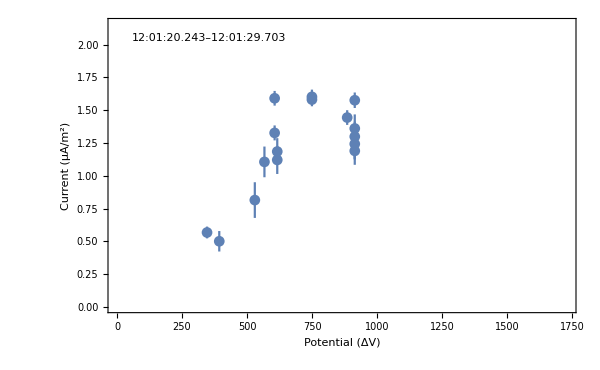
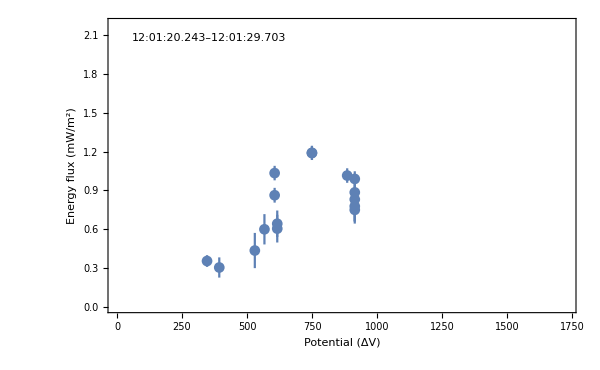

```mathematica
Switch[mType,
mType1,
Row[{tPlotInds[kappaInds,curs,curErrs,pRange,"Potential (ΔV)","Current (μA/m^2)"],tPlotInds[kappaInds,jes,curErrs,pRangeJe,"Potential (ΔV)","Energy flux (mW/m^2)"]}],
mType2,
Row[{tPlotInds[mWellInds,curs,curErrs,pRange,"Potential (ΔV)","Current (μA/m^2)"],tPlotInds[mWellInds,jes,curErrs,pRangeJe,"Potential (ΔV)","Energy flux (mW/m^2)"]}],
mType3,
Manipulate[Manipulate[Row[{tPlotRange[ind1,ind2,curs,curErrs,pRange,"Potential (ΔV)","Current (μA/m^2)"],tPlotRange[ind1,ind2,jes,jeErrs,pRangeJe,"Potential (ΔV)","Energy flux (mW/m^2)"]}],
{{ind1,Min[{ind1Init,ind1End}]},ind1Start,ind1End,1},
{{ind2,Max[{ind2Init,ind1End+1}]},ind1End+1,Length@pots,1}],
{{ind1End,ind1EndInit},2,Length@pots-2,1}]]
```

### Make a movie

```mathematica
{firstInd,lastInd1,lastInd2}={76,79,105};
```

```mathematica
plotMov = tablePlotMov[firstInd,lastInd1,lastInd2,curs,curErrs,pRange,"Potential (ΔV)","Current (μA/m^2)"];
```

```mathematica
plotMov2= tablePlotMov[firstInd,lastInd1,lastInd2,jes,jeErrs,pRangeJe,"Potential (ΔV)","Energy flux (mW/m^2)"];
```

```mathematica
(*movName=ToString@StringForm["orb`1`__J-V_and_JE-V__`2`_to_`3`.gif",orbit,time[[firstInd]],time[[lastInd2]]];*)
```

```mathematica
(*Export[movName,tablePlotsCombineAndAnimate[plotMov,plotMov2]]*)
```

```mathematica
tablePlotsCombineAndAnimate[plotMov,plotMov2]
```

The fits—J-V, J_E-V, and combined

## Initialize data for portions of arc in which we are interested

### Setup indices

```mathematica
(*True cavity #1, 2018/03/20 assays*)
```

```mathematica
inds1=Range[256,270]; 
inds2=Range[284,292];
```

#### Data set 1

```mathematica
(*True cavity + clean loss cone #1 and #2, 2018/03/21 assays*)
```

```mathematica
inds1=Range[232,249]+indShift;
inds2=Range[257,272]+indShift;
```

#### Data set 2

```mathematica
(*True cavity + clean loss cone #1 and #2, 2018/03/21 assays, using the modified data set and the observations from beginning of interval with ion pot struct below*)
```

```mathematica
(*Getting the good stuff, the good measurements—THESE ARE MAXWELLIAN*)
(*12:00:37.988through12:00:41.142 are bad/high wave activity*)
```

```mathematica
ind0Seg1=Range[12,44]; (*12:00:27.583 to 12:00:37.673*)
ind0Seg2=Range[56,84];(*12:00:41.457 to "12:00:50.286"*)
```

```mathematica
inds1=ind0Seg1~Join~ind0Seg2;
```

```mathematica
inds1=ind0Seg2;
```

```mathematica
(*Now kappas*)
```

```mathematica
inds1=Range[149,163];
```

```mathematica
inds2=Range[182,208];
```

```mathematica
inds3={3,4}~Join~inds2;
```

#### Data set 3

```mathematica
(*True cavity + clean loss cone #1 and #2, 2018/03/21 assays, using the modified data set and the observations from beginning of interval with ion pot struct below*)
```

```mathematica
(*Getting the good stuff, the good measurements—THESE ARE MAXWELLIAN*)
(*12:00:37.988through12:00:41.142 are bad/high wave activity*)
```

```mathematica
ind0Seg1=Range[5,15]; (*12:00:27.583 to 12:00:37.673*)
ind0Seg2=Range[19,28];(*12:00:41.457 to "12:00:50.286"*)
```

```mathematica
inds1=ind0Seg1~Join~ind0Seg2;
```

```mathematica
inds1=ind0Seg2;
```

```mathematica
(*Now kappas*)
```

```mathematica
inds1=Range[74,81];
```

```mathematica
inds2=Range[91,104];
```

```mathematica
inds2=Range[88,122];
```

```mathematica
inds3={3,4}~Join~inds2;
```

```mathematica
inds1=Range[57,80];(*Buck wild!*)
```

```mathematica
inds1=Range[87,105]~Join~Range[115,121];(*Buck wild!*)
```

```mathematica
inds1=Range[76,89];
```

```mathematica
inds1=Range[78,81]~Join~Range[85,92];
```

#### Data set 4

```mathematica
doMaxwellian=1;
```

```mathematica
(*True cavity + clean loss cone #1 and #2, 2018/03/21 assays, using the modified data set and the observations from beginning of interval with ion pot struct below*)
```

```mathematica
(*Getting the good stuff, the good measurements—THESE ARE MAXWELLIAN*)
(*12:00:37.988through12:00:41.142 are bad/high wave activity*)
```

```mathematica
(*If[dataset==4,
If[doMaxwellian,
ind0Seg1=Range[6,22]; (*12:00:27.583 to 12:00:37.673*)
ind0Seg2=Range[28,42](*12:00:41.457 to 12:00:50.286*);
inds1=ind0Seg1~Join~ind0Seg2;(*END Maxwellian*),
],]*)
```

```mathematica
If[doMaxwellian==1,ind0Seg1=Range[5,15]; (*12:00:27.583 to 12:00:37.673*)
ind0Seg2=Range[19,28](*12:00:41.457 to 12:00:50.286*);
inds1=ind0Seg1~Join~ind0Seg2;
(*inds1=ind0Seg2;*)]
```

```mathematica
(*Now kappas*)
```

```mathematica
(*inds1=Range[33,44]~Join~Range[46,49];*)
```

```mathematica
inds1=Range[33,44];
```

```mathematica
(*inds2=Range[56,78]; *)
```

```mathematica
inds2=Range[57,70]; (*Just clean stuff, no scary-low potentials or anything*)
```

```mathematica
inds3={3,4}~Join~inds2;
```

#### Data set 5

```mathematica
(*inds1=Range[46,53]~Join~Range[36,37];*)
```

### Instead, use intervals!

```mathematica
Switch[interval,"Maxwell",inds1=mWellInds;inds2=kappaInds;,"Kappa",inds1=kappaInds;inds2=mWellInds;]
```

## Fits: Initialize data, select indices to use, setup bounds and initial guesses

### Initialize plotData1, errorData1, plotDataWts1, etc. (takes stock of potTFactor)

Current data

```mathematica
{plotData1,plotData2,plotData3}=(Partition[Riffle[pots[[#]]+potTFactor,curs[[#]]],2])&/@{inds1,inds2,inds3};
```

```mathematica
{errorData1,errorData2,errorData3}=(makeErrorData[pots[[#]]+potTFactor,curs[[#]],curErrs[[#]]])&/@{inds1,inds2,inds3};
```

```mathematica
{plotDataWts1,plotDataWts2,plotDataWts3}=(1/(curErrs[[#]])^2)&/@{inds1,inds2,inds3};
```

Energy flux data

```mathematica
{jeData1,jeData2,jeData3}=(Partition[Riffle[pots[[#]]+potTFactor,jes[[#]]],2])&/@{inds1,inds2,inds3};
```

```mathematica
{errorJe1,errorJe2,errorJe3}=(makeErrorData[pots[[#]]+potTFactor,jes[[#]],jeErrs[[#]]])&/@{inds1,inds2,inds3};
```

```mathematica
{jeDataWts1,jeDataWts2,jeDataWts3}=(1/(jeErrs[[#]])^2)&/@{inds1,inds2,inds3};
```

### Which to use?

```mathematica
useinds1=1; (*Else use inds2*)
```

```mathematica
(*fitMethod="LevenbergMarquardt";*)
```

```mathematica
(*fitMethod="ConjugateGradient";*)
(*fitMethod="Gradient";*)
(*fitMethod="Newton";*)
```

```mathematica
fitMethod={"NMinimize",Method->"NelderMead"};
```

```mathematica
fitMethod={"NMinimize",Method->"DifferentialEvolution"};
```

```mathematica
fitMethod={"NMinimize",Method->"SimulatedAnnealing"};
```

```mathematica
fitMethod={"NMinimize",Method->"RandomSearch"};
```

```mathematica
fitMethod=Automatic;
```

```mathematica
If[Length@fitMethod==2,fitMethodString=ToString@StringForm["`1`__`2`",fitMethod[[1]],ToString@Values@fitMethod[[2]]],fitMethodString=fitMethod];
```

### Bounds

```mathematica
minFitT=150;
maxFitT=350;
minFitRB=4;
maxFitRB=100;
minFitN=0.04;
maxFitN=10;
minFitKappa=1.51;
maxFitKappa=10.;
```

```mathematica
kConstraints={minFitRB<kFitRB<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gConstraints={minFitRB<gFitRB<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

```mathematica
kCombConstraints={minFitRB<kFitRB<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gCombConstraints={minFitRB<gFitRB<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

```mathematica
kDoubledConstraints={minFitRB<kFitRB1<maxFitRB,minFitRB<kFitRB2<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gDoubledConstraints={minFitRB<gFitRB1<maxFitRB,minFitRB<gFitRB2<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

#### Unconstrain if fitMethod requires it

```mathematica
If[Head@fitMethod==String,If[
fitMethod=="LevenbergMarquardt"||fitMethod=="ConjugateGradient",kConstraints=None;gConstraints=None;kCombConstraints=None;gCombConstraints=None;kDoubledConstraints=None;gDoubledConstraints=None;]];
```

### Initial guesses

```mathematica
kFitNinit=0.5;
kFitTinit=100;
kFitRBinit=10;
kFitKappainit=10;
kFitRB1init=10;
kFitRB2init=10;
```

```mathematica
gFitNinit=0.5;
gFitTinit=100;
gFitRBinit=10;
gFitRB1init=10;
gFitRB2init=10;
```

### Init fit data

Maxwellian-ish thing?

```mathematica
If[useinds1==1,Print["Using inds1 ..."];indsInUse=inds1;jData=plotData1;jWts=plotDataWts1;jErrData=errorData1;jeData=jeData1;jeWts=jeDataWts1;jeErrData=errorJe1;,Print["Using inds2 ..."];indsInUse=inds2;jData=plotData2;jWts=plotDataWts2;jErrData=errorData2;jeData=jeData2;jeWts=jeDataWts2;jeErrData=errorJe2;];
```

Using inds1 ...

## Nonlinear J-V fits

### Now the actual fits

```mathematica
(*kConstraints={0.01<kFitN<10,10<kFitT<4000,3<kFitRB<1000000,1.501<kFitKappa<20};
gConstraints={0.01<gFitN<10,10<gFitT<4000,3<gFitRB<1000000};*)
```

```mathematica
kModel = JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa];
```

```mathematica
gModel = JVMaxwellian[pot,gFitRB,gFitT,gFitN];
```

```mathematica
count=0;
{kFit,{kFitStepVals}}=Reap[NonlinearModelFit[jData,(If[Length@kConstraints≠0,{kModel,kConstraints},kModel]),{{kFitN,kFitNinit},{kFitT,kFitTinit},{kFitRB,kFitRBinit},{kFitKappa,kFitKappainit}},pot,Weights->jWts,VarianceEstimatorFunction->(1&),Method->fitMethod,StepMonitor:> Sow[{kFitRB,kFitT,kFitN,kFitKappa,count++}]]];
```

```mathematica
{gFit,{gFitStepVals}}=Reap[NonlinearModelFit[jData,{gModel,gConstraints},{{gFitN,gFitNinit},{gFitT,gFitTinit},{gFitRB,gFitRBinit}},pot,Weights->jWts,VarianceEstimatorFunction->(1&),Method->fitMethod,StepMonitor:> Sow[{gFitRB,gFitT,gFitN,count++}]]];
```

```mathematica
kDOF=Length[pots[[inds1]]]-4;
```

```mathematica
gDOF=Length[pots[[inds1]]]-3;
```

```mathematica
{kBestN,kBestT,kBestRB,kBestKappa,kBestChi2red}=Values@kFit["BestFitParameters"]~Join~{Total[(kFit["FitResiduals"])^2*jWts]/kDOF};
```

```mathematica
{gBestN,gBestT,gBestRB,gBestChi2red}=Values@gFit["BestFitParameters"]~Join~{Total[(gFit["FitResiduals"])^2*jWts]/gDOF};
```

## Nonlinear J_E-V fits

### Now the actual fits

```mathematica
(*kConstraints={0.01<kFitN<10,100<kFitT<4000,3<kFitRB<1000,1.51<kFitKappa<20};
gConstraints={0.01<gFitN<10,100<gFitT<4000,3<gFitRB<1000};*)
```

```mathematica
kModelJeV = JEVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa];
```

```mathematica
gModelJeV = JEVMaxwellian[pot,gFitRB,gFitT,gFitN];
```

```mathematica
count=0;
{kFitJeV,{kFitJeVStepVals}}=Reap[NonlinearModelFit[jeData,{kModelJeV,kConstraints},{{kFitN,kFitNinit},{kFitT,kFitTinit},{kFitRB,kFitRBinit},{kFitKappa,kFitKappainit}},pot,Weights->jeWts,VarianceEstimatorFunction->(1&),Method->fitMethod,StepMonitor:> Sow[{kFitRB,kFitT,kFitN,kFitKappa,count++}]]];
```

```mathematica
count=0;
{gFitJeV,{gFitJeVStepVals}}=Reap[NonlinearModelFit[jeData,{gModelJeV,gConstraints},{{gFitN,gFitNinit},{gFitT,gFitRBinit},{gFitRB,gFitRBinit}},pot,Weights->jeWts,VarianceEstimatorFunction->(1&),Method->fitMethod,StepMonitor:> Sow[{gFitRB,gFitT,gFitN,count++}]]];
```

```mathematica
kDOF=Length[pots[[inds1]]]-4;
```

```mathematica
gDOF=Length[pots[[inds1]]]-3;
```

```mathematica
{kBestJeVN,kBestJeVT,kBestJeVRB,kBestJeVKappa,kBestJeVChi2red}=Values@kFitJeV["BestFitParameters"]~Join~{Total[(kFitJeV["FitResiduals"])^2*jeWts]/kDOF};
```

```mathematica
{gBestJeVN,gBestJeVT,gBestJeVRB,gBestJeVChi2red}=Values@gFitJeV["BestFitParameters"]~Join~{Total[(gFitJeV["FitResiduals"])^2*jeWts]/gDOF};
```

## Now J-V and J_E-V fits simultaneously!

```mathematica
(*RBinit=kBestRB;Tminit=kBestT;nminit=kBestN;kappainit=kBestKappa;*)
```

```mathematica
(*RBinit=kBestJeVRB;Tminit=kBestJeVT;nminit=kBestJeVN;kappainit=kBestJeVKappa;*)
```

```mathematica
combDat = Join[jData/.{x_,y_}->{1,x,y},jeData/.{x_,y_}->{2,x,y}];
```

```mathematica
combWts=jWts~Join~jeWts;
```

```mathematica
kCombFitModel[set_,pot_,kFitRB,kFitT_,kFitN_,kFitKappa_]:=Which[set==1,Evaluate@JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa],set==2,Evaluate@JEVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa]];
```

```mathematica
gCombFitModel[set_,pot_,gFitRB,gFitT_,gFitN_]:=Which[set==1,Evaluate@JVMaxwellian[pot,gFitRB,gFitT,gFitN],set==2,Evaluate@JEVMaxwellian[pot,gFitRB,gFitT,gFitN]];
```

```mathematica
count=0;
{kCombFit,{kCombStepVals}}=Reap[NonlinearModelFit[combDat,{kCombFitModel[set,pot,kFitRB,kFitT,kFitN,kFitKappa],kCombConstraints},{{kFitRB,kFitRBinit},{kFitT,kFitTinit},{kFitN,kFitNinit},{kFitKappa,kFitKappainit}},{set,pot},Weights->combWts,Method->fitMethod,MaxIterations->1000,VarianceEstimatorFunction->(1&),(*EvaluationMonitor:>Print["kFitRB=",kFitRB,".  kFitT=",kFitT,";  kFitN=",kFitN,";  κ=",kFitKappa]*)StepMonitor:> Sow[{kFitRB,kFitT,kFitN,kFitKappa,count++}]]];
```

```mathematica
count=0;
{gCombFit,{gCombStepVals}}=Reap[NonlinearModelFit[combDat,{gCombFitModel[set,pot,gFitRB,gFitT,gFitN],gCombConstraints},{{gFitRB,gFitRBinit},{gFitT,gFitTinit},{gFitN,gFitNinit}},{set,pot},Weights->combWts,VarianceEstimatorFunction->(1&),Method->fitMethod,StepMonitor:> Sow[{gFitRB,gFitT,gFitN,count++}]]];
```

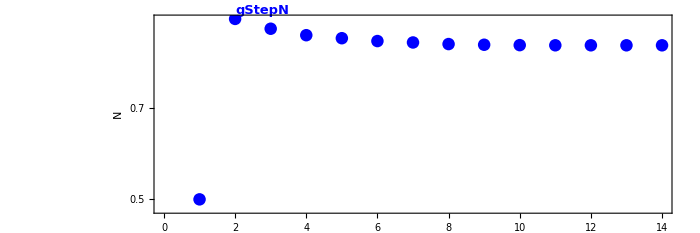
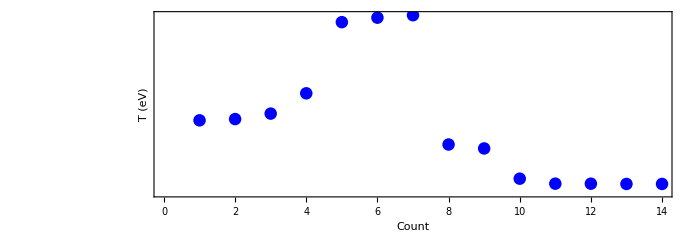
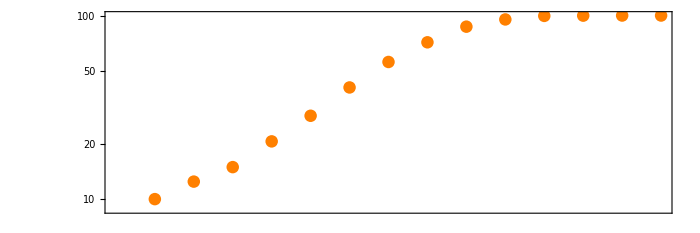

```mathematica
gPlotStepMonitorData[gCombStepVals]
```

```mathematica
kCombDOF=Length[combDat[[;;,1]]]-4;
```

```mathematica
gCombDOF=Length[combDat[[;;,1]]]-3;
```

```mathematica
{kCombRB,kCombT,kCombN,kCombKappa,kCombChi2red}=Values@kCombFit["BestFitParameters"]~Join~{Total[(kCombFit["FitResiduals"])^2*combWts]/kCombDOF};
```

```mathematica
{gCombRB,gCombT,gCombN,gCombChi2red}=Values@gCombFit["BestFitParameters"]~Join~{Total[(gCombFit["FitResiduals"])^2*combWts]/gCombDOF};
```

Plots

### Setup plot ranges

```mathematica
minPot=Min[pots[[;;]] ]* 8/10;maxPot=Max[pots[[indsInUse]]]*1.1;(*maxPot=Max[pots[[;;]]];*)
```

```mathematica
minJ=0;maxJ=Max[curs[[indsInUse]]]*1.1;
```

```mathematica
minJe=0;maxJe=Max[jes[[indsInUse]]]*1.1;
```

### Setup combined fit plots

```mathematica
parNames=Style[#,Bold]&/@{"T_m    : ","n_m    : ","R_B   : ","χ_red^2   :"};
pTableVSpace=0.5;
pTableFontSize=14;
pTableScaledLoc={0.12,0.65};
```

```mathematica
titleSize=20;
```

```mathematica
axesLabelSize=18;
```

```mathematica
JVRepl={gRB->gBestRB,gTm->gBestT,gnm->gBestN,gChi2->gBestChi2red,kRB->kBestRB,kTm->kBestT,knm->kBestN,kappa->kBestKappa,kChi2->kBestChi2red};
```

```mathematica
JeVRepl={gRB->gBestJeVRB,gTm->gBestJeVT,gnm->gBestJeVN,gChi2->gBestJeVChi2red,kRB->kBestJeVRB,kTm->kBestJeVT,knm->kBestJeVN,kappa->kBestJeVKappa,kChi2->kBestJeVChi2red};
```

```mathematica
combRepl={gRB->gCombRB,gTm->gCombT,gnm->gCombN,gChi2->gCombChi2red,kRB->kCombRB,kTm->kCombT,knm->kCombN,kappa->kCombKappa,kChi2->kCombChi2red};
```

```mathematica
(*gVals=MapThread[NumberForm,{({gTm,gnm,gRB}/.combRepl),{{3,0},{3,2},{3,1}}}];
kVals=MapThread[NumberForm,{({kTm,knm,kRB}/.combRepl),{{3,0},{3,2},{3,1}}}];*)
```

```mathematica
gJVVals=(MapThread[NumberForm,{({gTm,gnm}/.JVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[gRB,3]/.JVRepl}~Join~{NumberForm[gChi2,3]/.JVRepl};
kJVVals=(MapThread[NumberForm,{({kTm,knm}/.JVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[kRB,3]/.JVRepl}~Join~{NumberForm[kChi2,3]/.JVRepl};
```

```mathematica
gJeVVals=(MapThread[NumberForm,{({gTm,gnm}/.JeVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[gRB,3]/.JeVRepl}~Join~{NumberForm[gChi2,3]/.JeVRepl};
kJeVVals=(MapThread[NumberForm,{({kTm,knm}/.JeVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[kRB,3]/.JeVRepl}~Join~{NumberForm[kChi2,4]/.JeVRepl};
```

```mathematica
gCombVals=(MapThread[NumberForm,{({gTm,gnm}/.combRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[gRB,3]/.combRepl}~Join~{NumberForm[gChi2,4]/.combRepl};
kCombVals=(MapThread[NumberForm,{({kTm,knm}/.combRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[kRB,3]/.combRepl}~Join~{NumberForm[kChi2,4]/.combRepl};
```

```mathematica
JVParTable=Text[Grid[Transpose[{{Style["Maxwell",Bold,(ColorData[97,"ColorList"])[[1]]]}~Join~parNames~Join~{Style["Kappa  :",Bold,(ColorData[97,"ColorList"])[[2]]]}~Join~parNames,{""}~Join~gJVVals~Join~{(ToString@StringForm["`1`",NumberForm[kBestKappa,3]])}~Join~kJVVals}],Alignment->".",Spacings->{0,pTableVSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
JeVParTable=Text[Grid[Transpose[{{Style["Maxwell",Bold,(ColorData[97,"ColorList"])[[1]]]}~Join~parNames~Join~{Style["Kappa  :",Bold,(ColorData[97,"ColorList"])[[2]]]}~Join~parNames,{""}~Join~gJeVVals~Join~{(ToString@StringForm["`1`",NumberForm[kBestJeVKappa,3]])}~Join~kJeVVals}],Alignment->".",Spacings->{0,pTableVSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
combParTable=Text[Grid[Transpose[{{Style["Maxwell",Bold,(ColorData[97,"ColorList"])[[1]]]}~Join~parNames~Join~{Style["Kappa",Bold,(ColorData[97,"ColorList"])[[2]]]}~Join~parNames,{""}~Join~gCombVals~Join~{(ToString@StringForm["`1`",NumberForm[kCombKappa,3]])}~Join~kCombVals}],Alignment->".",Spacings->{0,pTableVSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
combTitle=StringJoin@Riffle[time[[indsInUse[[{1,-1}]]]],"–"];
```

```mathematica
(*PlotLegends->Map[(Style[#,axesLabelSize])&,{"Maxwellian",StringForm["κ = `1`",NumberForm[(kappa/.combRepl),{3,3}]]}],*)
```

```mathematica
combFitJVPlot=Plot[Evaluate@(({JVMaxwellian[pot,gRB,gTm,gnm],JVKappa[pot,kRB,kTm,knm,kappa]})/.combRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJ,maxJ}},Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"",Style[StringForm["J-V and J_E-V Simultaneous Fit (`1`)",combTitle],Bold,titleSize]}},ImageSize->800,FrameStyle->Directive[Black,axesLabelSize],FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},Epilog->Inset[combParTable,Scaled[pTableScaledLoc]]];
```

```mathematica
combFitJeVPlot=Plot[Evaluate@(({JEVMaxwellian[pot,gRB,gTm,gnm],JEVKappa[pot,kRB,kTm,knm,kappa]})/.combRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJe,maxJe}},Frame->True,FrameLabel->{{"j_(E||, i) (mW/m^2)",""},{"ΔΦ (V)",""}},ImageSize->800,FrameStyle->Directive[Black,axesLabelSize]];
```

```mathematica
combJVPlot=Show[combFitJVPlot,ErrorListPlot[jErrData,PlotStyle->Gray]];
```

```mathematica
combJeVPlot=Show[combFitJeVPlot,ErrorListPlot[jeErrData,PlotStyle->Gray]];
```

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/plots/"<>(ToString@DateString[{"Year","Month","Day","/"}]);
```

```mathematica
If[!FileExistsQ[dir],Print["Nei!"];CreateDirectory[dir];Print["Nå har du det!"],Print["Ja!"]]
```

Ja!

```mathematica
orbPref=ToString@StringForm["Orb`1`",orbit];
```

```mathematica
JVPref="JVFit";
JeVPref="JeVFit";
combPref="combJVJeVFit";
doubledPref="twoIntervals__combJVJeVFit";
```

```mathematica
mkFN[fPref_,dir_]:=Module[{tmpFN,count},
count=1;
tmpFN=ToString@StringForm["`1`__`2``3`__inds_`4`-`5`__`6`.png",orbPref,fPref,potFactorString,indsInUse[[1]],indsInUse[[-1]],fitMethodString];
While[FileExistsQ[dir<>tmpFN],
tmpFN=ToString@StringForm["`1`__`2``3`__inds_`4`-`5`__`6`__`7`.png",orbPref,fPref,potFactorString,indsInUse[[1]],indsInUse[[-1]],fitMethodString,NumberForm[n,1,NumberPadding->{"0", ""}]];
];
outFN=tmpFN]
```

```mathematica
{JVFilename,JeVFilename,combFilename,doubledFilename}=(mkFN[#,dir])&/@{JVPref,JeVPref,combPref,doubledPref}
```

$Aborted

### J-V plot

```mathematica
(*PlotLegends->((Style[#,20])&/@{"Maxwellian",StringForm["κ = `1`",NumberForm[kBestKappa,{3,2}]]}),Frame->True,*)
```

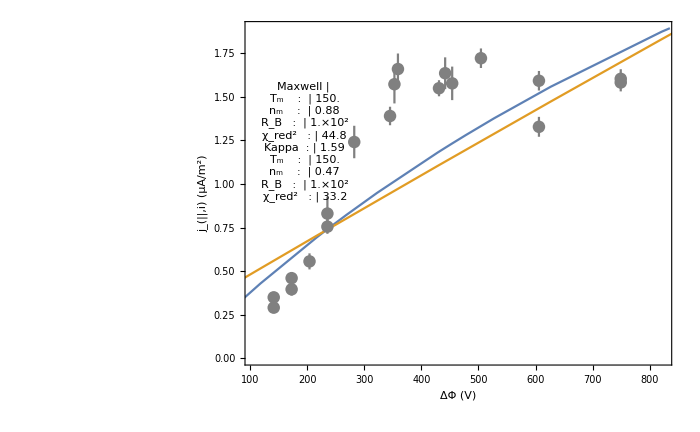

```mathematica
JVPlot=Show[Plot[{kFit[pot],gFit[pot]},{pot,20,10000},PlotRange->{{minPot,maxPot},{minJ,maxJ}},Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["J-V Fit (`1`)",combTitle],Bold,titleSize]}},ImageSize->700,FrameStyle->Directive[Black,axesLabelSize],Epilog->Inset[JVParTable,Scaled[{0.14,0.65}]]],ErrorListPlot[jErrData,PlotStyle->Gray]]
```

### J_E-V plot

```mathematica
(*PlotLegends->((Style[#,20])&/@{"Maxwellian",StringForm["κ = `1`",NumberForm[kBestJeVKappa,{3,2}]]}),*)
```

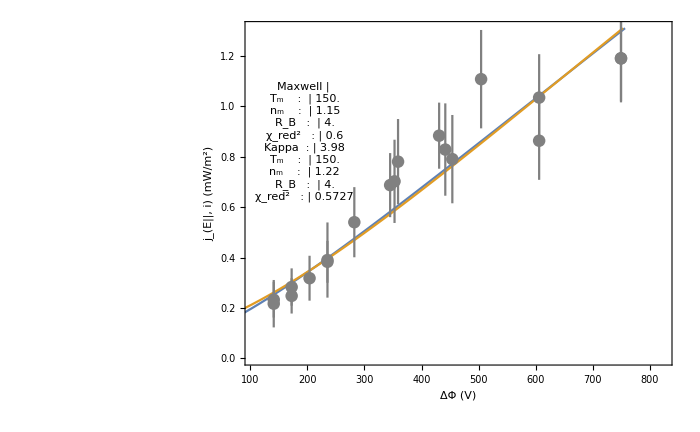

```mathematica
JeVPlot=Show[Plot[{kFitJeV[pot],gFitJeV[pot]},{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJe,maxJe}},Frame->True,FrameLabel->{{"j_(E||, i) (mW/m^2)",""},{"ΔΦ (V)",Style[StringForm["J_E-V Fit (`1`)",combTitle],Bold,titleSize]}},ImageSize->700,FrameStyle->Directive[Black,axesLabelSize],Epilog->Inset[JeVParTable,Scaled[{0.14,0.65}]]],ErrorListPlot[jeErrData,PlotStyle->Gray]]
```

### Plots from combined fit

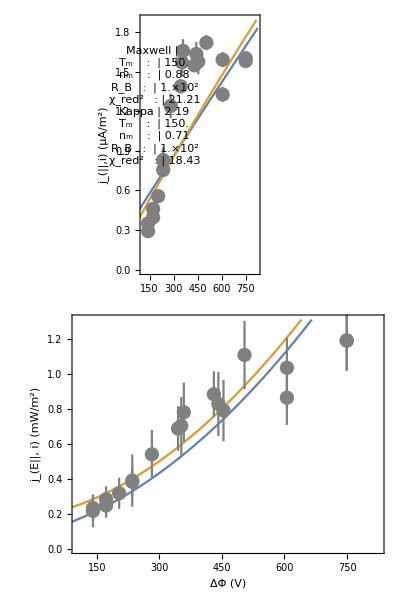

```mathematica
combPlot=Column[{combJVPlot,combJeVPlot}]
```

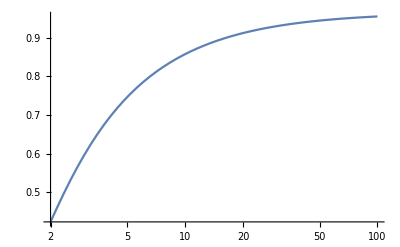

```mathematica
LogLinearPlot[LKMwellDensFac[100/50,RB],{RB,2,100},PlotRange->Full]
```

#### Save plots

```mathematica
If[makePlots==1,Print["Making plots in "<>dir<>" ..."];
Print[JVFilename<>" ..."];
Export[dir<>JVFilename,JVPlot];Print[JeVFilename<>" ..."];Export[dir<>JeVFilename,JeVPlot];Print[combFilename<>" ..."];Export[dir<>combFilename,combPlot];
Print["Done!"]]
```

Making plots in /SPENCEdata/Research/Satellites/FAST/kappa_dists/plots/20180327/ ...

Orb1612__JVFit__inds_75-93__Automatic__n.png ...

Orb1612__JeVFit__inds_75-93__Automatic__n.png ...

Orb1612__combJVJeVFit__inds_75-93__Automatic__n.png ...

Done!

Now everything at once

### Bounds

```mathematica
minFitT=10;
maxFitT=1000;
minFitRB=2;
maxFitRB=100000;
minFitN=0.01;
maxFitN=10;
minFitKappa=1.501;
maxFitKappa=35;
```

```mathematica
kConstraints={minFitRB<kFitRB<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gConstraints={minFitRB<gFitRB<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

```mathematica
kCombConstraints={minFitRB<kFitRB<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gCombConstraints={minFitRB<gFitRB<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

```mathematica
kDoubledConstraints={minFitRB<kFitRB1<maxFitRB,minFitRB<kFitRB2<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gDoubledConstraints={minFitRB<gFitRB1<maxFitRB,minFitRB<gFitRB2<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

### Initial guesses

```mathematica
kFitNinit=1;
kFitTinit=300;
kFitRBinit=10;
kFitKappainit=10;
kFitRB1init=10;
kFitRB2init=10;
```

```mathematica
gFitNinit=1;
gFitTinit=300;
gFitRBinit=10;
gFitRB1init=10;
gFitRB2init=10;
```

### Setup indices

```mathematica
indsSeg1=inds1;
```

```mathematica
indsSeg2=inds2;
```

```mathematica
(*indsSeg2=Range[162,198]; (*Alt*)*)
```

### Initialize plotData1, errorData1, plotDataWts1, etc.

Current data

```mathematica
{jDataSeg1,jDataSeg2}=(Partition[Riffle[pots[[#]]+potTFactor,curs[[#]]],2])&/@{indsSeg1,indsSeg2};
```

```mathematica
{jErrDataSeg1,jErrDataSeg2}=(makeErrorData[pots[[#]]+potTFactor,curs[[#]],curErrs[[#]]])&/@{indsSeg1,indsSeg2};
```

```mathematica
{jWtsSeg1,jWtsSeg2}=(1/(curErrs[[#]])^2)&/@{indsSeg1,indsSeg2};
```

Energy flux data

```mathematica
{jeDataSeg1,jeDataSeg2}=(Partition[Riffle[pots[[#]]+potTFactor,jes[[#]]],2])&/@{indsSeg1,indsSeg2};
```

```mathematica
{jeErrDataSeg1,jeErrDataSeg2}=(makeErrorData[pots[[#]]+potTFactor,jes[[#]],jeErrs[[#]]])&/@{indsSeg1,indsSeg2};
```

```mathematica
{jeWtsSeg1,jeWtsSeg2}=(1/(jeErrs[[#]])^2)&/@{indsSeg1,indsSeg2};
```

```mathematica
RBinit=kBestRB;Tminit=kBestT;nminit=kBestN;kappainit=kBestKappa;
```

```mathematica
combDatSeg1 = Join[jDataSeg1/.{x_,y_}->{1,x,y},jeDataSeg1/.{x_,y_}->{2,x,y}];
```

```mathematica
combDatSeg2 = Join[jDataSeg2/.{x_,y_}->{1,x,y},jeDataSeg2/.{x_,y_}->{2,x,y}];
```

```mathematica
combWtsSeg1=jWtsSeg1~Join~jeWtsSeg1;
```

```mathematica
combWtsSeg2=jWtsSeg2~Join~jeWtsSeg2;
```

```mathematica
doubledDat= Join[jDataSeg1/.{x_,y_}->{1,x,y},jeDataSeg1/.{x_,y_}->{2,x,y},jDataSeg2/.{x_,y_}->{3,x,y},jeDataSeg2/.{x_,y_}->{4,x,y}];
```

```mathematica
doubledWts=jWtsSeg1~Join~jeWtsSeg1~Join~jWtsSeg2~Join~jeWtsSeg2;
```

### Now the doubled double model

```mathematica
kDoubledFitModel[set_,pot_,kFitRB1_,kFitRB2_,kFitT_,kFitN_,kFitKappa_]:=Which[set==1,Evaluate@JVKappa[pot,kFitRB1,kFitT,kFitN,kFitKappa],set==2,Evaluate@JEVKappa[pot,kFitRB1,kFitT,kFitN,kFitKappa],set==3,Evaluate@JVKappa[pot,kFitRB2,kFitT,kFitN,kFitKappa],set==4,Evaluate@JEVKappa[pot,kFitRB2,kFitT,kFitN,kFitKappa]]
```

```mathematica
gDoubledFitModel[set_,pot_,gFitRB1_,gFitRB2_,gFitT_,gFitN_]:=Which[set==1,Evaluate@JVMaxwellian[pot,gFitRB1,gFitT,gFitN],set==2,Evaluate@JEVMaxwellian[pot,gFitRB1,gFitT,gFitN],set==3,Evaluate@JVMaxwellian[pot,gFitRB2,gFitT,gFitN],set==4,Evaluate@JEVMaxwellian[pot,gFitRB2,gFitT,gFitN]]
```

```mathematica
kDoubledFit=NonlinearModelFit[doubledDat,{kDoubledFitModel[set,pot,kFitRB1,kFitRB2,kFitT,kFitN,kFitKappa],kDoubledConstraints},{{kFitN,kFitNinit},{kFitT,kFitTinit},{kFitRB1,kFitRB1init},{kFitRB2,kFitRB2init},{kFitKappa,kFitKappainit}},{set,pot},Weights->doubledWts,VarianceEstimatorFunction->(1&),Method->fitMethod]
```

FittedModel[Which[set==1,(0.0266987 «4» Gamma[«1»])/((1-1/(«19»)) «1» Gamma[«1»]),«4»,set==4,(0.0000268059 «6» Gamma[1+2.00118])/((-2+2.00118) (-1+2.00118) Gamma[-1/2+2.00118])]]

```mathematica
gDoubledFit=NonlinearModelFit[doubledDat,{gDoubledFitModel[set,pot,gFitRB1,gFitRB2,gFitT,gFitN],gDoubledConstraints},{{gFitN,gFitNinit},{gFitT,gFitTinit},{gFitRB1,gFitRB1init},{gFitRB2,gFitRB2init}},{set,pot},Weights->doubledWts,VarianceEstimatorFunction->(1&),Method->fitMethod]
```

FittedModel[Which[set==1,«1»,«4»,set==4,0.0000268059 0.349183 98.7338 («19»)^(3/2) (2+pot/10.-ⅇ^(-pot/((-1+98.7338) «19»)) (2 (1-1/98.7338)+pot/10.))]]

```mathematica
kDOF=Length[doubledDat[[;;,1]]]-4;
```

```mathematica
gDOF=Length[doubledDat[[;;,1]]]-3;
```

```mathematica
{kDoubledN,kDoubledT,kDoubledRB1,kDoubledRB2,kDoubledKappa,kDoubledChi2red}=Values@kDoubledFit["BestFitParameters"]~Join~{Total[(kDoubledFit["FitResiduals"])^2*doubledWts]/kDOF};
```

```mathematica
{gDoubledN,gDoubledT,gDoubledRB1,gDoubledRB2,gDoubledChi2red}=Values@gDoubledFit["BestFitParameters"]~Join~{Total[(gDoubledFit["FitResiduals"])^2*doubledWts]/gDOF};
```

### Graphic options

```mathematica
doubledTitlePref="J-V, J_E-V Simult. Fit (`1`)";
```

```mathematica
(*getPadding[g_]:=Module[{im},im=Image[Show[g,LabelStyle->White,Background->White]];
BorderDimensions[im]]*)
```

```mathematica
imgSize=600;
```

```mathematica
{yTitlePad,xTitlePad,topTitlePad}={70,50,50};
{rPad,bPad,blankPad}={25,10,10};
```

```mathematica
TLPad={{yTitlePad,rPad},{bPad,topTitlePad}};
TRPad={{yTitlePad,rPad},{bPad,topTitlePad}};
BLPad={{yTitlePad,rPad},{xTitlePad,blankPad}};
BRPad={{yTitlePad,rPad},{xTitlePad,blankPad}};
```

```mathematica
imgPadding={{60,10},{50,50}};
```

### Setup plot ranges

```mathematica
minPot=Min[pots[[;;]] ]* 8/10;{maxPot1,maxPot2}=(Max[pots[[#]]]*1.2)&/@{indsSeg1,indsSeg2};(*maxPot=Max[pots[[;;]]];*)
```

```mathematica
minJ=0;
{maxJ1,maxJ2}=(Max[curs[[#]]]*1.3)&/@{indsSeg1,indsSeg2};
```

```mathematica
{maxJe1,maxJe2}=(Max[jes[[#]]]*1.3)&/@{indsSeg1,indsSeg2};
```

### Now setup plots

```mathematica
(*Epilog->Inset[JVParTable,Scaled[{0.14,0.65}]]*)
```

```mathematica
(*JVPlotSeg1=Show[Plot[{JVMaxwellian[pot,gDoubledRB1,gDoubledT,gDoubledN],JVKappa[pot,kDoubledRB1,kDoubledT,kDoubledN,kDoubledKappa]},{pot,minPot,maxPot},PlotRange->{{minPot,maxPot},{minJ,maxJ}},PlotLegends->((Style[#,20])&/@{"Maxwellian",StringForm["κ = `1`",NumberForm[kDoubledKappa,{3,2}]]}),Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["J-V Fit (`1`)",combTitle],Bold,25]}},ImageSize->700,FrameStyle->Directive[Black,axesLabelSize]],ErrorListPlot[jErrDataSeg1,PlotStyle->Gray]]*)
```

```mathematica
doubledRepl={gRB1->gDoubledRB1,gRB2->gDoubledRB2,gTm->gDoubledT,gnm->gDoubledN,gChi2->gDoubledChi2red,kRB1->kDoubledRB1,kRB2->kDoubledRB2,kTm->kDoubledT,knm->kDoubledN,kappa->kDoubledKappa,kChi2->kDoubledChi2red};
```

```mathematica
gDoubledVals1=(MapThread[NumberForm,{({gTm,gnm}/.doubledRepl),{{3,0},{3,2}}}])~Join~{NumberForm[gRB1,3]/.doubledRepl}~Join~{NumberForm[gChi2,4]/.doubledRepl};
kDoubledVals1=(MapThread[NumberForm,{({kTm,knm}/.doubledRepl),{{3,0},{3,2}}}])~Join~{NumberForm[kRB1,3]/.doubledRepl}~Join~{NumberForm[kChi2,4]/.doubledRepl};
```

```mathematica
gDoubledVals2=(MapThread[NumberForm,{({gTm,gnm}/.doubledRepl),{{3,0},{3,2}}}])~Join~{NumberForm[gRB2,3]/.doubledRepl}~Join~{NumberForm[gChi2,4]/.doubledRepl};
kDoubledVals2=(MapThread[NumberForm,{({kTm,knm}/.doubledRepl),{{3,0},{3,2}}}])~Join~{NumberForm[kRB2,3]/.doubledRepl}~Join~{NumberForm[kChi2,4]/.doubledRepl};
```

#### Parameter tables

```mathematica
doubledParTable1=Text[Grid[Transpose[{{Style["Maxwell",Bold,(ColorData[97,"ColorList"])[[1]]]}~Join~parNames~Join~{"",Style["Kappa  :",Bold,(ColorData[97,"ColorList"])[[2]]]}~Join~parNames,{""}~Join~gDoubledVals1~Join~{"",(ToString@StringForm["`1`",NumberForm[kDoubledKappa,3]])}~Join~kDoubledVals1}],Alignment->".",Spacings->{0,pTableVSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
doubledParTable2=Text[Grid[Transpose[{{Style["Maxwell",Bold,(ColorData[97,"ColorList"])[[1]]]}~Join~parNames~Join~{"",Style["Kappa  :",Bold,(ColorData[97,"ColorList"])[[2]]]}~Join~parNames,{""}~Join~gDoubledVals2~Join~{"",(ToString@StringForm["`1`",NumberForm[kDoubledKappa,3]])}~Join~kDoubledVals2}],Alignment->".",Spacings->{0,pTableVSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
doubledTitle1=StringJoin@Riffle[time[[indsSeg1[[{1,-1}]]]],"–"];
```

```mathematica
doubledTitle2=StringJoin@Riffle[time[[indsSeg2[[{1,-1}]]]],"–"];
```

### Plots (to be shown momentarily)

```mathematica
doubledFitJVPlot1=Plot[Evaluate@(({JVMaxwellian[pot,gRB1,gTm,gnm],JVKappa[pot,kRB1,kTm,knm,kappa]})/.doubledRepl),{pot,20,maxPot1},PlotRange->{{minPot,maxPot1},{minJ,maxJ1}},Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",None},{None,Style[StringForm[doubledTitlePref,doubledTitle1],Bold,titleSize]}},ImageSize->imgSize,ImagePadding->TLPad,FrameStyle->Directive[Black,axesLabelSize],FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},Epilog->Inset[doubledParTable1,Scaled[pTableScaledLoc]]];
```

```mathematica
doubledFitJeVPlot1=Plot[Evaluate@(({JEVMaxwellian[pot,gRB1,gTm,gnm],JEVKappa[pot,kRB1,kTm,knm,kappa]})/.doubledRepl),{pot,20,maxPot1},PlotRange->{{minPot,maxPot1},{minJe,maxJe1}},Frame->True,FrameLabel->{{"j_(E||, i) (mW/m^2)",""},{"ΔΦ (V)",""}},FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->imgSize,ImagePadding->BLPad,FrameStyle->Directive[Black,axesLabelSize]];
```

```mathematica
(*Was going to be the version without the legend that works with getPadding function; for some reason the Show function in getPadding hates legends … *)
(*doubledFitJVPlot2NOLEG=Plot[Evaluate@(({JVMaxwellian[pot,gRB2,gTm,gnm],JVKappa[pot,kRB2,kTm,knm,kappa]})/.doubledRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJ,maxJ}},Frame->True,FrameLabel->{{"",""},{"",Style[StringForm[doubledTitlePref,doubledTitle2],Bold,titleSize]}},ImageSize->imgSize,FrameStyle->Directive[Black,axesLabelSize],FrameTicksStyle->{{Directive[FontOpacity->0,FontSize->0],Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},Epilog->Inset[doubledParTable2,Scaled[pTableScaledLoc]]];*)
```

```mathematica
doubledFitJVPlot2=Plot[Evaluate@(({JVMaxwellian[pot,gRB2,gTm,gnm],JVKappa[pot,kRB2,kTm,knm,kappa]})/.doubledRepl),{pot,20,maxPot2},PlotRange->{{minPot,maxPot2},{minJ,maxJ2}},Frame->True,FrameLabel->{{None,None},{None,Style[StringForm[doubledTitlePref,doubledTitle2],Bold,titleSize]}},ImageSize->imgSize,ImagePadding->TRPad,FrameStyle->Directive[Black,axesLabelSize],FrameTicksStyle->{{Directive[FontOpacity->0,FontSize->0],Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},Epilog->Inset[doubledParTable2,Scaled[pTableScaledLoc]]];
```

```mathematica
(*PlotLegends->Map[(Style[#,axesLabelSize])&,{"Maxwellian",StringForm["κ = `1`",NumberForm[(kappa/.doubledRepl),{3,3}]]}],*)
```

```mathematica
doubledFitJeVPlot2=Plot[Evaluate@(({JEVMaxwellian[pot,gRB2,gTm,gnm],JEVKappa[pot,kRB2,kTm,knm,kappa]})/.doubledRepl),{pot,20,maxPot2},PlotRange->{{minPot,maxPot2},{minJe,maxJe2}},Frame->True,FrameLabel->{{None,None},{"ΔΦ (V)",None}},ImageSize->imgSize,ImagePadding->BRPad,FrameStyle->Directive[Black,axesLabelSize],FrameTicksStyle->{{Directive[FontOpacity->0,FontSize->0],Automatic},{Automatic,Automatic}}];
```

```mathematica
(*{p1h,p1v}=getPadding[doubledFitJVPlot1];
{p2h,p2v}=getPadding[doubledFitJVPlot2];*)
```

```mathematica
(*verticalPadding=Max/@Transpose[{p1v,p2v}];*)
```

```mathematica
(*doubledJVPlot1=Show[{doubledFitJVPlot1,ErrorListPlot[jErrDataSeg1,PlotStyle->Gray]},ImagePadding-> {p1h,verticalPadding}];*)
```

```mathematica
(*doubledJVPlot2=Show[{doubledFitJVPlot2,ErrorListPlot[jErrDataSeg2,PlotStyle->Gray]},ImagePadding->{p2h,verticalPadding}];*)
```

```mathematica
doubledJVPlot1=Show[doubledFitJVPlot1,ErrorListPlot[jErrDataSeg1,PlotStyle->Gray]];
```

```mathematica
doubledJeVPlot1=Show[doubledFitJeVPlot1,ErrorListPlot[jeErrDataSeg1,PlotStyle->Gray]];
```

```mathematica
doubledJVPlot2=Show[doubledFitJVPlot2,ErrorListPlot[jErrDataSeg2,PlotStyle->Gray]];
```

```mathematica
doubledJeVPlot2=Show[doubledFitJeVPlot2,ErrorListPlot[jeErrDataSeg2,PlotStyle->Gray]];
```

### Now show plots

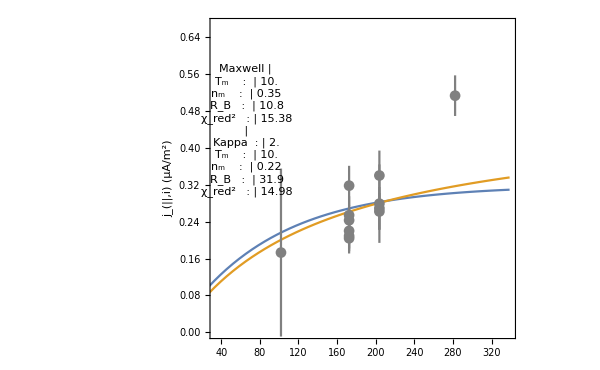
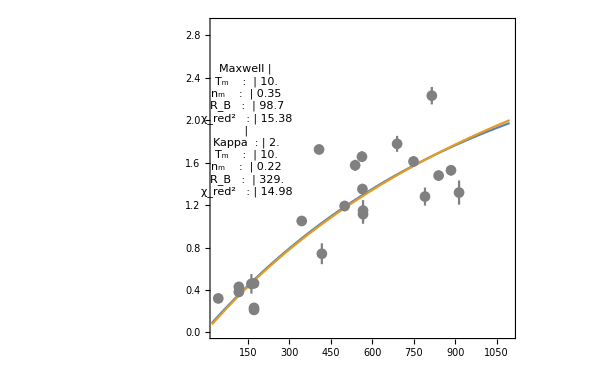
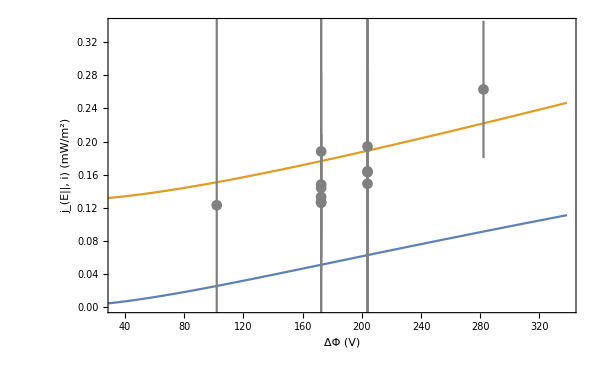
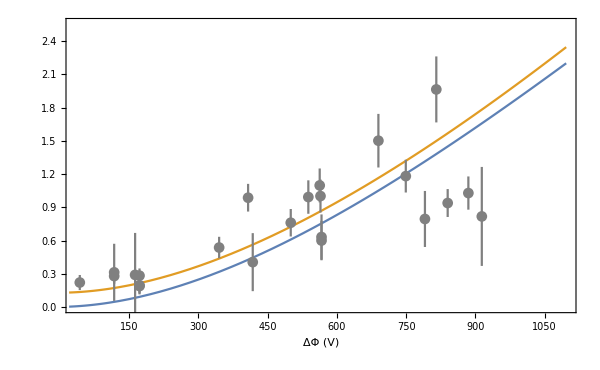
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
doubledPlot=Grid[{{doubledJVPlot1,Framed[doubledJVPlot2,FrameStyle->None,FrameMargins->{{-yTitlePad,0},{0,0}}]},{doubledJeVPlot1,Framed[doubledJeVPlot2,FrameStyle->None,FrameMargins->{{-yTitlePad,0},{0,0}}]}}]
```

```mathematica
If[makePlots==1,Print["Making plot in "<>dir<>" ..."];Print[doubledFilename<>" ..."];Export[dir<>doubledFilename,doubledPlot];Print["Done!"]]
```

Making plot in /SPENCEdata/Research/Satellites/FAST/kappa_dists/plots/20180322/ ...

Orb1612__twoIntervals__combJVJeVFit__inds_33-44.png ...

Done!

Let there be TWO densities

### Bounds

```mathematica
minFitT=10;
maxFitT=300;
minFitRB=2;
maxFitRB=100000;
minFitN=0.01;
maxFitN=10;
minFitKappa=1.501;
maxFitKappa=35;
```

```mathematica
kDoubledConstraints={minFitRB<kFitRB1<maxFitRB,minFitRB<kFitRB2<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN1<maxFitN,minFitN<kFitN2<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gDoubledConstraints={minFitRB<gFitRB1<maxFitRB,minFitRB<gFitRB2<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN1<maxFitN,minFitN<gFitN2<maxFitN};
```

### Initial guesses

```mathematica
kFitN1init=1;
kFitN2init=1;
kFitTinit=300;
kFitRBinit=10;
kFitKappainit=10;
kFitRB1init=10;
kFitRB2init=10;
```

```mathematica
gFitN1init=1;
gFitN2init=1;
gFitTinit=300;
gFitRBinit=10;
gFitRB1init=10;
gFitRB2init=10;
```

### Setup indices

```mathematica
indsSeg1=inds1;
```

```mathematica
indsSeg2=inds2;
```

```mathematica
(*indsSeg2=Range[162,198]; (*Alt*)*)
```

### Initialize plotData1, errorData1, plotDataWts1, etc.

Current data

```mathematica
{jDataSeg1,jDataSeg2}=(Partition[Riffle[pots[[#]],curs[[#]]],2])&/@{indsSeg1,indsSeg2};
```

```mathematica
{jErrDataSeg1,jErrDataSeg2}=(makeErrorData[pots[[#]],curs[[#]],curErrs[[#]]])&/@{indsSeg1,indsSeg2};
```

```mathematica
{jWtsSeg1,jWtsSeg2}=(1/(curErrs[[#]])^2)&/@{indsSeg1,indsSeg2};
```

Energy flux data

```mathematica
{jeDataSeg1,jeDataSeg2}=(Partition[Riffle[pots[[#]]+potTFactor,jes[[#]]],2])&/@{indsSeg1,indsSeg2};
```

```mathematica
{jeErrDataSeg1,jeErrDataSeg2}=(makeErrorData[pots[[#]]+potTFactor,jes[[#]],jeErrs[[#]]])&/@{indsSeg1,indsSeg2};
```

```mathematica
{jeWtsSeg1,jeWtsSeg2}=(1/(jeErrs[[#]])^2)&/@{indsSeg1,indsSeg2};
```

```mathematica
RBinit=kBestRB;Tminit=kBestT;nminit=kBestN;kappainit=kBestKappa;
```

```mathematica
combDatSeg1 = Join[jDataSeg1/.{x_,y_}->{1,x,y},jeDataSeg1/.{x_,y_}->{2,x,y}];
```

```mathematica
combDatSeg2 = Join[jDataSeg2/.{x_,y_}->{1,x,y},jeDataSeg2/.{x_,y_}->{2,x,y}];
```

```mathematica
combWtsSeg1=jWtsSeg1~Join~jeWtsSeg1;
```

```mathematica
combWtsSeg2=jWtsSeg2~Join~jeWtsSeg2;
```

```mathematica
doubledDat= Join[jDataSeg1/.{x_,y_}->{1,x,y},jeDataSeg1/.{x_,y_}->{2,x,y},jDataSeg2/.{x_,y_}->{3,x,y},jeDataSeg2/.{x_,y_}->{4,x,y}];
```

```mathematica
doubledWts=jWtsSeg1~Join~jeWtsSeg1~Join~jWtsSeg2~Join~jeWtsSeg2;
```

### Now the double-dens, double-RB model

```mathematica
kDoubledFitModel[set_,pot_,kFitRB1_,kFitRB2_,kFitT_,kFitN1_,kFitN2_,kFitKappa_]:=Which[set==1,Evaluate@JVKappa[pot,kFitRB1,kFitT,kFitN1,kFitKappa],set==2,Evaluate@JEVKappa[pot,kFitRB1,kFitT,kFitN1,kFitKappa],set==3,Evaluate@JVKappa[pot,kFitRB2,kFitT,kFitN2,kFitKappa],set==4,Evaluate@JEVKappa[pot,kFitRB2,kFitT,kFitN2,kFitKappa]]
```

```mathematica
gDoubledFitModel[set_,pot_,gFitRB1_,gFitRB2_,gFitT_,gFitN1_,gFitN2_]:=Which[set==1,Evaluate@JVMaxwellian[pot,gFitRB1,gFitT,gFitN1],set==2,Evaluate@JEVMaxwellian[pot,gFitRB1,gFitT,gFitN1],set==3,Evaluate@JVMaxwellian[pot,gFitRB2,gFitT,gFitN2],set==4,Evaluate@JEVMaxwellian[pot,gFitRB2,gFitT,gFitN2]]
```

```mathematica
kDoubledFit=NonlinearModelFit[doubledDat,{kDoubledFitModel[set,pot,kFitRB1,kFitRB2,kFitT,kFitN1,kFitN2,kFitKappa],kDoubledConstraints},{{kFitN1,kFitN1init},{kFitN2,kFitN2init},{kFitT,kFitTinit},{kFitRB1,kFitRB1init},{kFitRB2,kFitRB2init},{kFitKappa,kFitKappainit}},{set,pot},Weights->doubledWts]
```

FittedModel[Which[set==1,(0.0266987 «4» Gamma[1+«18»])/((1-1/(«18»)) «1» Gamma[-1/2+«18»]),«4»,«1»,(0.0000268059 «6» Gamma[1+34.9893])/((-2+34.9893) (-1+34.9893) Gamma[-1/2+34.9893])]]

```mathematica
gDoubledFit=NonlinearModelFit[doubledDat,{gDoubledFitModel[set,pot,gFitRB1,gFitRB2,gFitT,gFitN1,gFitN2],gDoubledConstraints},{{gFitN1,gFitN1init},{gFitN2,gFitN2init},{gFitT,gFitTinit},{gFitRB1,gFitRB1init},{gFitRB2,gFitRB2init}},{set,pot},Weights->doubledWts]
```

FittedModel[Which[set==1,«6»,0.0000268059 0.29195 67.5465 10.^(3/2) (2+pot/10.-ⅇ^(-pot/((-1+67.5465) «18»)) (2 (1-1/67.5465)+pot/10.))]]

```mathematica
kDOF=Length[doubledDat[[;;,1]]]-4;
```

```mathematica
gDOF=Length[doubledDat[[;;,1]]]-3;
```

```mathematica
{kDoubledN1,kDoubledN2,kDoubledT,kDoubledRB1,kDoubledRB2,kDoubledKappa,kDoubledChi2red}=Values@kDoubledFit["BestFitParameters"]~Join~{Total[(kDoubledFit["FitResiduals"])^2*doubledWts]/kDOF};
```

```mathematica
{gDoubledN1,gDoubledN2,gDoubledT,gDoubledRB1,gDoubledRB2,gDoubledChi2red}=Values@gDoubledFit["BestFitParameters"]~Join~{Total[(gDoubledFit["FitResiduals"])^2*doubledWts]/gDOF};
```

### Graphic options

```mathematica
doubledTitlePref="J-V, J_E-V Simult. Fit (`1`)";
```

```mathematica
(*getPadding[g_]:=Module[{im},im=Image[Show[g,LabelStyle->White,Background->White]];
BorderDimensions[im]]*)
```

```mathematica
imgSize=600;
```

```mathematica
{yTitlePad,xTitlePad,topTitlePad}={70,50,50};
{rPad,bPad,blankPad}={25,10,10};
```

```mathematica
TLPad={{yTitlePad,rPad},{bPad,topTitlePad}};
TRPad={{yTitlePad,rPad},{bPad,topTitlePad}};
BLPad={{yTitlePad,rPad},{xTitlePad,blankPad}};
BRPad={{yTitlePad,rPad},{xTitlePad,blankPad}};
```

```mathematica
imgPadding={{60,10},{50,50}};
```

### Now setup plots

```mathematica
(*Epilog->Inset[JVParTable,Scaled[{0.14,0.65}]]*)
```

```mathematica
(*JVPlotSeg1=Show[Plot[{JVMaxwellian[pot,gDoubledRB1,gDoubledT,gDoubledN],JVKappa[pot,kDoubledRB1,kDoubledT,kDoubledN,kDoubledKappa]},{pot,minPot,maxPot},PlotRange->{{minPot,maxPot},{minJ,maxJ}},PlotLegends->((Style[#,20])&/@{"Maxwellian",StringForm["κ = `1`",NumberForm[kDoubledKappa,{3,2}]]}),Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["J-V Fit (`1`)",combTitle],Bold,25]}},ImageSize->700,FrameStyle->Directive[Black,axesLabelSize]],ErrorListPlot[jErrDataSeg1,PlotStyle->Gray]]*)
```

```mathematica
doubledRepl={gRB1->gDoubledRB1,gRB2->gDoubledRB2,gTm->gDoubledT,gnm1->gDoubledN1,gnm2->gDoubledN2,gChi2->gDoubledChi2red,kRB1->kDoubledRB1,kRB2->kDoubledRB2,kTm->kDoubledT,knm1->kDoubledN1,knm2->kDoubledN2,kappa->kDoubledKappa,kChi2->kDoubledChi2red};
```

```mathematica
gDoubledVals1=(MapThread[NumberForm,{({gTm,gnm1}/.doubledRepl),{{3,0},{3,2}}}])~Join~{NumberForm[gRB1,3]/.doubledRepl}~Join~{NumberForm[gChi2,4]/.doubledRepl};
kDoubledVals1=(MapThread[NumberForm,{({kTm,knm1}/.doubledRepl),{{3,0},{3,2}}}])~Join~{NumberForm[kRB1,3]/.doubledRepl}~Join~{NumberForm[kChi2,4]/.doubledRepl};
```

```mathematica
gDoubledVals2=(MapThread[NumberForm,{({gTm,gnm2}/.doubledRepl),{{3,0},{3,2}}}])~Join~{NumberForm[gRB2,3]/.doubledRepl}~Join~{NumberForm[gChi2,4]/.doubledRepl};
kDoubledVals2=(MapThread[NumberForm,{({kTm,knm2}/.doubledRepl),{{3,0},{3,2}}}])~Join~{NumberForm[kRB2,3]/.doubledRepl}~Join~{NumberForm[kChi2,4]/.doubledRepl};
```

#### Parameter tables

```mathematica
doubledParTable1=Text[Grid[Transpose[{{Style["Maxwell",Bold,(ColorData[97,"ColorList"])[[1]]]}~Join~parNames~Join~{"",Style["Kappa  :",Bold,(ColorData[97,"ColorList"])[[2]]]}~Join~parNames,{""}~Join~gDoubledVals1~Join~{"",(ToString@StringForm["`1`",NumberForm[kDoubledKappa,3]])}~Join~kDoubledVals1}],Alignment->".",Spacings->{0,pTableVSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
doubledParTable2=Text[Grid[Transpose[{{Style["Maxwell",Bold,(ColorData[97,"ColorList"])[[1]]]}~Join~parNames~Join~{"",Style["Kappa  :",Bold,(ColorData[97,"ColorList"])[[2]]]}~Join~parNames,{""}~Join~gDoubledVals2~Join~{"",(ToString@StringForm["`1`",NumberForm[kDoubledKappa,3]])}~Join~kDoubledVals2}],Alignment->".",Spacings->{0,pTableVSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
doubledTitle1=StringJoin@Riffle[time[[indsSeg1[[{1,-1}]]]],"–"];
```

```mathematica
doubledTitle2=StringJoin@Riffle[time[[indsSeg2[[{1,-1}]]]],"–"];
```

#### Plots (to be shown momentarily)

```mathematica
doubledFitJVPlot1=Plot[Evaluate@(({JVMaxwellian[pot,gRB1,gTm,gnm1],JVKappa[pot,kRB1,kTm,knm1,kappa]})/.doubledRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJ,maxJ}},Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",None},{None,Style[StringForm[doubledTitlePref,doubledTitle1],Bold,titleSize]}},ImageSize->imgSize,ImagePadding->TLPad,FrameStyle->Directive[Black,axesLabelSize],FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},Epilog->Inset[doubledParTable1,Scaled[pTableScaledLoc]]];
```

```mathematica
doubledFitJeVPlot1=Plot[Evaluate@(({JEVMaxwellian[pot,gRB1,gTm,gnm1],JEVKappa[pot,kRB1,kTm,knm1,kappa]})/.doubledRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJe,maxJe}},Frame->True,FrameLabel->{{"j_(E||, i) (mW/m^2)",""},{"ΔΦ (V)",""}},FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->imgSize,ImagePadding->BLPad,FrameStyle->Directive[Black,axesLabelSize]];
```

```mathematica
(*Was going to be the version without the legend that works with getPadding function; for some reason the Show function in getPadding hates legends … *)
(*doubledFitJVPlot2NOLEG=Plot[Evaluate@(({JVMaxwellian[pot,gRB2,gTm,gnm],JVKappa[pot,kRB2,kTm,knm,kappa]})/.doubledRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJ,maxJ}},Frame->True,FrameLabel->{{"",""},{"",Style[StringForm[doubledTitlePref,doubledTitle2],Bold,titleSize]}},ImageSize->imgSize,FrameStyle->Directive[Black,axesLabelSize],FrameTicksStyle->{{Directive[FontOpacity->0,FontSize->0],Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},Epilog->Inset[doubledParTable2,Scaled[pTableScaledLoc]]];*)
```

```mathematica
doubledFitJVPlot2=Plot[Evaluate@(({JVMaxwellian[pot,gRB2,gTm,gnm2],JVKappa[pot,kRB2,kTm,knm2,kappa]})/.doubledRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJ,maxJ}},Frame->True,FrameLabel->{{None,None},{None,Style[StringForm[doubledTitlePref,doubledTitle2],Bold,titleSize]}},ImageSize->imgSize,ImagePadding->TRPad,FrameStyle->Directive[Black,axesLabelSize],FrameTicksStyle->{{Directive[FontOpacity->0,FontSize->0],Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},Epilog->Inset[doubledParTable2,Scaled[pTableScaledLoc]]];
```

```mathematica
(*PlotLegends->Map[(Style[#,axesLabelSize])&,{"Maxwellian",StringForm["κ = `1`",NumberForm[(kappa/.doubledRepl),{3,3}]]}],*)
```

```mathematica
doubledFitJeVPlot2=Plot[Evaluate@(({JEVMaxwellian[pot,gRB2,gTm,gnm2],JEVKappa[pot,kRB2,kTm,knm2,kappa]})/.doubledRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJe,maxJe}},Frame->True,FrameLabel->{{None,None},{"ΔΦ (V)",None}},ImageSize->imgSize,ImagePadding->BRPad,FrameStyle->Directive[Black,axesLabelSize],FrameTicksStyle->{{Directive[FontOpacity->0,FontSize->0],Automatic},{Automatic,Automatic}}];
```

```mathematica
(*{p1h,p1v}=getPadding[doubledFitJVPlot1];
{p2h,p2v}=getPadding[doubledFitJVPlot2];*)
```

```mathematica
(*verticalPadding=Max/@Transpose[{p1v,p2v}];*)
```

```mathematica
(*doubledJVPlot1=Show[{doubledFitJVPlot1,ErrorListPlot[jErrDataSeg1,PlotStyle->Gray]},ImagePadding-> {p1h,verticalPadding}];*)
```

```mathematica
(*doubledJVPlot2=Show[{doubledFitJVPlot2,ErrorListPlot[jErrDataSeg2,PlotStyle->Gray]},ImagePadding->{p2h,verticalPadding}];*)
```

```mathematica
doubledJVPlot1=Show[doubledFitJVPlot1,ErrorListPlot[jErrDataSeg1,PlotStyle->Gray]];
```

```mathematica
doubledJeVPlot1=Show[doubledFitJeVPlot1,ErrorListPlot[jeErrDataSeg1,PlotStyle->Gray]];
```

```mathematica
doubledJVPlot2=Show[doubledFitJVPlot2,ErrorListPlot[jErrDataSeg2,PlotStyle->Gray]];
```

```mathematica
doubledJeVPlot2=Show[doubledFitJeVPlot2,ErrorListPlot[jeErrDataSeg2,PlotStyle->Gray]];
```

### Now show plots

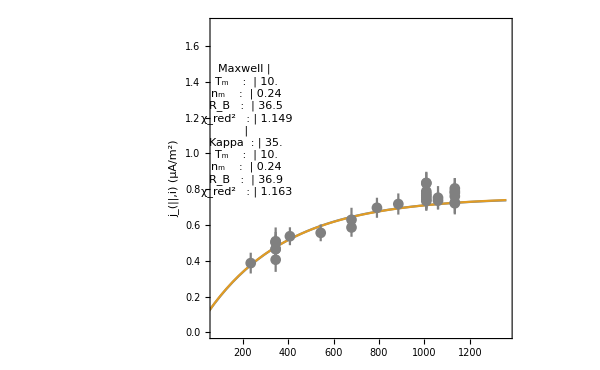
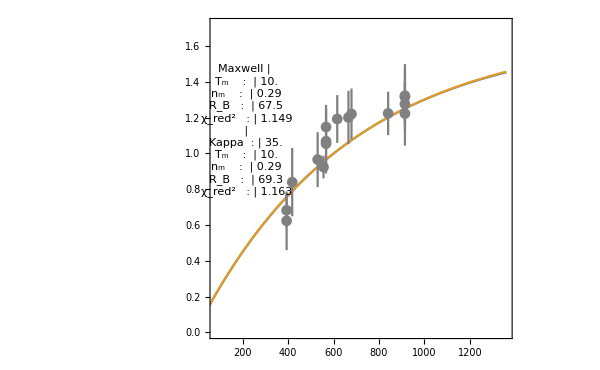
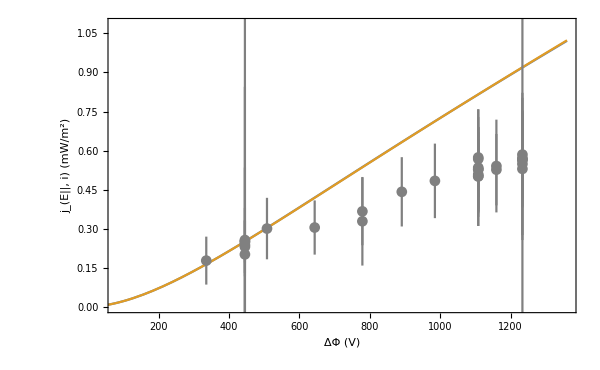
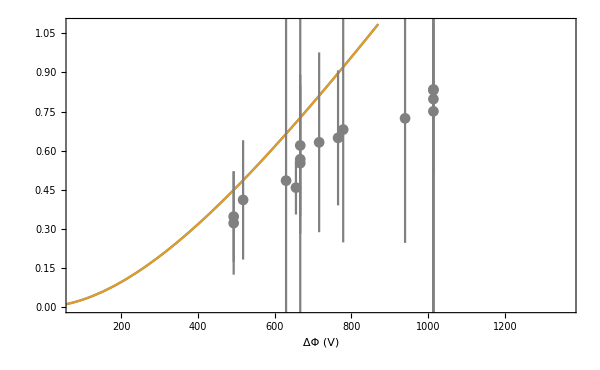
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
doubledPlot=Grid[{{doubledJVPlot1,Framed[doubledJVPlot2,FrameStyle->None,FrameMargins->{{-yTitlePad,0},{0,0}}]},{doubledJeVPlot1,Framed[doubledJeVPlot2,FrameStyle->None,FrameMargins->{{-yTitlePad,0},{0,0}}]}}]
```

```mathematica
If[makePlots==1,Print["Making plot in "<>dir<>" ..."];Print[doubledFilename<>" ..."];Export[dir<>doubledFilename,doubledPlot];Print["Done!"]]
```

Making plot in /SPENCEdata/Research/Satellites/FAST/kappa_dists/plots/20180321/ ...

Orb1612__twoIntervals__combJVJeVFit__inds_232-241.png ...

Done!

Let there be TWO densities, TWO temperatures

### Bounds

```mathematica
minFitT=30;
maxFitT=300;
minFitRB=2;
maxFitRB=100000;
minFitN=0.01;
maxFitN=10;
minFitKappa=1.501;
maxFitKappa=35;
```

```mathematica
kDoubledConstraints={minFitRB<kFitRB1<maxFitRB,minFitRB<kFitRB2<maxFitRB,minFitT<kFitT1<maxFitT,minFitT<kFitT2<maxFitT,minFitN<kFitN1<maxFitN,minFitN<kFitN2<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gDoubledConstraints={minFitRB<gFitRB1<maxFitRB,minFitRB<gFitRB2<maxFitRB,minFitT<gFitT1<maxFitT,minFitT<gFitT2<maxFitT,minFitN<gFitN1<maxFitN,minFitN<gFitN2<maxFitN};
```

### Initial guesses

```mathematica
kFitN1init=1;
kFitN2init=1;
kFitT1init=300;
kFitT2init=300;
kFitRBinit=10;
kFitKappainit=10;
kFitRB1init=10;
kFitRB2init=10;
```

```mathematica
gFitN1init=1;
gFitN2init=1;
gFitT1init=300;
gFitT2init=300;
gFitRBinit=10;
gFitRB1init=10;
gFitRB2init=10;
```

### Setup indices

```mathematica
indsSeg1=inds1;
```

```mathematica
indsSeg2=inds2;
```

```mathematica
(*indsSeg2=Range[162,198]; (*Alt*)*)
```

### Initialize plotData1, errorData1, plotDataWts1, etc.

Current data

```mathematica
{jDataSeg1,jDataSeg2}=(Partition[Riffle[pots[[#]],curs[[#]]],2])&/@{indsSeg1,indsSeg2};
```

```mathematica
{jErrDataSeg1,jErrDataSeg2}=(makeErrorData[pots[[#]],curs[[#]],curErrs[[#]]])&/@{indsSeg1,indsSeg2};
```

```mathematica
{jWtsSeg1,jWtsSeg2}=(1/(curErrs[[#]])^2)&/@{indsSeg1,indsSeg2};
```

Energy flux data

```mathematica
{jeDataSeg1,jeDataSeg2}=(Partition[Riffle[pots[[#]]+potTFactor,jes[[#]]],2])&/@{indsSeg1,indsSeg2};
```

```mathematica
{jeErrDataSeg1,jeErrDataSeg2}=(makeErrorData[pots[[#]]+potTFactor,jes[[#]],jeErrs[[#]]])&/@{indsSeg1,indsSeg2};
```

```mathematica
{jeWtsSeg1,jeWtsSeg2}=(1/(jeErrs[[#]])^2)&/@{indsSeg1,indsSeg2};
```

```mathematica
RBinit=kBestRB;Tminit=kBestT;nminit=kBestN;kappainit=kBestKappa;
```

```mathematica
combDatSeg1 = Join[jDataSeg1/.{x_,y_}->{1,x,y},jeDataSeg1/.{x_,y_}->{2,x,y}];
```

```mathematica
combDatSeg2 = Join[jDataSeg2/.{x_,y_}->{1,x,y},jeDataSeg2/.{x_,y_}->{2,x,y}];
```

```mathematica
combWtsSeg1=jWtsSeg1~Join~jeWtsSeg1;
```

```mathematica
combWtsSeg2=jWtsSeg2~Join~jeWtsSeg2;
```

```mathematica
doubledDat= Join[jDataSeg1/.{x_,y_}->{1,x,y},jeDataSeg1/.{x_,y_}->{2,x,y},jDataSeg2/.{x_,y_}->{3,x,y},jeDataSeg2/.{x_,y_}->{4,x,y}];
```

```mathematica
doubledWts=jWtsSeg1~Join~jeWtsSeg1~Join~jWtsSeg2~Join~jeWtsSeg2;
```

### Now the double-dens, double-RB model

```mathematica
kDoubledFitModel[set_,pot_,kFitRB1_,kFitRB2_,kFitT1_,kFitT2_,kFitN1_,kFitN2_,kFitKappa_]:=Which[set==1,Evaluate@JVKappa[pot,kFitRB1,kFitT1,kFitN1,kFitKappa],set==2,Evaluate@JEVKappa[pot,kFitRB1,kFitT1,kFitN1,kFitKappa],set==3,Evaluate@JVKappa[pot,kFitRB2,kFitT2,kFitN2,kFitKappa],set==4,Evaluate@JEVKappa[pot,kFitRB2,kFitT2,kFitN2,kFitKappa]]
```

```mathematica
gDoubledFitModel[set_,pot_,gFitRB1_,gFitRB2_,gFitT1_,gFitT2_,gFitN1_,gFitN2_]:=Which[set==1,Evaluate@JVMaxwellian[pot,gFitRB1,gFitT1,gFitN1],set==2,Evaluate@JEVMaxwellian[pot,gFitRB1,gFitT1,gFitN1],set==3,Evaluate@JVMaxwellian[pot,gFitRB2,gFitT2,gFitN2],set==4,Evaluate@JEVMaxwellian[pot,gFitRB2,gFitT2,gFitN2]]
```

```mathematica
kDoubledFit=NonlinearModelFit[doubledDat,{kDoubledFitModel[set,pot,kFitRB1,kFitRB2,kFitT1,kFitT2,kFitN1,kFitN2,kFitKappa],kDoubledConstraints},{{kFitN1,kFitN1init},{kFitN2,kFitN2init},{kFitT1,kFitT1init},{kFitT2,kFitT2init},{kFitRB1,kFitRB1init},{kFitRB2,kFitRB2init},{kFitKappa,kFitKappainit}},{set,pot},Weights->doubledWts]
```

FittedModel[Which[set==1,(«1»)/((1-1/(«19»)) «1» Gamma[«1»]),set==2,(«1»)/(«1»),«1»,(«1»)/(«1»),set==4,(0.0000268059 «6» Gamma[1+2.1288])/((-2+2.1288) (-1+2.1288) Gamma[-1/2+2.1288])]]

```mathematica
gDoubledFit=NonlinearModelFit[doubledDat,{gDoubledFitModel[set,pot,gFitRB1,gFitRB2,gFitT1,gFitT2,gFitN1,gFitN2],gDoubledConstraints},{{gFitN1,gFitN1init},{gFitN2,gFitN2init},{gFitT1,gFitT1init},{gFitT2,gFitT2init},{gFitRB1,gFitRB1init},{gFitRB2,gFitRB2init}},{set,pot},Weights->doubledWts]
```

FittedModel[Which[set==1,«10» «4»,«5»,0.0000268059 0.569796 19.8204 («18»)^(3/2) (2+pot/30.-ⅇ^(-pot/((-1+19.8204) «18»)) (2 (1-1/19.8204)+pot/30.))]]

```mathematica
kDOF=Length[doubledDat[[;;,1]]]-4;
```

```mathematica
gDOF=Length[doubledDat[[;;,1]]]-3;
```

```mathematica
{kDoubledN1,kDoubledN2,kDoubledT1,kDoubledT2,kDoubledRB1,kDoubledRB2,kDoubledKappa,kDoubledChi2red}=Values@kDoubledFit["BestFitParameters"]~Join~{Total[(kDoubledFit["FitResiduals"])^2*doubledWts]/kDOF};
```

```mathematica
{gDoubledN1,gDoubledN2,gDoubledT1,gDoubledT2,gDoubledRB1,gDoubledRB2,gDoubledChi2red}=Values@gDoubledFit["BestFitParameters"]~Join~{Total[(gDoubledFit["FitResiduals"])^2*doubledWts]/gDOF};
```

### Graphic options

```mathematica
doubledTitlePref="J-V, J_E-V Simult. Fit (`1`)";
```

```mathematica
(*getPadding[g_]:=Module[{im},im=Image[Show[g,LabelStyle->White,Background->White]];
BorderDimensions[im]]*)
```

```mathematica
imgSize=600;
```

```mathematica
{yTitlePad,xTitlePad,topTitlePad}={70,50,50};
{rPad,bPad,blankPad}={25,10,10};
```

```mathematica
TLPad={{yTitlePad,rPad},{bPad,topTitlePad}};
TRPad={{yTitlePad,rPad},{bPad,topTitlePad}};
BLPad={{yTitlePad,rPad},{xTitlePad,blankPad}};
BRPad={{yTitlePad,rPad},{xTitlePad,blankPad}};
```

```mathematica
imgPadding={{60,10},{50,50}};
```

### Now setup plots

```mathematica
(*Epilog->Inset[JVParTable,Scaled[{0.14,0.65}]]*)
```

```mathematica
(*JVPlotSeg1=Show[Plot[{JVMaxwellian[pot,gDoubledRB1,gDoubledT,gDoubledN],JVKappa[pot,kDoubledRB1,kDoubledT,kDoubledN,kDoubledKappa]},{pot,minPot,maxPot},PlotRange->{{minPot,maxPot},{minJ,maxJ}},PlotLegends->((Style[#,20])&/@{"Maxwellian",StringForm["κ = `1`",NumberForm[kDoubledKappa,{3,2}]]}),Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["J-V Fit (`1`)",combTitle],Bold,25]}},ImageSize->700,FrameStyle->Directive[Black,axesLabelSize]],ErrorListPlot[jErrDataSeg1,PlotStyle->Gray]]*)
```

```mathematica
doubledRepl={gRB1->gDoubledRB1,gRB2->gDoubledRB2,gTm1->gDoubledT1,gTm2->gDoubledT2,gnm1->gDoubledN1,gnm2->gDoubledN2,gChi2->gDoubledChi2red,kRB1->kDoubledRB1,kRB2->kDoubledRB2,kTm1->kDoubledT1,kTm2->kDoubledT2,knm1->kDoubledN1,knm2->kDoubledN2,kappa->kDoubledKappa,kChi2->kDoubledChi2red};
```

```mathematica
gDoubledVals1=(MapThread[NumberForm,{({gTm1,gnm1}/.doubledRepl),{{3,0},{3,2}}}])~Join~{NumberForm[gRB1,3]/.doubledRepl}~Join~{NumberForm[gChi2,4]/.doubledRepl};
kDoubledVals1=(MapThread[NumberForm,{({kTm1,knm1}/.doubledRepl),{{3,0},{3,2}}}])~Join~{NumberForm[kRB1,3]/.doubledRepl}~Join~{NumberForm[kChi2,4]/.doubledRepl};
```

```mathematica
gDoubledVals2=(MapThread[NumberForm,{({gTm2,gnm2}/.doubledRepl),{{3,0},{3,2}}}])~Join~{NumberForm[gRB2,3]/.doubledRepl}~Join~{NumberForm[gChi2,4]/.doubledRepl};
kDoubledVals2=(MapThread[NumberForm,{({kTm2,knm2}/.doubledRepl),{{3,0},{3,2}}}])~Join~{NumberForm[kRB2,3]/.doubledRepl}~Join~{NumberForm[kChi2,4]/.doubledRepl};
```

#### Parameter tables

```mathematica
doubledParTable1=Text[Grid[Transpose[{{Style["Maxwell",Bold,(ColorData[97,"ColorList"])[[1]]]}~Join~parNames~Join~{"",Style["Kappa  :",Bold,(ColorData[97,"ColorList"])[[2]]]}~Join~parNames,{""}~Join~gDoubledVals1~Join~{"",(ToString@StringForm["`1`",NumberForm[kDoubledKappa,3]])}~Join~kDoubledVals1}],Alignment->".",Spacings->{0,pTableVSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
doubledParTable2=Text[Grid[Transpose[{{Style["Maxwell",Bold,(ColorData[97,"ColorList"])[[1]]]}~Join~parNames~Join~{"",Style["Kappa  :",Bold,(ColorData[97,"ColorList"])[[2]]]}~Join~parNames,{""}~Join~gDoubledVals2~Join~{"",(ToString@StringForm["`1`",NumberForm[kDoubledKappa,3]])}~Join~kDoubledVals2}],Alignment->".",Spacings->{0,pTableVSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
doubledTitle1=StringJoin@Riffle[time[[indsSeg1[[{1,-1}]]]],"–"];
```

```mathematica
doubledTitle2=StringJoin@Riffle[time[[indsSeg2[[{1,-1}]]]],"–"];
```

#### Plots (to be shown momentarily)

```mathematica
doubledFitJVPlot1=Plot[Evaluate@(({JVMaxwellian[pot,gRB1,gTm1,gnm1],JVKappa[pot,kRB1,kTm1,knm1,kappa]})/.doubledRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJ,maxJ}},Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",None},{None,Style[StringForm[doubledTitlePref,doubledTitle1],Bold,titleSize]}},ImageSize->imgSize,ImagePadding->TLPad,FrameStyle->Directive[Black,axesLabelSize],FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},Epilog->Inset[doubledParTable1,Scaled[pTableScaledLoc]]];
```

```mathematica
doubledFitJeVPlot1=Plot[Evaluate@(({JEVMaxwellian[pot,gRB1,gTm1,gnm1],JEVKappa[pot,kRB1,kTm1,knm1,kappa]})/.doubledRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJe,maxJe}},Frame->True,FrameLabel->{{"j_(E||, i) (mW/m^2)",""},{"ΔΦ (V)",""}},FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->imgSize,ImagePadding->BLPad,FrameStyle->Directive[Black,axesLabelSize]];
```

```mathematica
(*Was going to be the version without the legend that works with getPadding function; for some reason the Show function in getPadding hates legends … *)
(*doubledFitJVPlot2NOLEG=Plot[Evaluate@(({JVMaxwellian[pot,gRB2,gTm,gnm],JVKappa[pot,kRB2,kTm,knm,kappa]})/.doubledRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJ,maxJ}},Frame->True,FrameLabel->{{"",""},{"",Style[StringForm[doubledTitlePref,doubledTitle2],Bold,titleSize]}},ImageSize->imgSize,FrameStyle->Directive[Black,axesLabelSize],FrameTicksStyle->{{Directive[FontOpacity->0,FontSize->0],Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},Epilog->Inset[doubledParTable2,Scaled[pTableScaledLoc]]];*)
```

```mathematica
doubledFitJVPlot2=Plot[Evaluate@(({JVMaxwellian[pot,gRB2,gTm2,gnm2],JVKappa[pot,kRB2,kTm2,knm2,kappa]})/.doubledRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJ,maxJ}},Frame->True,FrameLabel->{{None,None},{None,Style[StringForm[doubledTitlePref,doubledTitle2],Bold,titleSize]}},ImageSize->imgSize,ImagePadding->TRPad,FrameStyle->Directive[Black,axesLabelSize],FrameTicksStyle->{{Directive[FontOpacity->0,FontSize->0],Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},Epilog->Inset[doubledParTable2,Scaled[pTableScaledLoc]]];
```

```mathematica
(*PlotLegends->Map[(Style[#,axesLabelSize])&,{"Maxwellian",StringForm["κ = `1`",NumberForm[(kappa/.doubledRepl),{3,3}]]}],*)
```

```mathematica
doubledFitJeVPlot2=Plot[Evaluate@(({JEVMaxwellian[pot,gRB2,gTm2,gnm2],JEVKappa[pot,kRB2,kTm2,knm2,kappa]})/.doubledRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJe,maxJe}},Frame->True,FrameLabel->{{None,None},{"ΔΦ (V)",None}},ImageSize->imgSize,ImagePadding->BRPad,FrameStyle->Directive[Black,axesLabelSize],FrameTicksStyle->{{Directive[FontOpacity->0,FontSize->0],Automatic},{Automatic,Automatic}}];
```

```mathematica
(*{p1h,p1v}=getPadding[doubledFitJVPlot1];
{p2h,p2v}=getPadding[doubledFitJVPlot2];*)
```

```mathematica
(*verticalPadding=Max/@Transpose[{p1v,p2v}];*)
```

```mathematica
(*doubledJVPlot1=Show[{doubledFitJVPlot1,ErrorListPlot[jErrDataSeg1,PlotStyle->Gray]},ImagePadding-> {p1h,verticalPadding}];*)
```

```mathematica
(*doubledJVPlot2=Show[{doubledFitJVPlot2,ErrorListPlot[jErrDataSeg2,PlotStyle->Gray]},ImagePadding->{p2h,verticalPadding}];*)
```

```mathematica
doubledJVPlot1=Show[doubledFitJVPlot1,ErrorListPlot[jErrDataSeg1,PlotStyle->Gray]];
```

```mathematica
doubledJeVPlot1=Show[doubledFitJeVPlot1,ErrorListPlot[jeErrDataSeg1,PlotStyle->Gray]];
```

```mathematica
doubledJVPlot2=Show[doubledFitJVPlot2,ErrorListPlot[jErrDataSeg2,PlotStyle->Gray]];
```

```mathematica
doubledJeVPlot2=Show[doubledFitJeVPlot2,ErrorListPlot[jeErrDataSeg2,PlotStyle->Gray]];
```

### Now show plots

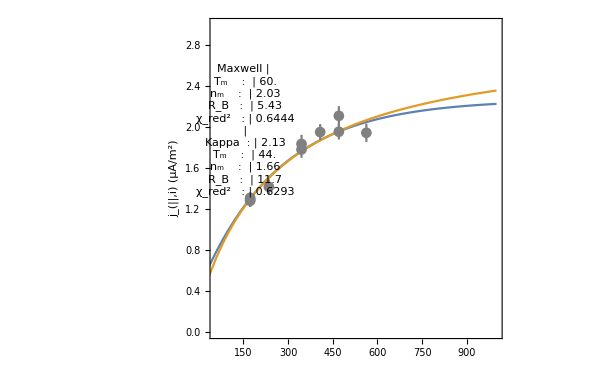
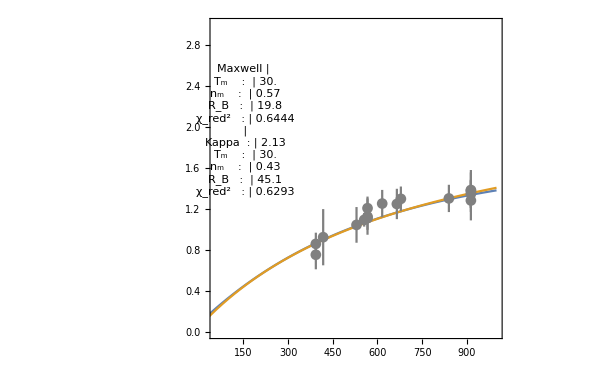
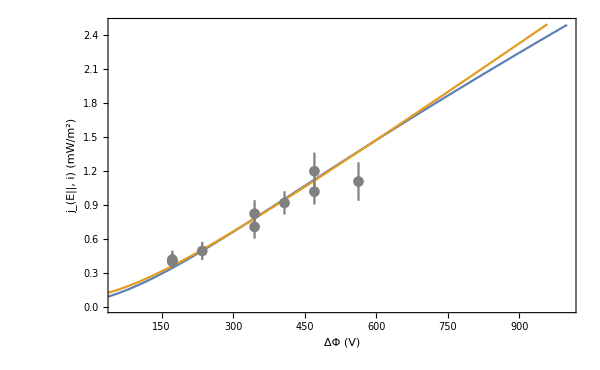
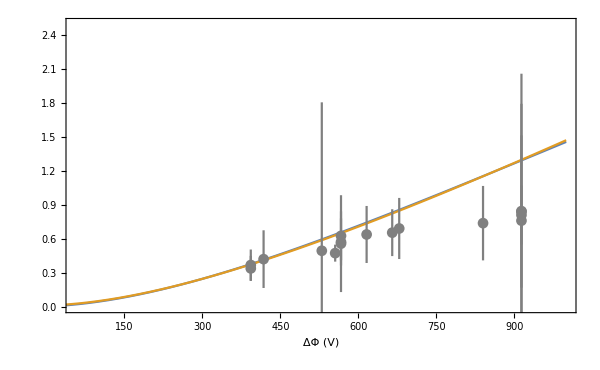
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
doubledPlot=Grid[{{doubledJVPlot1,Framed[doubledJVPlot2,FrameStyle->None,FrameMargins->{{-yTitlePad,0},{0,0}}]},{doubledJeVPlot1,Framed[doubledJeVPlot2,FrameStyle->None,FrameMargins->{{-yTitlePad,0},{0,0}}]}}]
```

```mathematica
If[makePlots==1,Print["Making plot in "<>dir<>" ..."];Print[doubledFilename<>" ..."];Export[dir<>doubledFilename,doubledPlot];Print["Done!"]]
```

Making plot in /SPENCEdata/Research/Satellites/FAST/kappa_dists/plots/20180321/ ...

Orb1612__twoIntervals__combJVJeVFit__inds_232-241.png ...

Done!

Param tables

### J-V params

```mathematica
kFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
kFitN | 0.772578 | 6.02481 | 0.128233 | 0.918808
kFitT | 31.0539 | 763.246 | 0.0406866 | 0.974112
kFitRB | 68.1331 | 3103.42 | 0.0219542 | 0.986026
kFitKappa | 34.968 | 64235.1 | 0.000544376 | 0.999653

```mathematica
gFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
gFitN | 0.775688 | 0.195529 | 3.96713 | 0.0580614
gFitT | 30.6458 | 24.6243 | 1.24454 | 0.339364
gFitRB | 66.4896 | 23.9099 | 2.78084 | 0.108644

### J_E-V params

```mathematica
kFitJeV["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
kFitN | 0.598261 | 6.58641 | 0.0908326 | 0.942332
kFitT | 30.2064 | 848.659 | 0.0355931 | 0.97735
kFitRB | 66.8915 | 1627.47 | 0.0411016 | 0.973849
kFitKappa | 2.00998 | 0.550172 | 3.65336 | 0.17009

```mathematica
gFitJeV["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
gFitN | 1.11344 | 0.132185 | 8.42334 | 0.0138028
gFitT | 193.24 | 38.0501 | 5.07857 | 0.0366535
gFitRB | 12.8063 | 12.4226 | 1.03089 | 0.410943

### Params from combined fit

```mathematica
kCombFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
kFitRB | 196.269 | 355.376 | 0.552288 | 0.600703
kFitT | 18.7191 | 41.9346 | 0.446389 | 0.670975
kFitN | 0.452254 | 0.436179 | 1.03685 | 0.339773
kFitKappa | 2.00561 | 0.0257765 | 77.8079 | 3.03411×10^-10

```mathematica
gCombFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
gFitRB | 55.822 | 22.2385 | 2.51015 | 0.0403881
gFitT | 31.9975 | 24.8822 | 1.28596 | 0.239358
gFitN | 0.801642 | 0.192171 | 4.1715 | 0.00418131